```mathematica
NoKernels=21;
```

## Setup

This function takes a value of lambda and returns the 100 eigenvalues of the hamiltonian which have the lowest absolute value. nn is the matrix size, dρ is the step size, and ρinf is numerical infinity for the problem.

Because the results of the calculation are highly sensitive to changes in ρinf, I pinned ρinf to λ.

```mathematica
RoughCritical[λ_]:=Module[{H,res,dρ,ρinf,nn},
dρ=0.1;
ρinf=Round[20*λ];
nn=Round[ρinf/dρ];
(*Print["dρ = "<>ToString[dρ]<>", ρinf = "<>ToString[ρinf]<>", and nn = "<>ToString[nn]<>"."];*)
H=SparseArray[{{n_,n_}->2./dρ^2-2./(n*dρ)ⅇ^(-n*dρ/λ)+(l*(l+1))/(n*dρ)^2,{n_, m_}/; Abs[n-m] == 1 -> -1./dρ^2},{nn,nn}, 0.];
res=Sort[Eigenvalues[H,-100]];(*Went from 100 down to 25 eigenvalues, which sped this calculation up immensely with no apparent loss of information*)
Return[res]
]
```

```mathematica
CountNegs[list_]:=Module[{neg,i},
neg=0;
For[i=1,list[[i]]<0,i++,
neg++;
];
Return[neg]
]
```

```mathematica
FindLs[l0_,lf_,val_,vaf_,range_]:=Module[{mid,vam,lnegs,mnegs,hnegs,res},
res={};
mid=l0+(lf-l0)/2;
lnegs=CountNegs[val];
vam=RoughCritical[mid];
mnegs=CountNegs[vam];
hnegs=CountNegs[vaf];
If[lf-l0>range,
If[lnegs<mnegs ||(lnegs==mnegs && val[[1]] < vam[[1]]&& mnegs>0),
res=Join[res,FindLs[l0,mid,val,vam,range]];
Return[res]
];
If[mnegs<hnegs || (hnegs==mnegs && vam[[1]] < vaf[[1]]&&hnegs>0),
res=Join[res,FindLs[mid,lf,vam,vaf,range]];
Return[res]
];
,
Print["Found one!"];
Return[{{l0,lf}}];
]
]
```

## Finding candidate ranges

```mathematica
RangeChunk[low_,high_]:=Module[{res,val,vaf,lnegs,hnegs},
res={};
val=RoughCritical[low];
lnegs=CountNegs[val];
vaf=RoughCritical[high];
hnegs=CountNegs[vaf];
If[lnegs<hnegs || (lnegs==hnegs && val[[1]] < vaf[[1]]&& hnegs>0),
res=FindLs[low,high,val,vaf,1];
];
Return[res]
]
```

### Setup

```mathematica
Critical[λ_,consts_]:=Module[{H,res,dρ,ρinf,nn},
dρ=consts[[1]];
ρinf=Round[consts[[2]]];
nn=Round[ρinf/dρ];
(*Print["dρ = "<>ToString[dρ]<>", ρinf = "<>ToString[ρinf]<>", and nn = "<>ToString[nn]<>"."];*)
H=SparseArray[{{n_,n_}->2./dρ^2-2./(n*dρ)ⅇ^(-n*dρ/λ)+(l(l+1))/(n*dρ)^2,{n_, m_}/; Abs[n-m] == 1 -> -1./dρ^2},{nn,nn}, 0.];
res=Sort[Eigenvalues[H,-25]];(*Went from 100 down to 25 eigenvalues, which sped this calculation up immensely with no apparent loss of information*)
Return[res]
]
```

```mathematica
Bisect[F_,consts_,x0_,xf_,ϵ_]:=Module[{mid,val,lnegs,vam,mnegs,vah},
mid=x0+Abs[x0-xf]/2;
Print["Bisecting. Midpoint is "<>ToString[mid]];
val=F[x0,consts];
lnegs=CountNegs[val];
vam=F[mid,consts];
mnegs=CountNegs[vam];
If[xf-x0>ϵ,
(*Print[{lnegs,mnegs},{val[[1]],vam[[1]]}];*)
If[lnegs<mnegs || (lnegs==mnegs && val[[1]] < vam[[1]]), (*if there is a zero on the lower half*)
Return[Bisect[F,consts,x0,mid,ϵ]];, (*bisect it*)
Return[Bisect[F,consts,mid,xf,ϵ]]; (*otherwise try the upper half*)
];,
vah = F[xf,consts];
Return[{mid,lnegs,CountNegs[vah]}];
]
]
```

```mathematica
Findlc[input_,i_,eps_]:=Module[{val,vah,lnegs,hnegs,res},
Print["***Beginning to calculate the "<>ToString[i]<>"th lambda, part "<>ToString[input[[1]]]];
val=Critical[input[[3]],{0.1,input[[2]],input[[2]]/0.1}];
vah=Critical[input[[4]],{0.1,input[[2]],input[[2]]/0.1}];
lnegs=CountNegs[val];
hnegs=CountNegs[vah];
If[lnegs<hnegs || (lnegs==hnegs && val[[1]]<vah[[1]]),(*doublechecks for zero*)
Print["Pass!"];
res={input[[1]],Bisect[Critical,{0.1,input[[2]],input[[2]]/0.1},input[[3]],input[[4]],eps]};
,(*else*)
Print["Fail!"];
res={input[[1]],Null};
];
Return[res]
]
```

```mathematica
ListRandomize[list_]:=Module[{order,res},
order=Table[{RandomReal[],i},{i,1,Length[list]}];
order = Sort[order];
res=Table[list[[order[[i,2]]]],{i,1,Length[list]}];
Return[res]
]
```

```mathematica
rhoinfs={40,80};
```

### Stuffitty stuff stuff

```mathematica
int=(5.*10^5-0.25/2)/NoKernels
```

23809.5

```mathematica
chunks={{0.5,Sqrt[2*int+0.25]}}
For[i=1,i<NoKernels,i++,
chunks=Append[chunks,{chunks[[i,2]],Sqrt[chunks[[i,2]]^2+2*int]}]
]
```

{{0.5,218.218}}

```mathematica
chunks
```

{{0.5,218.218},{218.218,308.607},{308.607,377.965},{377.965,436.436},{436.436,487.95},{487.95,534.523},{534.523,577.35},{577.35,617.214},{617.214,654.654},{654.654,690.066},{690.066,723.747},{723.747,755.929},{755.929,786.796},{786.796,816.497},{816.497,845.154},{845.154,872.872},{872.872,899.735},{899.735,925.82},{925.82,951.19},{951.19,975.9},{975.9,1000.}}

```mathematica
DistributeDefinitions[RangeChunk,CountNegs,chunks,FindLs,RoughCritical,Critical,Bisect,Findlc]
```

```mathematica
F[x_]:=a x^2+b x+c
```

```mathematica
SetDirectory["~/Desktop/Ellen/Thesis/Calculations/Angular Momentum/"]
```

/Network/Servers/Knowlton.local/Users/zphantom/Desktop/Ellen/Thesis/Calculations/Angular Momentum

## Rootfinding for Lcs

### The Loop

Starting range calculation for l = 6

Found one!

Found one!

Found one!

«13 more identical outputs»

{{63.4342,64.2847},{271.181,271.887},{330.823,331.365},{397.151,398.064},{469.437,470.242},{507.598,508.326},{547.906,548.576},{589.185,589.808},{632.424,633.009},{676.786,677.34},{723.221,723.747},{770.398,771.362},{820.079,820.974},{871.139,872.005},{923.375,924.19}}

Starting first refinement for l = 6

***Beginning to calculate the 1th lambda, part 3

***Beginning to calculate the 2th lambda, part 8

***Beginning to calculate the 3th lambda, part 1

***Beginning to calculate the 4th lambda, part 13

***Beginning to calculate the 5th lambda, part 10

***Beginning to calculate the 6th lambda, part 2

***Beginning to calculate the 7th lambda, part 6

***Beginning to calculate the 8th lambda, part 15

***Beginning to calculate the 9th lambda, part 11

***Beginning to calculate the 10th lambda, part 4

***Beginning to calculate the 11th lambda, part 14

***Beginning to calculate the 12th lambda, part 9

***Beginning to calculate the 13th lambda, part 12

***Beginning to calculate the 14th lambda, part 7

***Beginning to calculate the 15th lambda, part 5

Fail!

Fail!

Fail!

«12 more identical outputs»

Part::partd: Part specification {{1, Null}, {2, Null}, {3, Null}, {4, Null}, {5, Null}, {6, Null}, {7, Null}, {8, Null}, {9, Null}, {10, Null}, {11, Null}, {12, Null}, {13, Null}, {14, Null}, {15, Null}} ⟦ 1, 2, 1 ⟧ is longer than depth of object.

General::stop: Further output of Part will be suppressed during this calculation.

Starting second refinement for l = 6

Part::partd: Part specification {{1, Null}, {2, Null}, {3, Null}, {4, Null}, {5, Null}, {6, Null}, {7, Null}, {8, Null}, {9, Null}, {10, Null}, {11, Null}, {12, Null}, {13, Null}, {14, Null}, {15, Null}} ⟦ 14, 2, 1 ⟧ is longer than depth of object.

General::stop: Further output of Part :: "partd" will be suppressed during this calculation.

***Beginning to calculate the 5th lambda, part 8

***Beginning to calculate the 6th lambda, part 6

***Beginning to calculate the 7th lambda, part 11

***Beginning to calculate the 8th lambda, part 4

***Beginning to calculate the 9th lambda, part 3

***Beginning to calculate the 10th lambda, part 10

***Beginning to calculate the 11th lambda, part 12

***Beginning to calculate the 12th lambda, part 2

***Beginning to calculate the 13th lambda, part 5

***Beginning to calculate the 14th lambda, part 9

***Beginning to calculate the 15th lambda, part 1

***Beginning to calculate the 1th lambda, part 14

***Beginning to calculate the 2th lambda, part 7

***Beginning to calculate the 3th lambda, part 15

***Beginning to calculate the 4th lambda, part 13

SparseArray::dims: The dimensions {Round[10.\ Round[40\ {{« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}} ⟦ 8, 2, 1 ⟧]], Round[10.\ Round[40\ {{« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}} ⟦ 8, 2, 1 ⟧]]} in SparseArray[{{n$_, n$_} → 199.99999999999997`  + 199.99999999999997`/n$^2 - 20.` ⅇ^-0.1` n$ Power[« 2 »]/n$, {n$_, m$_}/;Abs[n$ + Times[« 2 »]] == 1 → -99.99999999999999`}, {Round[10.` Round[40 {« 15 »} ⟦ 8, 2, 1 ⟧]], Round[10.` Round[40 {« 15 »} ⟦ 8, 2, 1 ⟧]]}, 0.`] are not given as a list of positive machine integers.

SparseArray::dims: The dimensions {Round[10.\ Round[40\ {{« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}} ⟦ 6, 2, 1 ⟧]], Round[10.\ Round[40\ {{« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}} ⟦ 6, 2, 1 ⟧]]} in SparseArray[{{n$_, n$_} → 199.99999999999997`  + 199.99999999999997`/n$^2 - 20.` ⅇ^-0.1` n$ Power[« 2 »]/n$, {n$_, m$_}/;Abs[n$ + Times[« 2 »]] == 1 → -99.99999999999999`}, {Round[10.` Round[40 {« 15 »} ⟦ 6, 2, 1 ⟧]], Round[10.` Round[40 {« 15 »} ⟦ 6, 2, 1 ⟧]]}, 0.`] are not given as a list of positive machine integers.

SparseArray::dims: The dimensions {Round[10.\ Round[40\ {{« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}} ⟦ 11, 2, 1 ⟧]], Round[10.\ Round[40\ {{« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}} ⟦ 11, 2, 1 ⟧]]} in SparseArray[{{n$_, n$_} → 199.99999999999997`  + 199.99999999999997`/n$^2 - 20.` ⅇ^-0.1` n$ Power[« 2 »]/n$, {n$_, m$_}/;Abs[n$ + Times[« 2 »]] == 1 → -99.99999999999999`}, {Round[10.` Round[40 {« 15 »} ⟦ 11, 2, 1 ⟧]], Round[10.` Round[40 {« 15 »} ⟦ 11, 2, 1 ⟧]]}, 0.`] are not given as a list of positive machine integers.

SparseArray::dims: The dimensions {Round[10.\ Round[40\ {{« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}} ⟦ 4, 2, 1 ⟧]], Round[10.\ Round[40\ {{« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}} ⟦ 4, 2, 1 ⟧]]} in SparseArray[{{n$_, n$_} → 199.99999999999997`  + 199.99999999999997`/n$^2 - 20.` ⅇ^-0.1` n$ Power[« 2 »]/n$, {n$_, m$_}/;Abs[n$ + Times[« 2 »]] == 1 → -99.99999999999999`}, {Round[10.` Round[40 {« 15 »} ⟦ 4, 2, 1 ⟧]], Round[10.` Round[40 {« 15 »} ⟦ 4, 2, 1 ⟧]]}, 0.`] are not given as a list of positive machine integers.

SparseArray::dims: The dimensions {Round[10.\ Round[40\ {{« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}} ⟦ 3, 2, 1 ⟧]], Round[10.\ Round[40\ {{« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}} ⟦ 3, 2, 1 ⟧]]} in SparseArray[{{n$_, n$_} → 199.99999999999997`  + 199.99999999999997`/n$^2 - 20.` ⅇ^-0.1` n$ Power[« 2 »]/n$, {n$_, m$_}/;Abs[n$ + Times[« 2 »]] == 1 → -99.99999999999999`}, {Round[10.` Round[40 {« 15 »} ⟦ 3, 2, 1 ⟧]], Round[10.` Round[40 {« 15 »} ⟦ 3, 2, 1 ⟧]]}, 0.`] are not given as a list of positive machine integers.

SparseArray::dims: The dimensions {Round[10.\ Round[40\ {{« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}} ⟦ 10, 2, 1 ⟧]], Round[10.\ Round[40\ {{« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}} ⟦ 10, 2, 1 ⟧]]} in SparseArray[{{n$_, n$_} → 199.99999999999997`  + 199.99999999999997`/n$^2 - 20.` ⅇ^-0.1` n$ Power[« 2 »]/n$, {n$_, m$_}/;Abs[n$ + Times[« 2 »]] == 1 → -99.99999999999999`}, {Round[10.` Round[40 {« 15 »} ⟦ 10, 2, 1 ⟧]], Round[10.` Round[40 {« 15 »} ⟦ 10, 2, 1 ⟧]]}, 0.`] are not given as a list of positive machine integers.

SparseArray::dims: The dimensions {Round[10.\ Round[40\ {{« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}} ⟦ 12, 2, 1 ⟧]], Round[10.\ Round[40\ {{« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}} ⟦ 12, 2, 1 ⟧]]} in SparseArray[{{n$_, n$_} → 199.99999999999997`  + 199.99999999999997`/n$^2 - 20.` ⅇ^-0.1` n$ Power[« 2 »]/n$, {n$_, m$_}/;Abs[n$ + Times[« 2 »]] == 1 → -99.99999999999999`}, {Round[10.` Round[40 {« 15 »} ⟦ 12, 2, 1 ⟧]], Round[10.` Round[40 {« 15 »} ⟦ 12, 2, 1 ⟧]]}, 0.`] are not given as a list of positive machine integers.

SparseArray::dims: The dimensions {Round[10.\ Round[40\ {{« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}} ⟦ 2, 2, 1 ⟧]], Round[10.\ Round[40\ {{« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}} ⟦ 2, 2, 1 ⟧]]} in SparseArray[{{n$_, n$_} → 199.99999999999997`  + 199.99999999999997`/n$^2 - 20.` ⅇ^-0.1` n$ Power[« 2 »]/n$, {n$_, m$_}/;Abs[n$ + Times[« 2 »]] == 1 → -99.99999999999999`}, {Round[10.` Round[40 {« 15 »} ⟦ 2, 2, 1 ⟧]], Round[10.` Round[40 {« 15 »} ⟦ 2, 2, 1 ⟧]]}, 0.`] are not given as a list of positive machine integers.

SparseArray::dims: The dimensions {Round[10.\ Round[40\ {{« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}} ⟦ 5, 2, 1 ⟧]], Round[10.\ Round[40\ {{« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}} ⟦ 5, 2, 1 ⟧]]} in SparseArray[{{n$_, n$_} → 199.99999999999997`  + 199.99999999999997`/n$^2 - 20.` ⅇ^-0.1` n$ Power[« 2 »]/n$, {n$_, m$_}/;Abs[n$ + Times[« 2 »]] == 1 → -99.99999999999999`}, {Round[10.` Round[40 {« 15 »} ⟦ 5, 2, 1 ⟧]], Round[10.` Round[40 {« 15 »} ⟦ 5, 2, 1 ⟧]]}, 0.`] are not given as a list of positive machine integers.

SparseArray::dims: The dimensions {Round[10.\ Round[40\ {{« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}} ⟦ 9, 2, 1 ⟧]], Round[10.\ Round[40\ {{« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}} ⟦ 9, 2, 1 ⟧]]} in SparseArray[{{n$_, n$_} → 199.99999999999997`  + 199.99999999999997`/n$^2 - 20.` ⅇ^-0.1` n$ Power[« 2 »]/n$, {n$_, m$_}/;Abs[n$ + Times[« 2 »]] == 1 → -99.99999999999999`}, {Round[10.` Round[40 {« 15 »} ⟦ 9, 2, 1 ⟧]], Round[10.` Round[40 {« 15 »} ⟦ 9, 2, 1 ⟧]]}, 0.`] are not given as a list of positive machine integers.

SparseArray::dims: The dimensions {Round[10.\ Round[40\ {{« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}} ⟦ 1, 2, 1 ⟧]], Round[10.\ Round[40\ {{« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}} ⟦ 1, 2, 1 ⟧]]} in SparseArray[{{n$_, n$_} → 199.99999999999997`  + 199.99999999999997`/n$^2 - 20.` ⅇ^-0.1` n$ Power[« 2 »]/n$, {n$_, m$_}/;Abs[n$ + Times[« 2 »]] == 1 → -99.99999999999999`}, {Round[10.` Round[40 {« 15 »} ⟦ 1, 2, 1 ⟧]], Round[10.` Round[40 {« 15 »} ⟦ 1, 2, 1 ⟧]]}, 0.`] are not given as a list of positive machine integers.

SparseArray::dims: The dimensions {Round[10.\ Round[40\ {{« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}} ⟦ 14, 2, 1 ⟧]], Round[10.\ Round[40\ {{« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}} ⟦ 14, 2, 1 ⟧]]} in SparseArray[{{n$_, n$_} → 199.99999999999997`  + 199.99999999999997`/n$^2 - 20.` ⅇ^-0.1` n$ Power[« 2 »]/n$, {n$_, m$_}/;Abs[n$ + Times[« 2 »]] == 1 → -99.99999999999999`}, {Round[10.` Round[40 {« 15 »} ⟦ 14, 2, 1 ⟧]], Round[10.` Round[40 {« 15 »} ⟦ 14, 2, 1 ⟧]]}, 0.`] are not given as a list of positive machine integers.

SparseArray::dims: The dimensions {Round[10.\ Round[40\ {{« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}} ⟦ 7, 2, 1 ⟧]], Round[10.\ Round[40\ {{« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}} ⟦ 7, 2, 1 ⟧]]} in SparseArray[{{n$_, n$_} → 199.99999999999997`  + 199.99999999999997`/n$^2 - 20.` ⅇ^-0.1` n$ Power[« 2 »]/n$, {n$_, m$_}/;Abs[n$ + Times[« 2 »]] == 1 → -99.99999999999999`}, {Round[10.` Round[40 {« 15 »} ⟦ 7, 2, 1 ⟧]], Round[10.` Round[40 {« 15 »} ⟦ 7, 2, 1 ⟧]]}, 0.`] are not given as a list of positive machine integers.

SparseArray::dims: The dimensions {Round[10.\ Round[40\ {{« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}} ⟦ 15, 2, 1 ⟧]], Round[10.\ Round[40\ {{« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}} ⟦ 15, 2, 1 ⟧]]} in SparseArray[{{n$_, n$_} → 199.99999999999997`  + 199.99999999999997`/n$^2 - 20.` ⅇ^-0.1` n$ Power[« 2 »]/n$, {n$_, m$_}/;Abs[n$ + Times[« 2 »]] == 1 → -99.99999999999999`}, {Round[10.` Round[40 {« 15 »} ⟦ 15, 2, 1 ⟧]], Round[10.` Round[40 {« 15 »} ⟦ 15, 2, 1 ⟧]]}, 0.`] are not given as a list of positive machine integers.

SparseArray::dims: The dimensions {Round[10.\ Round[40\ {{« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}} ⟦ 13, 2, 1 ⟧]], Round[10.\ Round[40\ {{« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}} ⟦ 13, 2, 1 ⟧]]} in SparseArray[{{n$_, n$_} → 199.99999999999997`  + 199.99999999999997`/n$^2 - 20.` ⅇ^-0.1` n$ Power[« 2 »]/n$, {n$_, m$_}/;Abs[n$ + Times[« 2 »]] == 1 → -99.99999999999999`}, {Round[10.` Round[40 {« 15 »} ⟦ 13, 2, 1 ⟧]], Round[10.` Round[40 {« 15 »} ⟦ 13, 2, 1 ⟧]]}, 0.`] are not given as a list of positive machine integers.

Eigenvalues::matsq: Argument -25 at position 1 is not a non-empty square matrix.

SparseArray::dims: The dimensions {Round[10.\ Round[40\ {{« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}} ⟦ 8, 2, 1 ⟧]], Round[10.\ Round[40\ {{« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}} ⟦ 8, 2, 1 ⟧]]} in SparseArray[{{n$_, n$_} → 199.99999999999997`  + 199.99999999999997`/n$^2 - 20.` ⅇ^-0.1` n$ Power[« 2 »]/n$, {n$_, m$_}/;Abs[n$ + Times[« 2 »]] == 1 → -99.99999999999999`}, {Round[10.` Round[40 {« 15 »} ⟦ 8, 2, 1 ⟧]], Round[10.` Round[40 {« 15 »} ⟦ 8, 2, 1 ⟧]]}, 0.`] are not given as a list of positive machine integers.

SparseArray::dims: The dimensions {Round[10.\ Round[40\ {{« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}} ⟦ 6, 2, 1 ⟧]], Round[10.\ Round[40\ {{« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}} ⟦ 6, 2, 1 ⟧]]} in SparseArray[{{n$_, n$_} → 199.99999999999997`  + 199.99999999999997`/n$^2 - 20.` ⅇ^-0.1` n$ Power[« 2 »]/n$, {n$_, m$_}/;Abs[n$ + Times[« 2 »]] == 1 → -99.99999999999999`}, {Round[10.` Round[40 {« 15 »} ⟦ 6, 2, 1 ⟧]], Round[10.` Round[40 {« 15 »} ⟦ 6, 2, 1 ⟧]]}, 0.`] are not given as a list of positive machine integers.

SparseArray::dims: The dimensions {Round[10.\ Round[40\ {{« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}} ⟦ 11, 2, 1 ⟧]], Round[10.\ Round[40\ {{« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}} ⟦ 11, 2, 1 ⟧]]} in SparseArray[{{n$_, n$_} → 199.99999999999997`  + 199.99999999999997`/n$^2 - 20.` ⅇ^-0.1` n$ Power[« 2 »]/n$, {n$_, m$_}/;Abs[n$ + Times[« 2 »]] == 1 → -99.99999999999999`}, {Round[10.` Round[40 {« 15 »} ⟦ 11, 2, 1 ⟧]], Round[10.` Round[40 {« 15 »} ⟦ 11, 2, 1 ⟧]]}, 0.`] are not given as a list of positive machine integers.

SparseArray::dims: The dimensions {Round[10.\ Round[40\ {{« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}} ⟦ 4, 2, 1 ⟧]], Round[10.\ Round[40\ {{« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}} ⟦ 4, 2, 1 ⟧]]} in SparseArray[{{n$_, n$_} → 199.99999999999997`  + 199.99999999999997`/n$^2 - 20.` ⅇ^-0.1` n$ Power[« 2 »]/n$, {n$_, m$_}/;Abs[n$ + Times[« 2 »]] == 1 → -99.99999999999999`}, {Round[10.` Round[40 {« 15 »} ⟦ 4, 2, 1 ⟧]], Round[10.` Round[40 {« 15 »} ⟦ 4, 2, 1 ⟧]]}, 0.`] are not given as a list of positive machine integers.

SparseArray::dims: The dimensions {Round[10.\ Round[40\ {{« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}} ⟦ 3, 2, 1 ⟧]], Round[10.\ Round[40\ {{« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}} ⟦ 3, 2, 1 ⟧]]} in SparseArray[{{n$_, n$_} → 199.99999999999997`  + 199.99999999999997`/n$^2 - 20.` ⅇ^-0.1` n$ Power[« 2 »]/n$, {n$_, m$_}/;Abs[n$ + Times[« 2 »]] == 1 → -99.99999999999999`}, {Round[10.` Round[40 {« 15 »} ⟦ 3, 2, 1 ⟧]], Round[10.` Round[40 {« 15 »} ⟦ 3, 2, 1 ⟧]]}, 0.`] are not given as a list of positive machine integers.

SparseArray::dims: The dimensions {Round[10.\ Round[40\ {{« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}} ⟦ 10, 2, 1 ⟧]], Round[10.\ Round[40\ {{« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}} ⟦ 10, 2, 1 ⟧]]} in SparseArray[{{n$_, n$_} → 199.99999999999997`  + 199.99999999999997`/n$^2 - 20.` ⅇ^-0.1` n$ Power[« 2 »]/n$, {n$_, m$_}/;Abs[n$ + Times[« 2 »]] == 1 → -99.99999999999999`}, {Round[10.` Round[40 {« 15 »} ⟦ 10, 2, 1 ⟧]], Round[10.` Round[40 {« 15 »} ⟦ 10, 2, 1 ⟧]]}, 0.`] are not given as a list of positive machine integers.

SparseArray::dims: The dimensions {Round[10.\ Round[40\ {{« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}} ⟦ 12, 2, 1 ⟧]], Round[10.\ Round[40\ {{« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}} ⟦ 12, 2, 1 ⟧]]} in SparseArray[{{n$_, n$_} → 199.99999999999997`  + 199.99999999999997`/n$^2 - 20.` ⅇ^-0.1` n$ Power[« 2 »]/n$, {n$_, m$_}/;Abs[n$ + Times[« 2 »]] == 1 → -99.99999999999999`}, {Round[10.` Round[40 {« 15 »} ⟦ 12, 2, 1 ⟧]], Round[10.` Round[40 {« 15 »} ⟦ 12, 2, 1 ⟧]]}, 0.`] are not given as a list of positive machine integers.

SparseArray::dims: The dimensions {Round[10.\ Round[40\ {{« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}} ⟦ 2, 2, 1 ⟧]], Round[10.\ Round[40\ {{« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}} ⟦ 2, 2, 1 ⟧]]} in SparseArray[{{n$_, n$_} → 199.99999999999997`  + 199.99999999999997`/n$^2 - 20.` ⅇ^-0.1` n$ Power[« 2 »]/n$, {n$_, m$_}/;Abs[n$ + Times[« 2 »]] == 1 → -99.99999999999999`}, {Round[10.` Round[40 {« 15 »} ⟦ 2, 2, 1 ⟧]], Round[10.` Round[40 {« 15 »} ⟦ 2, 2, 1 ⟧]]}, 0.`] are not given as a list of positive machine integers.

SparseArray::dims: The dimensions {Round[10.\ Round[40\ {{« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}} ⟦ 5, 2, 1 ⟧]], Round[10.\ Round[40\ {{« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}} ⟦ 5, 2, 1 ⟧]]} in SparseArray[{{n$_, n$_} → 199.99999999999997`  + 199.99999999999997`/n$^2 - 20.` ⅇ^-0.1` n$ Power[« 2 »]/n$, {n$_, m$_}/;Abs[n$ + Times[« 2 »]] == 1 → -99.99999999999999`}, {Round[10.` Round[40 {« 15 »} ⟦ 5, 2, 1 ⟧]], Round[10.` Round[40 {« 15 »} ⟦ 5, 2, 1 ⟧]]}, 0.`] are not given as a list of positive machine integers.

SparseArray::dims: The dimensions {Round[10.\ Round[40\ {{« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}} ⟦ 9, 2, 1 ⟧]], Round[10.\ Round[40\ {{« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}} ⟦ 9, 2, 1 ⟧]]} in SparseArray[{{n$_, n$_} → 199.99999999999997`  + 199.99999999999997`/n$^2 - 20.` ⅇ^-0.1` n$ Power[« 2 »]/n$, {n$_, m$_}/;Abs[n$ + Times[« 2 »]] == 1 → -99.99999999999999`}, {Round[10.` Round[40 {« 15 »} ⟦ 9, 2, 1 ⟧]], Round[10.` Round[40 {« 15 »} ⟦ 9, 2, 1 ⟧]]}, 0.`] are not given as a list of positive machine integers.

SparseArray::dims: The dimensions {Round[10.\ Round[40\ {{« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}} ⟦ 1, 2, 1 ⟧]], Round[10.\ Round[40\ {{« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}} ⟦ 1, 2, 1 ⟧]]} in SparseArray[{{n$_, n$_} → 199.99999999999997`  + 199.99999999999997`/n$^2 - 20.` ⅇ^-0.1` n$ Power[« 2 »]/n$, {n$_, m$_}/;Abs[n$ + Times[« 2 »]] == 1 → -99.99999999999999`}, {Round[10.` Round[40 {« 15 »} ⟦ 1, 2, 1 ⟧]], Round[10.` Round[40 {« 15 »} ⟦ 1, 2, 1 ⟧]]}, 0.`] are not given as a list of positive machine integers.

SparseArray::dims: The dimensions {Round[10.\ Round[40\ {{« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}} ⟦ 14, 2, 1 ⟧]], Round[10.\ Round[40\ {{« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}} ⟦ 14, 2, 1 ⟧]]} in SparseArray[{{n$_, n$_} → 199.99999999999997`  + 199.99999999999997`/n$^2 - 20.` ⅇ^-0.1` n$ Power[« 2 »]/n$, {n$_, m$_}/;Abs[n$ + Times[« 2 »]] == 1 → -99.99999999999999`}, {Round[10.` Round[40 {« 15 »} ⟦ 14, 2, 1 ⟧]], Round[10.` Round[40 {« 15 »} ⟦ 14, 2, 1 ⟧]]}, 0.`] are not given as a list of positive machine integers.

SparseArray::dims: The dimensions {Round[10.\ Round[40\ {{« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}} ⟦ 7, 2, 1 ⟧]], Round[10.\ Round[40\ {{« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}} ⟦ 7, 2, 1 ⟧]]} in SparseArray[{{n$_, n$_} → 199.99999999999997`  + 199.99999999999997`/n$^2 - 20.` ⅇ^-0.1` n$ Power[« 2 »]/n$, {n$_, m$_}/;Abs[n$ + Times[« 2 »]] == 1 → -99.99999999999999`}, {Round[10.` Round[40 {« 15 »} ⟦ 7, 2, 1 ⟧]], Round[10.` Round[40 {« 15 »} ⟦ 7, 2, 1 ⟧]]}, 0.`] are not given as a list of positive machine integers.

SparseArray::dims: The dimensions {Round[10.\ Round[40\ {{« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}} ⟦ 15, 2, 1 ⟧]], Round[10.\ Round[40\ {{« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}} ⟦ 15, 2, 1 ⟧]]} in SparseArray[{{n$_, n$_} → 199.99999999999997`  + 199.99999999999997`/n$^2 - 20.` ⅇ^-0.1` n$ Power[« 2 »]/n$, {n$_, m$_}/;Abs[n$ + Times[« 2 »]] == 1 → -99.99999999999999`}, {Round[10.` Round[40 {« 15 »} ⟦ 15, 2, 1 ⟧]], Round[10.` Round[40 {« 15 »} ⟦ 15, 2, 1 ⟧]]}, 0.`] are not given as a list of positive machine integers.

SparseArray::dims: The dimensions {Round[10.\ Round[40\ {{« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}} ⟦ 13, 2, 1 ⟧]], Round[10.\ Round[40\ {{« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}} ⟦ 13, 2, 1 ⟧]]} in SparseArray[{{n$_, n$_} → 199.99999999999997`  + 199.99999999999997`/n$^2 - 20.` ⅇ^-0.1` n$ Power[« 2 »]/n$, {n$_, m$_}/;Abs[n$ + Times[« 2 »]] == 1 → -99.99999999999999`}, {Round[10.` Round[40 {« 15 »} ⟦ 13, 2, 1 ⟧]], Round[10.` Round[40 {« 15 »} ⟦ 13, 2, 1 ⟧]]}, 0.`] are not given as a list of positive machine integers.

Eigenvalues::matsq: Argument -25 at position 1 is not a non-empty square matrix.

Fail!

Fail!

Fail!

«12 more identical outputs»

Starting main calculation for l = 6

Part::partd: Part specification {{1, Null}, {2, Null}, {3, Null}, {4, Null}, {5, Null}, {6, Null}, {7, Null}, {8, Null}, {9, Null}, {10, Null}, {11, Null}, {12, Null}, {13, Null}, {14, Null}, {15, Null}} ⟦ 13, 2, 1 ⟧ is longer than depth of object.

General::stop: Further output of Part :: "partd" will be suppressed during this calculation.

***Beginning to calculate the 1th lambda, part 13

***Beginning to calculate the 3th lambda, part 20

***Beginning to calculate the 5th lambda, part 30

***Beginning to calculate the 7th lambda, part 23

***Beginning to calculate the 9th lambda, part 16

***Beginning to calculate the 11th lambda, part 17

***Beginning to calculate the 13th lambda, part 12

***Beginning to calculate the 15th lambda, part 19

***Beginning to calculate the 17th lambda, part 26

***Beginning to calculate the 19th lambda, part 7

***Beginning to calculate the 20th lambda, part 27

***Beginning to calculate the 21th lambda, part 8

***Beginning to calculate the 22th lambda, part 25

***Beginning to calculate the 23th lambda, part 2

***Beginning to calculate the 24th lambda, part 9

***Beginning to calculate the 25th lambda, part 5

***Beginning to calculate the 26th lambda, part 4

***Beginning to calculate the 27th lambda, part 24

***Beginning to calculate the 28th lambda, part 28

***Beginning to calculate the 29th lambda, part 11

***Beginning to calculate the 30th lambda, part 10

SparseArray::dims: The dimensions {Round[10.\ Round[40\ {{« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}} ⟦ 13, 2, 1 ⟧]], Round[10.\ Round[40\ {{« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}} ⟦ 13, 2, 1 ⟧]]} in SparseArray[{{n$_, n$_} → 199.99999999999997`  + 199.99999999999997`/n$^2 - 20.` ⅇ^-0.1` n$ Power[« 2 »]/n$, {n$_, m$_}/;Abs[n$ + Times[« 2 »]] == 1 → -99.99999999999999`}, {Round[10.` Round[40 {« 15 »} ⟦ 13, 2, 1 ⟧]], Round[10.` Round[40 {« 15 »} ⟦ 13, 2, 1 ⟧]]}, 0.`] are not given as a list of positive machine integers.

SparseArray::dims: The dimensions {Round[10.\ Round[80\ {{« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}} ⟦ 5, 2, 1 ⟧]], Round[10.\ Round[80\ {{« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}} ⟦ 5, 2, 1 ⟧]]} in SparseArray[{{n$_, n$_} → 199.99999999999997`  + 199.99999999999997`/n$^2 - 20.` ⅇ^-0.1` n$ Power[« 2 »]/n$, {n$_, m$_}/;Abs[n$ + Times[« 2 »]] == 1 → -99.99999999999999`}, {Round[10.` Round[80 {« 15 »} ⟦ 5, 2, 1 ⟧]], Round[10.` Round[80 {« 15 »} ⟦ 5, 2, 1 ⟧]]}, 0.`] are not given as a list of positive machine integers.

SparseArray::dims: The dimensions {Round[10.\ Round[80\ {{« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}} ⟦ 15, 2, 1 ⟧]], Round[10.\ Round[80\ {{« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}} ⟦ 15, 2, 1 ⟧]]} in SparseArray[{{n$_, n$_} → 199.99999999999997`  + 199.99999999999997`/n$^2 - 20.` ⅇ^-0.1` n$ Power[« 2 »]/n$, {n$_, m$_}/;Abs[n$ + Times[« 2 »]] == 1 → -99.99999999999999`}, {Round[10.` Round[80 {« 15 »} ⟦ 15, 2, 1 ⟧]], Round[10.` Round[80 {« 15 »} ⟦ 15, 2, 1 ⟧]]}, 0.`] are not given as a list of positive machine integers.

SparseArray::dims: The dimensions {Round[10.\ Round[80\ {{« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}} ⟦ 8, 2, 1 ⟧]], Round[10.\ Round[80\ {{« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}} ⟦ 8, 2, 1 ⟧]]} in SparseArray[{{n$_, n$_} → 199.99999999999997`  + 199.99999999999997`/n$^2 - 20.` ⅇ^-0.1` n$ Power[« 2 »]/n$, {n$_, m$_}/;Abs[n$ + Times[« 2 »]] == 1 → -99.99999999999999`}, {Round[10.` Round[80 {« 15 »} ⟦ 8, 2, 1 ⟧]], Round[10.` Round[80 {« 15 »} ⟦ 8, 2, 1 ⟧]]}, 0.`] are not given as a list of positive machine integers.

SparseArray::dims: The dimensions {Round[10.\ Round[80\ {{« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}} ⟦ 1, 2, 1 ⟧]], Round[10.\ Round[80\ {{« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}} ⟦ 1, 2, 1 ⟧]]} in SparseArray[{{n$_, n$_} → 199.99999999999997`  + 199.99999999999997`/n$^2 - 20.` ⅇ^-0.1` n$ Power[« 2 »]/n$, {n$_, m$_}/;Abs[n$ + Times[« 2 »]] == 1 → -99.99999999999999`}, {Round[10.` Round[80 {« 15 »} ⟦ 1, 2, 1 ⟧]], Round[10.` Round[80 {« 15 »} ⟦ 1, 2, 1 ⟧]]}, 0.`] are not given as a list of positive machine integers.

SparseArray::dims: The dimensions {Round[10.\ Round[80\ {{« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}} ⟦ 2, 2, 1 ⟧]], Round[10.\ Round[80\ {{« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}} ⟦ 2, 2, 1 ⟧]]} in SparseArray[{{n$_, n$_} → 199.99999999999997`  + 199.99999999999997`/n$^2 - 20.` ⅇ^-0.1` n$ Power[« 2 »]/n$, {n$_, m$_}/;Abs[n$ + Times[« 2 »]] == 1 → -99.99999999999999`}, {Round[10.` Round[80 {« 15 »} ⟦ 2, 2, 1 ⟧]], Round[10.` Round[80 {« 15 »} ⟦ 2, 2, 1 ⟧]]}, 0.`] are not given as a list of positive machine integers.

SparseArray::dims: The dimensions {Round[10.\ Round[40\ {{« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}} ⟦ 12, 2, 1 ⟧]], Round[10.\ Round[40\ {{« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}} ⟦ 12, 2, 1 ⟧]]} in SparseArray[{{n$_, n$_} → 199.99999999999997`  + 199.99999999999997`/n$^2 - 20.` ⅇ^-0.1` n$ Power[« 2 »]/n$, {n$_, m$_}/;Abs[n$ + Times[« 2 »]] == 1 → -99.99999999999999`}, {Round[10.` Round[40 {« 15 »} ⟦ 12, 2, 1 ⟧]], Round[10.` Round[40 {« 15 »} ⟦ 12, 2, 1 ⟧]]}, 0.`] are not given as a list of positive machine integers.

SparseArray::dims: The dimensions {Round[10.\ Round[80\ {{« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}} ⟦ 4, 2, 1 ⟧]], Round[10.\ Round[80\ {{« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}} ⟦ 4, 2, 1 ⟧]]} in SparseArray[{{n$_, n$_} → 199.99999999999997`  + 199.99999999999997`/n$^2 - 20.` ⅇ^-0.1` n$ Power[« 2 »]/n$, {n$_, m$_}/;Abs[n$ + Times[« 2 »]] == 1 → -99.99999999999999`}, {Round[10.` Round[80 {« 15 »} ⟦ 4, 2, 1 ⟧]], Round[10.` Round[80 {« 15 »} ⟦ 4, 2, 1 ⟧]]}, 0.`] are not given as a list of positive machine integers.

SparseArray::dims: The dimensions {Round[10.\ Round[80\ {{« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}} ⟦ 11, 2, 1 ⟧]], Round[10.\ Round[80\ {{« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}} ⟦ 11, 2, 1 ⟧]]} in SparseArray[{{n$_, n$_} → 199.99999999999997`  + 199.99999999999997`/n$^2 - 20.` ⅇ^-0.1` n$ Power[« 2 »]/n$, {n$_, m$_}/;Abs[n$ + Times[« 2 »]] == 1 → -99.99999999999999`}, {Round[10.` Round[80 {« 15 »} ⟦ 11, 2, 1 ⟧]], Round[10.` Round[80 {« 15 »} ⟦ 11, 2, 1 ⟧]]}, 0.`] are not given as a list of positive machine integers.

SparseArray::dims: The dimensions {Round[10.\ Round[40\ {{« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}} ⟦ 7, 2, 1 ⟧]], Round[10.\ Round[40\ {{« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}} ⟦ 7, 2, 1 ⟧]]} in SparseArray[{{n$_, n$_} → 199.99999999999997`  + 199.99999999999997`/n$^2 - 20.` ⅇ^-0.1` n$ Power[« 2 »]/n$, {n$_, m$_}/;Abs[n$ + Times[« 2 »]] == 1 → -99.99999999999999`}, {Round[10.` Round[40 {« 15 »} ⟦ 7, 2, 1 ⟧]], Round[10.` Round[40 {« 15 »} ⟦ 7, 2, 1 ⟧]]}, 0.`] are not given as a list of positive machine integers.

SparseArray::dims: The dimensions {Round[10.\ Round[80\ {{« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}} ⟦ 12, 2, 1 ⟧]], Round[10.\ Round[80\ {{« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}} ⟦ 12, 2, 1 ⟧]]} in SparseArray[{{n$_, n$_} → 199.99999999999997`  + 199.99999999999997`/n$^2 - 20.` ⅇ^-0.1` n$ Power[« 2 »]/n$, {n$_, m$_}/;Abs[n$ + Times[« 2 »]] == 1 → -99.99999999999999`}, {Round[10.` Round[80 {« 15 »} ⟦ 12, 2, 1 ⟧]], Round[10.` Round[80 {« 15 »} ⟦ 12, 2, 1 ⟧]]}, 0.`] are not given as a list of positive machine integers.

SparseArray::dims: The dimensions {Round[10.\ Round[40\ {{« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}} ⟦ 8, 2, 1 ⟧]], Round[10.\ Round[40\ {{« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}} ⟦ 8, 2, 1 ⟧]]} in SparseArray[{{n$_, n$_} → 199.99999999999997`  + 199.99999999999997`/n$^2 - 20.` ⅇ^-0.1` n$ Power[« 2 »]/n$, {n$_, m$_}/;Abs[n$ + Times[« 2 »]] == 1 → -99.99999999999999`}, {Round[10.` Round[40 {« 15 »} ⟦ 8, 2, 1 ⟧]], Round[10.` Round[40 {« 15 »} ⟦ 8, 2, 1 ⟧]]}, 0.`] are not given as a list of positive machine integers.

SparseArray::dims: The dimensions {Round[10.\ Round[80\ {{« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}} ⟦ 10, 2, 1 ⟧]], Round[10.\ Round[80\ {{« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}} ⟦ 10, 2, 1 ⟧]]} in SparseArray[{{n$_, n$_} → 199.99999999999997`  + 199.99999999999997`/n$^2 - 20.` ⅇ^-0.1` n$ Power[« 2 »]/n$, {n$_, m$_}/;Abs[n$ + Times[« 2 »]] == 1 → -99.99999999999999`}, {Round[10.` Round[80 {« 15 »} ⟦ 10, 2, 1 ⟧]], Round[10.` Round[80 {« 15 »} ⟦ 10, 2, 1 ⟧]]}, 0.`] are not given as a list of positive machine integers.

SparseArray::dims: The dimensions {Round[10.\ Round[40\ {{« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}} ⟦ 2, 2, 1 ⟧]], Round[10.\ Round[40\ {{« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}} ⟦ 2, 2, 1 ⟧]]} in SparseArray[{{n$_, n$_} → 199.99999999999997`  + 199.99999999999997`/n$^2 - 20.` ⅇ^-0.1` n$ Power[« 2 »]/n$, {n$_, m$_}/;Abs[n$ + Times[« 2 »]] == 1 → -99.99999999999999`}, {Round[10.` Round[40 {« 15 »} ⟦ 2, 2, 1 ⟧]], Round[10.` Round[40 {« 15 »} ⟦ 2, 2, 1 ⟧]]}, 0.`] are not given as a list of positive machine integers.

SparseArray::dims: The dimensions {Round[10.\ Round[40\ {{« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}} ⟦ 9, 2, 1 ⟧]], Round[10.\ Round[40\ {{« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}} ⟦ 9, 2, 1 ⟧]]} in SparseArray[{{n$_, n$_} → 199.99999999999997`  + 199.99999999999997`/n$^2 - 20.` ⅇ^-0.1` n$ Power[« 2 »]/n$, {n$_, m$_}/;Abs[n$ + Times[« 2 »]] == 1 → -99.99999999999999`}, {Round[10.` Round[40 {« 15 »} ⟦ 9, 2, 1 ⟧]], Round[10.` Round[40 {« 15 »} ⟦ 9, 2, 1 ⟧]]}, 0.`] are not given as a list of positive machine integers.

SparseArray::dims: The dimensions {Round[10.\ Round[40\ {{« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}} ⟦ 5, 2, 1 ⟧]], Round[10.\ Round[40\ {{« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}} ⟦ 5, 2, 1 ⟧]]} in SparseArray[{{n$_, n$_} → 199.99999999999997`  + 199.99999999999997`/n$^2 - 20.` ⅇ^-0.1` n$ Power[« 2 »]/n$, {n$_, m$_}/;Abs[n$ + Times[« 2 »]] == 1 → -99.99999999999999`}, {Round[10.` Round[40 {« 15 »} ⟦ 5, 2, 1 ⟧]], Round[10.` Round[40 {« 15 »} ⟦ 5, 2, 1 ⟧]]}, 0.`] are not given as a list of positive machine integers.

SparseArray::dims: The dimensions {Round[10.\ Round[40\ {{« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}} ⟦ 4, 2, 1 ⟧]], Round[10.\ Round[40\ {{« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}} ⟦ 4, 2, 1 ⟧]]} in SparseArray[{{n$_, n$_} → 199.99999999999997`  + 199.99999999999997`/n$^2 - 20.` ⅇ^-0.1` n$ Power[« 2 »]/n$, {n$_, m$_}/;Abs[n$ + Times[« 2 »]] == 1 → -99.99999999999999`}, {Round[10.` Round[40 {« 15 »} ⟦ 4, 2, 1 ⟧]], Round[10.` Round[40 {« 15 »} ⟦ 4, 2, 1 ⟧]]}, 0.`] are not given as a list of positive machine integers.

SparseArray::dims: The dimensions {Round[10.\ Round[80\ {{« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}} ⟦ 9, 2, 1 ⟧]], Round[10.\ Round[80\ {{« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}} ⟦ 9, 2, 1 ⟧]]} in SparseArray[{{n$_, n$_} → 199.99999999999997`  + 199.99999999999997`/n$^2 - 20.` ⅇ^-0.1` n$ Power[« 2 »]/n$, {n$_, m$_}/;Abs[n$ + Times[« 2 »]] == 1 → -99.99999999999999`}, {Round[10.` Round[80 {« 15 »} ⟦ 9, 2, 1 ⟧]], Round[10.` Round[80 {« 15 »} ⟦ 9, 2, 1 ⟧]]}, 0.`] are not given as a list of positive machine integers.

SparseArray::dims: The dimensions {Round[10.\ Round[80\ {{« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}} ⟦ 13, 2, 1 ⟧]], Round[10.\ Round[80\ {{« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}} ⟦ 13, 2, 1 ⟧]]} in SparseArray[{{n$_, n$_} → 199.99999999999997`  + 199.99999999999997`/n$^2 - 20.` ⅇ^-0.1` n$ Power[« 2 »]/n$, {n$_, m$_}/;Abs[n$ + Times[« 2 »]] == 1 → -99.99999999999999`}, {Round[10.` Round[80 {« 15 »} ⟦ 13, 2, 1 ⟧]], Round[10.` Round[80 {« 15 »} ⟦ 13, 2, 1 ⟧]]}, 0.`] are not given as a list of positive machine integers.

SparseArray::dims: The dimensions {Round[10.\ Round[40\ {{« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}} ⟦ 11, 2, 1 ⟧]], Round[10.\ Round[40\ {{« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}} ⟦ 11, 2, 1 ⟧]]} in SparseArray[{{n$_, n$_} → 199.99999999999997`  + 199.99999999999997`/n$^2 - 20.` ⅇ^-0.1` n$ Power[« 2 »]/n$, {n$_, m$_}/;Abs[n$ + Times[« 2 »]] == 1 → -99.99999999999999`}, {Round[10.` Round[40 {« 15 »} ⟦ 11, 2, 1 ⟧]], Round[10.` Round[40 {« 15 »} ⟦ 11, 2, 1 ⟧]]}, 0.`] are not given as a list of positive machine integers.

SparseArray::dims: The dimensions {Round[10.\ Round[40\ {{« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}} ⟦ 10, 2, 1 ⟧]], Round[10.\ Round[40\ {{« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}} ⟦ 10, 2, 1 ⟧]]} in SparseArray[{{n$_, n$_} → 199.99999999999997`  + 199.99999999999997`/n$^2 - 20.` ⅇ^-0.1` n$ Power[« 2 »]/n$, {n$_, m$_}/;Abs[n$ + Times[« 2 »]] == 1 → -99.99999999999999`}, {Round[10.` Round[40 {« 15 »} ⟦ 10, 2, 1 ⟧]], Round[10.` Round[40 {« 15 »} ⟦ 10, 2, 1 ⟧]]}, 0.`] are not given as a list of positive machine integers.

Eigenvalues::matsq: Argument -25 at position 1 is not a non-empty square matrix.

SparseArray::dims: The dimensions {Round[10.\ Round[40\ {{« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}} ⟦ 13, 2, 1 ⟧]], Round[10.\ Round[40\ {{« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}} ⟦ 13, 2, 1 ⟧]]} in SparseArray[{{n$_, n$_} → 199.99999999999997`  + 199.99999999999997`/n$^2 - 20.` ⅇ^-0.1` n$ Power[« 2 »]/n$, {n$_, m$_}/;Abs[n$ + Times[« 2 »]] == 1 → -99.99999999999999`}, {Round[10.` Round[40 {« 15 »} ⟦ 13, 2, 1 ⟧]], Round[10.` Round[40 {« 15 »} ⟦ 13, 2, 1 ⟧]]}, 0.`] are not given as a list of positive machine integers.

SparseArray::dims: The dimensions {Round[10.\ Round[80\ {{« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}} ⟦ 5, 2, 1 ⟧]], Round[10.\ Round[80\ {{« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}} ⟦ 5, 2, 1 ⟧]]} in SparseArray[{{n$_, n$_} → 199.99999999999997`  + 199.99999999999997`/n$^2 - 20.` ⅇ^-0.1` n$ Power[« 2 »]/n$, {n$_, m$_}/;Abs[n$ + Times[« 2 »]] == 1 → -99.99999999999999`}, {Round[10.` Round[80 {« 15 »} ⟦ 5, 2, 1 ⟧]], Round[10.` Round[80 {« 15 »} ⟦ 5, 2, 1 ⟧]]}, 0.`] are not given as a list of positive machine integers.

SparseArray::dims: The dimensions {Round[10.\ Round[80\ {{« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}} ⟦ 15, 2, 1 ⟧]], Round[10.\ Round[80\ {{« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}} ⟦ 15, 2, 1 ⟧]]} in SparseArray[{{n$_, n$_} → 199.99999999999997`  + 199.99999999999997`/n$^2 - 20.` ⅇ^-0.1` n$ Power[« 2 »]/n$, {n$_, m$_}/;Abs[n$ + Times[« 2 »]] == 1 → -99.99999999999999`}, {Round[10.` Round[80 {« 15 »} ⟦ 15, 2, 1 ⟧]], Round[10.` Round[80 {« 15 »} ⟦ 15, 2, 1 ⟧]]}, 0.`] are not given as a list of positive machine integers.

SparseArray::dims: The dimensions {Round[10.\ Round[80\ {{« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}} ⟦ 8, 2, 1 ⟧]], Round[10.\ Round[80\ {{« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}} ⟦ 8, 2, 1 ⟧]]} in SparseArray[{{n$_, n$_} → 199.99999999999997`  + 199.99999999999997`/n$^2 - 20.` ⅇ^-0.1` n$ Power[« 2 »]/n$, {n$_, m$_}/;Abs[n$ + Times[« 2 »]] == 1 → -99.99999999999999`}, {Round[10.` Round[80 {« 15 »} ⟦ 8, 2, 1 ⟧]], Round[10.` Round[80 {« 15 »} ⟦ 8, 2, 1 ⟧]]}, 0.`] are not given as a list of positive machine integers.

SparseArray::dims: The dimensions {Round[10.\ Round[80\ {{« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}} ⟦ 1, 2, 1 ⟧]], Round[10.\ Round[80\ {{« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}} ⟦ 1, 2, 1 ⟧]]} in SparseArray[{{n$_, n$_} → 199.99999999999997`  + 199.99999999999997`/n$^2 - 20.` ⅇ^-0.1` n$ Power[« 2 »]/n$, {n$_, m$_}/;Abs[n$ + Times[« 2 »]] == 1 → -99.99999999999999`}, {Round[10.` Round[80 {« 15 »} ⟦ 1, 2, 1 ⟧]], Round[10.` Round[80 {« 15 »} ⟦ 1, 2, 1 ⟧]]}, 0.`] are not given as a list of positive machine integers.

SparseArray::dims: The dimensions {Round[10.\ Round[80\ {{« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}} ⟦ 2, 2, 1 ⟧]], Round[10.\ Round[80\ {{« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}} ⟦ 2, 2, 1 ⟧]]} in SparseArray[{{n$_, n$_} → 199.99999999999997`  + 199.99999999999997`/n$^2 - 20.` ⅇ^-0.1` n$ Power[« 2 »]/n$, {n$_, m$_}/;Abs[n$ + Times[« 2 »]] == 1 → -99.99999999999999`}, {Round[10.` Round[80 {« 15 »} ⟦ 2, 2, 1 ⟧]], Round[10.` Round[80 {« 15 »} ⟦ 2, 2, 1 ⟧]]}, 0.`] are not given as a list of positive machine integers.

SparseArray::dims: The dimensions {Round[10.\ Round[40\ {{« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}} ⟦ 12, 2, 1 ⟧]], Round[10.\ Round[40\ {{« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}} ⟦ 12, 2, 1 ⟧]]} in SparseArray[{{n$_, n$_} → 199.99999999999997`  + 199.99999999999997`/n$^2 - 20.` ⅇ^-0.1` n$ Power[« 2 »]/n$, {n$_, m$_}/;Abs[n$ + Times[« 2 »]] == 1 → -99.99999999999999`}, {Round[10.` Round[40 {« 15 »} ⟦ 12, 2, 1 ⟧]], Round[10.` Round[40 {« 15 »} ⟦ 12, 2, 1 ⟧]]}, 0.`] are not given as a list of positive machine integers.

SparseArray::dims: The dimensions {Round[10.\ Round[80\ {{« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}} ⟦ 4, 2, 1 ⟧]], Round[10.\ Round[80\ {{« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}} ⟦ 4, 2, 1 ⟧]]} in SparseArray[{{n$_, n$_} → 199.99999999999997`  + 199.99999999999997`/n$^2 - 20.` ⅇ^-0.1` n$ Power[« 2 »]/n$, {n$_, m$_}/;Abs[n$ + Times[« 2 »]] == 1 → -99.99999999999999`}, {Round[10.` Round[80 {« 15 »} ⟦ 4, 2, 1 ⟧]], Round[10.` Round[80 {« 15 »} ⟦ 4, 2, 1 ⟧]]}, 0.`] are not given as a list of positive machine integers.

SparseArray::dims: The dimensions {Round[10.\ Round[80\ {{« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}} ⟦ 11, 2, 1 ⟧]], Round[10.\ Round[80\ {{« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}} ⟦ 11, 2, 1 ⟧]]} in SparseArray[{{n$_, n$_} → 199.99999999999997`  + 199.99999999999997`/n$^2 - 20.` ⅇ^-0.1` n$ Power[« 2 »]/n$, {n$_, m$_}/;Abs[n$ + Times[« 2 »]] == 1 → -99.99999999999999`}, {Round[10.` Round[80 {« 15 »} ⟦ 11, 2, 1 ⟧]], Round[10.` Round[80 {« 15 »} ⟦ 11, 2, 1 ⟧]]}, 0.`] are not given as a list of positive machine integers.

SparseArray::dims: The dimensions {Round[10.\ Round[40\ {{« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}} ⟦ 7, 2, 1 ⟧]], Round[10.\ Round[40\ {{« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}} ⟦ 7, 2, 1 ⟧]]} in SparseArray[{{n$_, n$_} → 199.99999999999997`  + 199.99999999999997`/n$^2 - 20.` ⅇ^-0.1` n$ Power[« 2 »]/n$, {n$_, m$_}/;Abs[n$ + Times[« 2 »]] == 1 → -99.99999999999999`}, {Round[10.` Round[40 {« 15 »} ⟦ 7, 2, 1 ⟧]], Round[10.` Round[40 {« 15 »} ⟦ 7, 2, 1 ⟧]]}, 0.`] are not given as a list of positive machine integers.

SparseArray::dims: The dimensions {Round[10.\ Round[80\ {{« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}} ⟦ 12, 2, 1 ⟧]], Round[10.\ Round[80\ {{« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}} ⟦ 12, 2, 1 ⟧]]} in SparseArray[{{n$_, n$_} → 199.99999999999997`  + 199.99999999999997`/n$^2 - 20.` ⅇ^-0.1` n$ Power[« 2 »]/n$, {n$_, m$_}/;Abs[n$ + Times[« 2 »]] == 1 → -99.99999999999999`}, {Round[10.` Round[80 {« 15 »} ⟦ 12, 2, 1 ⟧]], Round[10.` Round[80 {« 15 »} ⟦ 12, 2, 1 ⟧]]}, 0.`] are not given as a list of positive machine integers.

SparseArray::dims: The dimensions {Round[10.\ Round[40\ {{« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}} ⟦ 8, 2, 1 ⟧]], Round[10.\ Round[40\ {{« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}} ⟦ 8, 2, 1 ⟧]]} in SparseArray[{{n$_, n$_} → 199.99999999999997`  + 199.99999999999997`/n$^2 - 20.` ⅇ^-0.1` n$ Power[« 2 »]/n$, {n$_, m$_}/;Abs[n$ + Times[« 2 »]] == 1 → -99.99999999999999`}, {Round[10.` Round[40 {« 15 »} ⟦ 8, 2, 1 ⟧]], Round[10.` Round[40 {« 15 »} ⟦ 8, 2, 1 ⟧]]}, 0.`] are not given as a list of positive machine integers.

SparseArray::dims: The dimensions {Round[10.\ Round[80\ {{« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}} ⟦ 10, 2, 1 ⟧]], Round[10.\ Round[80\ {{« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}} ⟦ 10, 2, 1 ⟧]]} in SparseArray[{{n$_, n$_} → 199.99999999999997`  + 199.99999999999997`/n$^2 - 20.` ⅇ^-0.1` n$ Power[« 2 »]/n$, {n$_, m$_}/;Abs[n$ + Times[« 2 »]] == 1 → -99.99999999999999`}, {Round[10.` Round[80 {« 15 »} ⟦ 10, 2, 1 ⟧]], Round[10.` Round[80 {« 15 »} ⟦ 10, 2, 1 ⟧]]}, 0.`] are not given as a list of positive machine integers.

SparseArray::dims: The dimensions {Round[10.\ Round[40\ {{« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}} ⟦ 2, 2, 1 ⟧]], Round[10.\ Round[40\ {{« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}} ⟦ 2, 2, 1 ⟧]]} in SparseArray[{{n$_, n$_} → 199.99999999999997`  + 199.99999999999997`/n$^2 - 20.` ⅇ^-0.1` n$ Power[« 2 »]/n$, {n$_, m$_}/;Abs[n$ + Times[« 2 »]] == 1 → -99.99999999999999`}, {Round[10.` Round[40 {« 15 »} ⟦ 2, 2, 1 ⟧]], Round[10.` Round[40 {« 15 »} ⟦ 2, 2, 1 ⟧]]}, 0.`] are not given as a list of positive machine integers.

SparseArray::dims: The dimensions {Round[10.\ Round[40\ {{« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}} ⟦ 9, 2, 1 ⟧]], Round[10.\ Round[40\ {{« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}} ⟦ 9, 2, 1 ⟧]]} in SparseArray[{{n$_, n$_} → 199.99999999999997`  + 199.99999999999997`/n$^2 - 20.` ⅇ^-0.1` n$ Power[« 2 »]/n$, {n$_, m$_}/;Abs[n$ + Times[« 2 »]] == 1 → -99.99999999999999`}, {Round[10.` Round[40 {« 15 »} ⟦ 9, 2, 1 ⟧]], Round[10.` Round[40 {« 15 »} ⟦ 9, 2, 1 ⟧]]}, 0.`] are not given as a list of positive machine integers.

SparseArray::dims: The dimensions {Round[10.\ Round[40\ {{« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}} ⟦ 5, 2, 1 ⟧]], Round[10.\ Round[40\ {{« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}} ⟦ 5, 2, 1 ⟧]]} in SparseArray[{{n$_, n$_} → 199.99999999999997`  + 199.99999999999997`/n$^2 - 20.` ⅇ^-0.1` n$ Power[« 2 »]/n$, {n$_, m$_}/;Abs[n$ + Times[« 2 »]] == 1 → -99.99999999999999`}, {Round[10.` Round[40 {« 15 »} ⟦ 5, 2, 1 ⟧]], Round[10.` Round[40 {« 15 »} ⟦ 5, 2, 1 ⟧]]}, 0.`] are not given as a list of positive machine integers.

SparseArray::dims: The dimensions {Round[10.\ Round[40\ {{« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}} ⟦ 4, 2, 1 ⟧]], Round[10.\ Round[40\ {{« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}} ⟦ 4, 2, 1 ⟧]]} in SparseArray[{{n$_, n$_} → 199.99999999999997`  + 199.99999999999997`/n$^2 - 20.` ⅇ^-0.1` n$ Power[« 2 »]/n$, {n$_, m$_}/;Abs[n$ + Times[« 2 »]] == 1 → -99.99999999999999`}, {Round[10.` Round[40 {« 15 »} ⟦ 4, 2, 1 ⟧]], Round[10.` Round[40 {« 15 »} ⟦ 4, 2, 1 ⟧]]}, 0.`] are not given as a list of positive machine integers.

SparseArray::dims: The dimensions {Round[10.\ Round[80\ {{« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}} ⟦ 9, 2, 1 ⟧]], Round[10.\ Round[80\ {{« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}} ⟦ 9, 2, 1 ⟧]]} in SparseArray[{{n$_, n$_} → 199.99999999999997`  + 199.99999999999997`/n$^2 - 20.` ⅇ^-0.1` n$ Power[« 2 »]/n$, {n$_, m$_}/;Abs[n$ + Times[« 2 »]] == 1 → -99.99999999999999`}, {Round[10.` Round[80 {« 15 »} ⟦ 9, 2, 1 ⟧]], Round[10.` Round[80 {« 15 »} ⟦ 9, 2, 1 ⟧]]}, 0.`] are not given as a list of positive machine integers.

SparseArray::dims: The dimensions {Round[10.\ Round[80\ {{« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}} ⟦ 13, 2, 1 ⟧]], Round[10.\ Round[80\ {{« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}} ⟦ 13, 2, 1 ⟧]]} in SparseArray[{{n$_, n$_} → 199.99999999999997`  + 199.99999999999997`/n$^2 - 20.` ⅇ^-0.1` n$ Power[« 2 »]/n$, {n$_, m$_}/;Abs[n$ + Times[« 2 »]] == 1 → -99.99999999999999`}, {Round[10.` Round[80 {« 15 »} ⟦ 13, 2, 1 ⟧]], Round[10.` Round[80 {« 15 »} ⟦ 13, 2, 1 ⟧]]}, 0.`] are not given as a list of positive machine integers.

SparseArray::dims: The dimensions {Round[10.\ Round[40\ {{« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}} ⟦ 11, 2, 1 ⟧]], Round[10.\ Round[40\ {{« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}} ⟦ 11, 2, 1 ⟧]]} in SparseArray[{{n$_, n$_} → 199.99999999999997`  + 199.99999999999997`/n$^2 - 20.` ⅇ^-0.1` n$ Power[« 2 »]/n$, {n$_, m$_}/;Abs[n$ + Times[« 2 »]] == 1 → -99.99999999999999`}, {Round[10.` Round[40 {« 15 »} ⟦ 11, 2, 1 ⟧]], Round[10.` Round[40 {« 15 »} ⟦ 11, 2, 1 ⟧]]}, 0.`] are not given as a list of positive machine integers.

SparseArray::dims: The dimensions {Round[10.\ Round[40\ {{« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}} ⟦ 10, 2, 1 ⟧]], Round[10.\ Round[40\ {{« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}} ⟦ 10, 2, 1 ⟧]]} in SparseArray[{{n$_, n$_} → 199.99999999999997`  + 199.99999999999997`/n$^2 - 20.` ⅇ^-0.1` n$ Power[« 2 »]/n$, {n$_, m$_}/;Abs[n$ + Times[« 2 »]] == 1 → -99.99999999999999`}, {Round[10.` Round[40 {« 15 »} ⟦ 10, 2, 1 ⟧]], Round[10.` Round[40 {« 15 »} ⟦ 10, 2, 1 ⟧]]}, 0.`] are not given as a list of positive machine integers.

Eigenvalues::matsq: Argument -25 at position 1 is not a non-empty square matrix.

Fail!

Fail!

Fail!

«18 more identical outputs»

***Beginning to calculate the 2th lambda, part 14

***Beginning to calculate the 4th lambda, part 1

***Beginning to calculate the 6th lambda, part 22

***Beginning to calculate the 8th lambda, part 29

***Beginning to calculate the 10th lambda, part 3

***Beginning to calculate the 12th lambda, part 18

***Beginning to calculate the 14th lambda, part 15

***Beginning to calculate the 16th lambda, part 21

***Beginning to calculate the 18th lambda, part 6

SparseArray::dims: The dimensions {Round[10.\ Round[40\ {{« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}} ⟦ 14, 2, 1 ⟧]], Round[10.\ Round[40\ {{« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}} ⟦ 14, 2, 1 ⟧]]} in SparseArray[{{n$_, n$_} → 199.99999999999997`  + 199.99999999999997`/n$^2 - 20.` ⅇ^-0.1` n$ Power[« 2 »]/n$, {n$_, m$_}/;Abs[n$ + Times[« 2 »]] == 1 → -99.99999999999999`}, {Round[10.` Round[40 {« 15 »} ⟦ 14, 2, 1 ⟧]], Round[10.` Round[40 {« 15 »} ⟦ 14, 2, 1 ⟧]]}, 0.`] are not given as a list of positive machine integers.

SparseArray::dims: The dimensions {Round[10.\ Round[40\ {{« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}} ⟦ 1, 2, 1 ⟧]], Round[10.\ Round[40\ {{« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}} ⟦ 1, 2, 1 ⟧]]} in SparseArray[{{n$_, n$_} → 199.99999999999997`  + 199.99999999999997`/n$^2 - 20.` ⅇ^-0.1` n$ Power[« 2 »]/n$, {n$_, m$_}/;Abs[n$ + Times[« 2 »]] == 1 → -99.99999999999999`}, {Round[10.` Round[40 {« 15 »} ⟦ 1, 2, 1 ⟧]], Round[10.` Round[40 {« 15 »} ⟦ 1, 2, 1 ⟧]]}, 0.`] are not given as a list of positive machine integers.

SparseArray::dims: The dimensions {Round[10.\ Round[80\ {{« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}} ⟦ 7, 2, 1 ⟧]], Round[10.\ Round[80\ {{« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}} ⟦ 7, 2, 1 ⟧]]} in SparseArray[{{n$_, n$_} → 199.99999999999997`  + 199.99999999999997`/n$^2 - 20.` ⅇ^-0.1` n$ Power[« 2 »]/n$, {n$_, m$_}/;Abs[n$ + Times[« 2 »]] == 1 → -99.99999999999999`}, {Round[10.` Round[80 {« 15 »} ⟦ 7, 2, 1 ⟧]], Round[10.` Round[80 {« 15 »} ⟦ 7, 2, 1 ⟧]]}, 0.`] are not given as a list of positive machine integers.

SparseArray::dims: The dimensions {Round[10.\ Round[80\ {{« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}} ⟦ 14, 2, 1 ⟧]], Round[10.\ Round[80\ {{« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}} ⟦ 14, 2, 1 ⟧]]} in SparseArray[{{n$_, n$_} → 199.99999999999997`  + 199.99999999999997`/n$^2 - 20.` ⅇ^-0.1` n$ Power[« 2 »]/n$, {n$_, m$_}/;Abs[n$ + Times[« 2 »]] == 1 → -99.99999999999999`}, {Round[10.` Round[80 {« 15 »} ⟦ 14, 2, 1 ⟧]], Round[10.` Round[80 {« 15 »} ⟦ 14, 2, 1 ⟧]]}, 0.`] are not given as a list of positive machine integers.

SparseArray::dims: The dimensions {Round[10.\ Round[40\ {{« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}} ⟦ 3, 2, 1 ⟧]], Round[10.\ Round[40\ {{« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}} ⟦ 3, 2, 1 ⟧]]} in SparseArray[{{n$_, n$_} → 199.99999999999997`  + 199.99999999999997`/n$^2 - 20.` ⅇ^-0.1` n$ Power[« 2 »]/n$, {n$_, m$_}/;Abs[n$ + Times[« 2 »]] == 1 → -99.99999999999999`}, {Round[10.` Round[40 {« 15 »} ⟦ 3, 2, 1 ⟧]], Round[10.` Round[40 {« 15 »} ⟦ 3, 2, 1 ⟧]]}, 0.`] are not given as a list of positive machine integers.

SparseArray::dims: The dimensions {Round[10.\ Round[80\ {{« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}} ⟦ 3, 2, 1 ⟧]], Round[10.\ Round[80\ {{« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}} ⟦ 3, 2, 1 ⟧]]} in SparseArray[{{n$_, n$_} → 199.99999999999997`  + 199.99999999999997`/n$^2 - 20.` ⅇ^-0.1` n$ Power[« 2 »]/n$, {n$_, m$_}/;Abs[n$ + Times[« 2 »]] == 1 → -99.99999999999999`}, {Round[10.` Round[80 {« 15 »} ⟦ 3, 2, 1 ⟧]], Round[10.` Round[80 {« 15 »} ⟦ 3, 2, 1 ⟧]]}, 0.`] are not given as a list of positive machine integers.

SparseArray::dims: The dimensions {Round[10.\ Round[40\ {{« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}} ⟦ 15, 2, 1 ⟧]], Round[10.\ Round[40\ {{« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}} ⟦ 15, 2, 1 ⟧]]} in SparseArray[{{n$_, n$_} → 199.99999999999997`  + 199.99999999999997`/n$^2 - 20.` ⅇ^-0.1` n$ Power[« 2 »]/n$, {n$_, m$_}/;Abs[n$ + Times[« 2 »]] == 1 → -99.99999999999999`}, {Round[10.` Round[40 {« 15 »} ⟦ 15, 2, 1 ⟧]], Round[10.` Round[40 {« 15 »} ⟦ 15, 2, 1 ⟧]]}, 0.`] are not given as a list of positive machine integers.

SparseArray::dims: The dimensions {Round[10.\ Round[80\ {{« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}} ⟦ 6, 2, 1 ⟧]], Round[10.\ Round[80\ {{« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}} ⟦ 6, 2, 1 ⟧]]} in SparseArray[{{n$_, n$_} → 199.99999999999997`  + 199.99999999999997`/n$^2 - 20.` ⅇ^-0.1` n$ Power[« 2 »]/n$, {n$_, m$_}/;Abs[n$ + Times[« 2 »]] == 1 → -99.99999999999999`}, {Round[10.` Round[80 {« 15 »} ⟦ 6, 2, 1 ⟧]], Round[10.` Round[80 {« 15 »} ⟦ 6, 2, 1 ⟧]]}, 0.`] are not given as a list of positive machine integers.

SparseArray::dims: The dimensions {Round[10.\ Round[40\ {{« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}} ⟦ 6, 2, 1 ⟧]], Round[10.\ Round[40\ {{« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}} ⟦ 6, 2, 1 ⟧]]} in SparseArray[{{n$_, n$_} → 199.99999999999997`  + 199.99999999999997`/n$^2 - 20.` ⅇ^-0.1` n$ Power[« 2 »]/n$, {n$_, m$_}/;Abs[n$ + Times[« 2 »]] == 1 → -99.99999999999999`}, {Round[10.` Round[40 {« 15 »} ⟦ 6, 2, 1 ⟧]], Round[10.` Round[40 {« 15 »} ⟦ 6, 2, 1 ⟧]]}, 0.`] are not given as a list of positive machine integers.

General::stop: Further output of SparseArray :: "dims" will be suppressed during this calculation.

Eigenvalues::matsq: Argument -25 at position 1 is not a non-empty square matrix.

General::stop: Further output of Eigenvalues :: "matsq" will be suppressed during this calculation.

Fail!

Fail!

Fail!

«6 more identical outputs»

{{1,Null},{2,Null},{3,Null},{4,Null},{5,Null},{6,Null},{7,Null},{8,Null},{9,Null},{10,Null},{11,Null},{12,Null},{13,Null},{14,Null},{15,Null},{16,Null},{17,Null},{18,Null},{19,Null},{20,Null},{21,Null},{22,Null},{23,Null},{24,Null},{25,Null},{26,Null},{27,Null},{28,Null},{29,Null},{30,Null}}

-Graphics-

{a→0.00236815 (3.10493 {{1,Null},{2,Null},{3,Null},{4,Null},{5,Null},{6,Null},{7,Null},{8,Null},{9,Null},{10,Null},{11,Null},{12,Null},{13,Null},{14,Null},{15,Null},{16,Null},{17,Null},{18,Null},{19,Null},{20,Null},{21,Null},{22,Null},{23,Null},{24,Null},{25,Null},{26,Null},{27,Null},{28,Null},{29,Null},{30,Null}}⟦1,2,1⟧+1.77424 {{1,Null},{2,Null},{3,Null},{4,Null},{5,Null},{6,Null},{7,Null},{8,Null},{9,Null},{10,Null},{11,Null},{12,Null},{13,Null},{14,Null},{15,Null},{16,Null},{17,Null},{18,Null},{19,Null},{20,Null},{21,Null},{22,Null},{23,Null},{24,Null},{25,Null},{26,Null},{27,Null},{28,Null},{29,Null},{30,Null}}⟦2,2,1⟧+0.648281 {{1,Null},{2,Null},{3,Null},{4,Null},{5,Null},{6,Null},{7,Null},{8,Null},{9,Null},{10,Null},{11,Null},{12,Null},{13,Null},{14,Null},{15,Null},{16,Null},{17,Null},{18,Null},{19,Null},{20,Null},{21,Null},{22,Null},{23,Null},{24,Null},{25,Null},{26,Null},{27,Null},{28,Null},{29,Null},{30,Null}}⟦3,2,1⟧-0.272961 {{1,Null},{2,Null},{3,Null},{4,Null},{5,Null},{6,Null},{7,Null},{8,Null},{9,Null},{10,Null},{11,Null},{12,Null},{13,Null},{14,Null},{15,Null},{16,Null},{17,Null},{18,Null},{19,Null},{20,Null},{21,Null},{22,Null},{23,Null},{24,Null},{25,Null},{26,Null},{27,Null},{28,Null},{29,Null},{30,Null}}⟦4,2,1⟧-0.989482 {{1,Null},{2,Null},{3,Null},{4,Null},{5,Null},{6,Null},{7,Null},{8,Null},{9,Null},{10,Null},{11,Null},{12,Null},{13,Null},{14,Null},{15,Null},{16,Null},{17,Null},{18,Null},{19,Null},{20,Null},{21,Null},{22,Null},{23,Null},{24,Null},{25,Null},{26,Null},{27,Null},{28,Null},{29,Null},{30,Null}}⟦5,2,1⟧-1.50128 {{1,Null},{2,Null},{3,Null},{4,Null},{5,Null},{6,Null},{7,Null},{8,Null},{9,Null},{10,Null},{11,Null},{12,Null},{13,Null},{14,Null},{15,Null},{16,Null},{17,Null},{18,Null},{19,Null},{20,Null},{21,Null},{22,Null},{23,Null},{24,Null},{25,Null},{26,Null},{27,Null},{28,Null},{29,Null},{30,Null}}⟦6,2,1⟧-1.80836 {{1,Null},{2,Null},{3,Null},{4,Null},{5,Null},{6,Null},{7,Null},{8,Null},{9,Null},{10,Null},{11,Null},{12,Null},{13,Null},{14,Null},{15,Null},{16,Null},{17,Null},{18,Null},{19,Null},{20,Null},{21,Null},{22,Null},{23,Null},{24,Null},{25,Null},{26,Null},{27,Null},{28,Null},{29,Null},{30,Null}}⟦7,2,1⟧-1.91072 {{1,Null},{2,Null},{3,Null},{4,Null},{5,Null},{6,Null},{7,Null},{8,Null},{9,Null},{10,Null},{11,Null},{12,Null},{13,Null},{14,Null},{15,Null},{16,Null},{17,Null},{18,Null},{19,Null},{20,Null},{21,Null},{22,Null},{23,Null},{24,Null},{25,Null},{26,Null},{27,Null},{28,Null},{29,Null},{30,Null}}⟦8,2,1⟧-1.80836 {{1,Null},{2,Null},{3,Null},{4,Null},{5,Null},{6,Null},{7,Null},{8,Null},{9,Null},{10,Null},{11,Null},{12,Null},{13,Null},{14,Null},{15,Null},{16,Null},{17,Null},{18,Null},{19,Null},{20,Null},{21,Null},{22,Null},{23,Null},{24,Null},{25,Null},{26,Null},{27,Null},{28,Null},{29,Null},{30,Null}}⟦9,2,1⟧-1.50128 {{1,Null},{2,Null},{3,Null},{4,Null},{5,Null},{6,Null},{7,Null},{8,Null},{9,Null},{10,Null},{11,Null},{12,Null},{13,Null},{14,Null},{15,Null},{16,Null},{17,Null},{18,Null},{19,Null},{20,Null},{21,Null},{22,Null},{23,Null},{24,Null},{25,Null},{26,Null},{27,Null},{28,Null},{29,Null},{30,Null}}⟦10,2,1⟧-0.989482 {{1,Null},{2,Null},{3,Null},{4,Null},{5,Null},{6,Null},{7,Null},{8,Null},{9,Null},{10,Null},{11,Null},{12,Null},{13,Null},{14,Null},{15,Null},{16,Null},{17,Null},{18,Null},{19,Null},{20,Null},{21,Null},{22,Null},{23,Null},{24,Null},{25,Null},{26,Null},{27,Null},{28,Null},{29,Null},{30,Null}}⟦11,2,1⟧-0.272961 {{1,Null},{2,Null},{3,Null},{4,Null},{5,Null},{6,Null},{7,Null},{8,Null},{9,Null},{10,Null},{11,Null},{12,Null},{13,Null},{14,Null},{15,Null},{16,Null},{17,Null},{18,Null},{19,Null},{20,Null},{21,Null},{22,Null},{23,Null},{24,Null},{25,Null},{26,Null},{27,Null},{28,Null},{29,Null},{30,Null}}⟦12,2,1⟧+0.648281 {{1,Null},{2,Null},{3,Null},{4,Null},{5,Null},{6,Null},{7,Null},{8,Null},{9,Null},{10,Null},{11,Null},{12,Null},{13,Null},{14,Null},{15,Null},{16,Null},{17,Null},{18,Null},{19,Null},{20,Null},{21,Null},{22,Null},{23,Null},{24,Null},{25,Null},{26,Null},{27,Null},{28,Null},{29,Null},{30,Null}}⟦13,2,1⟧+1.77424 {{1,Null},{2,Null},{3,Null},{4,Null},{5,Null},{6,Null},{7,Null},{8,Null},{9,Null},{10,Null},{11,Null},{12,Null},{13,Null},{14,Null},{15,Null},{16,Null},{17,Null},{18,Null},{19,Null},{20,Null},{21,Null},{22,Null},{23,Null},{24,Null},{25,Null},{26,Null},{27,Null},{28,Null},{29,Null},{30,Null}}⟦14,2,1⟧+3.10493 {{1,Null},{2,Null},{3,Null},{4,Null},{5,Null},{6,Null},{7,Null},{8,Null},{9,Null},{10,Null},{11,Null},{12,Null},{13,Null},{14,Null},{15,Null},{16,Null},{17,Null},{18,Null},{19,Null},{20,Null},{21,Null},{22,Null},{23,Null},{24,Null},{25,Null},{26,Null},{27,Null},{28,Null},{29,Null},{30,Null}}⟦15,2,1⟧),b→0.0283981 (-5.02312 {{1,Null},{2,Null},{3,Null},{4,Null},{5,Null},{6,Null},{7,Null},{8,Null},{9,Null},{10,Null},{11,Null},{12,Null},{13,Null},{14,Null},{15,Null},{16,Null},{17,Null},{18,Null},{19,Null},{20,Null},{21,Null},{22,Null},{23,Null},{24,Null},{25,Null},{26,Null},{27,Null},{28,Null},{29,Null},{30,Null}}⟦1,2,1⟧-3.12188 {{1,Null},{2,Null},{3,Null},{4,Null},{5,Null},{6,Null},{7,Null},{8,Null},{9,Null},{10,Null},{11,Null},{12,Null},{13,Null},{14,Null},{15,Null},{16,Null},{17,Null},{18,Null},{19,Null},{20,Null},{21,Null},{22,Null},{23,Null},{24,Null},{25,Null},{26,Null},{27,Null},{28,Null},{29,Null},{30,Null}}⟦2,2,1⟧-1.49379 {{1,Null},{2,Null},{3,Null},{4,Null},{5,Null},{6,Null},{7,Null},{8,Null},{9,Null},{10,Null},{11,Null},{12,Null},{13,Null},{14,Null},{15,Null},{16,Null},{17,Null},{18,Null},{19,Null},{20,Null},{21,Null},{22,Null},{23,Null},{24,Null},{25,Null},{26,Null},{27,Null},{28,Null},{29,Null},{30,Null}}⟦3,2,1⟧-0.138851 {{1,Null},{2,Null},{3,Null},{4,Null},{5,Null},{6,Null},{7,Null},{8,Null},{9,Null},{10,Null},{11,Null},{12,Null},{13,Null},{14,Null},{15,Null},{16,Null},{17,Null},{18,Null},{19,Null},{20,Null},{21,Null},{22,Null},{23,Null},{24,Null},{25,Null},{26,Null},{27,Null},{28,Null},{29,Null},{30,Null}}⟦4,2,1⟧+0.942938 {{1,Null},{2,Null},{3,Null},{4,Null},{5,Null},{6,Null},{7,Null},{8,Null},{9,Null},{10,Null},{11,Null},{12,Null},{13,Null},{14,Null},{15,Null},{16,Null},{17,Null},{18,Null},{19,Null},{20,Null},{21,Null},{22,Null},{23,Null},{24,Null},{25,Null},{26,Null},{27,Null},{28,Null},{29,Null},{30,Null}}⟦5,2,1⟧+1.75158 {{1,Null},{2,Null},{3,Null},{4,Null},{5,Null},{6,Null},{7,Null},{8,Null},{9,Null},{10,Null},{11,Null},{12,Null},{13,Null},{14,Null},{15,Null},{16,Null},{17,Null},{18,Null},{19,Null},{20,Null},{21,Null},{22,Null},{23,Null},{24,Null},{25,Null},{26,Null},{27,Null},{28,Null},{29,Null},{30,Null}}⟦6,2,1⟧+2.28707 {{1,Null},{2,Null},{3,Null},{4,Null},{5,Null},{6,Null},{7,Null},{8,Null},{9,Null},{10,Null},{11,Null},{12,Null},{13,Null},{14,Null},{15,Null},{16,Null},{17,Null},{18,Null},{19,Null},{20,Null},{21,Null},{22,Null},{23,Null},{24,Null},{25,Null},{26,Null},{27,Null},{28,Null},{29,Null},{30,Null}}⟦7,2,1⟧+2.5494 {{1,Null},{2,Null},{3,Null},{4,Null},{5,Null},{6,Null},{7,Null},{8,Null},{9,Null},{10,Null},{11,Null},{12,Null},{13,Null},{14,Null},{15,Null},{16,Null},{17,Null},{18,Null},{19,Null},{20,Null},{21,Null},{22,Null},{23,Null},{24,Null},{25,Null},{26,Null},{27,Null},{28,Null},{29,Null},{30,Null}}⟦8,2,1⟧+2.53859 {{1,Null},{2,Null},{3,Null},{4,Null},{5,Null},{6,Null},{7,Null},{8,Null},{9,Null},{10,Null},{11,Null},{12,Null},{13,Null},{14,Null},{15,Null},{16,Null},{17,Null},{18,Null},{19,Null},{20,Null},{21,Null},{22,Null},{23,Null},{24,Null},{25,Null},{26,Null},{27,Null},{28,Null},{29,Null},{30,Null}}⟦9,2,1⟧+2.25463 {{1,Null},{2,Null},{3,Null},{4,Null},{5,Null},{6,Null},{7,Null},{8,Null},{9,Null},{10,Null},{11,Null},{12,Null},{13,Null},{14,Null},{15,Null},{16,Null},{17,Null},{18,Null},{19,Null},{20,Null},{21,Null},{22,Null},{23,Null},{24,Null},{25,Null},{26,Null},{27,Null},{28,Null},{29,Null},{30,Null}}⟦10,2,1⟧+1.69752 {{1,Null},{2,Null},{3,Null},{4,Null},{5,Null},{6,Null},{7,Null},{8,Null},{9,Null},{10,Null},{11,Null},{12,Null},{13,Null},{14,Null},{15,Null},{16,Null},{17,Null},{18,Null},{19,Null},{20,Null},{21,Null},{22,Null},{23,Null},{24,Null},{25,Null},{26,Null},{27,Null},{28,Null},{29,Null},{30,Null}}⟦11,2,1⟧+0.867252 {{1,Null},{2,Null},{3,Null},{4,Null},{5,Null},{6,Null},{7,Null},{8,Null},{9,Null},{10,Null},{11,Null},{12,Null},{13,Null},{14,Null},{15,Null},{16,Null},{17,Null},{18,Null},{19,Null},{20,Null},{21,Null},{22,Null},{23,Null},{24,Null},{25,Null},{26,Null},{27,Null},{28,Null},{29,Null},{30,Null}}⟦12,2,1⟧-0.236161 {{1,Null},{2,Null},{3,Null},{4,Null},{5,Null},{6,Null},{7,Null},{8,Null},{9,Null},{10,Null},{11,Null},{12,Null},{13,Null},{14,Null},{15,Null},{16,Null},{17,Null},{18,Null},{19,Null},{20,Null},{21,Null},{22,Null},{23,Null},{24,Null},{25,Null},{26,Null},{27,Null},{28,Null},{29,Null},{30,Null}}⟦13,2,1⟧-1.61273 {{1,Null},{2,Null},{3,Null},{4,Null},{5,Null},{6,Null},{7,Null},{8,Null},{9,Null},{10,Null},{11,Null},{12,Null},{13,Null},{14,Null},{15,Null},{16,Null},{17,Null},{18,Null},{19,Null},{20,Null},{21,Null},{22,Null},{23,Null},{24,Null},{25,Null},{26,Null},{27,Null},{28,Null},{29,Null},{30,Null}}⟦14,2,1⟧-3.26244 {{1,Null},{2,Null},{3,Null},{4,Null},{5,Null},{6,Null},{7,Null},{8,Null},{9,Null},{10,Null},{11,Null},{12,Null},{13,Null},{14,Null},{15,Null},{16,Null},{17,Null},{18,Null},{19,Null},{20,Null},{21,Null},{22,Null},{23,Null},{24,Null},{25,Null},{26,Null},{27,Null},{28,Null},{29,Null},{30,Null}}⟦15,2,1⟧),c→0.258199 (2.32379 {{1,Null},{2,Null},{3,Null},{4,Null},{5,Null},{6,Null},{7,Null},{8,Null},{9,Null},{10,Null},{11,Null},{12,Null},{13,Null},{14,Null},{15,Null},{16,Null},{17,Null},{18,Null},{19,Null},{20,Null},{21,Null},{22,Null},{23,Null},{24,Null},{25,Null},{26,Null},{27,Null},{28,Null},{29,Null},{30,Null}}⟦1,2,1⟧+1.65985 {{1,Null},{2,Null},{3,Null},{4,Null},{5,Null},{6,Null},{7,Null},{8,Null},{9,Null},{10,Null},{11,Null},{12,Null},{13,Null},{14,Null},{15,Null},{16,Null},{17,Null},{18,Null},{19,Null},{20,Null},{21,Null},{22,Null},{23,Null},{24,Null},{25,Null},{26,Null},{27,Null},{28,Null},{29,Null},{30,Null}}⟦2,2,1⟧+1.08103 {{1,Null},{2,Null},{3,Null},{4,Null},{5,Null},{6,Null},{7,Null},{8,Null},{9,Null},{10,Null},{11,Null},{12,Null},{13,Null},{14,Null},{15,Null},{16,Null},{17,Null},{18,Null},{19,Null},{20,Null},{21,Null},{22,Null},{23,Null},{24,Null},{25,Null},{26,Null},{27,Null},{28,Null},{29,Null},{30,Null}}⟦3,2,1⟧+0.587332 {{1,Null},{2,Null},{3,Null},{4,Null},{5,Null},{6,Null},{7,Null},{8,Null},{9,Null},{10,Null},{11,Null},{12,Null},{13,Null},{14,Null},{15,Null},{16,Null},{17,Null},{18,Null},{19,Null},{20,Null},{21,Null},{22,Null},{23,Null},{24,Null},{25,Null},{26,Null},{27,Null},{28,Null},{29,Null},{30,Null}}⟦4,2,1⟧+0.178753 {{1,Null},{2,Null},{3,Null},{4,Null},{5,Null},{6,Null},{7,Null},{8,Null},{9,Null},{10,Null},{11,Null},{12,Null},{13,Null},{14,Null},{15,Null},{16,Null},{17,Null},{18,Null},{19,Null},{20,Null},{21,Null},{22,Null},{23,Null},{24,Null},{25,Null},{26,Null},{27,Null},{28,Null},{29,Null},{30,Null}}⟦5,2,1⟧-0.144705 {{1,Null},{2,Null},{3,Null},{4,Null},{5,Null},{6,Null},{7,Null},{8,Null},{9,Null},{10,Null},{11,Null},{12,Null},{13,Null},{14,Null},{15,Null},{16,Null},{17,Null},{18,Null},{19,Null},{20,Null},{21,Null},{22,Null},{23,Null},{24,Null},{25,Null},{26,Null},{27,Null},{28,Null},{29,Null},{30,Null}}⟦6,2,1⟧-0.383042 {{1,Null},{2,Null},{3,Null},{4,Null},{5,Null},{6,Null},{7,Null},{8,Null},{9,Null},{10,Null},{11,Null},{12,Null},{13,Null},{14,Null},{15,Null},{16,Null},{17,Null},{18,Null},{19,Null},{20,Null},{21,Null},{22,Null},{23,Null},{24,Null},{25,Null},{26,Null},{27,Null},{28,Null},{29,Null},{30,Null}}⟦7,2,1⟧-0.536259 {{1,Null},{2,Null},{3,Null},{4,Null},{5,Null},{6,Null},{7,Null},{8,Null},{9,Null},{10,Null},{11,Null},{12,Null},{13,Null},{14,Null},{15,Null},{16,Null},{17,Null},{18,Null},{19,Null},{20,Null},{21,Null},{22,Null},{23,Null},{24,Null},{25,Null},{26,Null},{27,Null},{28,Null},{29,Null},{30,Null}}⟦8,2,1⟧-0.604356 {{1,Null},{2,Null},{3,Null},{4,Null},{5,Null},{6,Null},{7,Null},{8,Null},{9,Null},{10,Null},{11,Null},{12,Null},{13,Null},{14,Null},{15,Null},{16,Null},{17,Null},{18,Null},{19,Null},{20,Null},{21,Null},{22,Null},{23,Null},{24,Null},{25,Null},{26,Null},{27,Null},{28,Null},{29,Null},{30,Null}}⟦9,2,1⟧-0.587332 {{1,Null},{2,Null},{3,Null},{4,Null},{5,Null},{6,Null},{7,Null},{8,Null},{9,Null},{10,Null},{11,Null},{12,Null},{13,Null},{14,Null},{15,Null},{16,Null},{17,Null},{18,Null},{19,Null},{20,Null},{21,Null},{22,Null},{23,Null},{24,Null},{25,Null},{26,Null},{27,Null},{28,Null},{29,Null},{30,Null}}⟦10,2,1⟧-0.485187 {{1,Null},{2,Null},{3,Null},{4,Null},{5,Null},{6,Null},{7,Null},{8,Null},{9,Null},{10,Null},{11,Null},{12,Null},{13,Null},{14,Null},{15,Null},{16,Null},{17,Null},{18,Null},{19,Null},{20,Null},{21,Null},{22,Null},{23,Null},{24,Null},{25,Null},{26,Null},{27,Null},{28,Null},{29,Null},{30,Null}}⟦11,2,1⟧-0.297922 {{1,Null},{2,Null},{3,Null},{4,Null},{5,Null},{6,Null},{7,Null},{8,Null},{9,Null},{10,Null},{11,Null},{12,Null},{13,Null},{14,Null},{15,Null},{16,Null},{17,Null},{18,Null},{19,Null},{20,Null},{21,Null},{22,Null},{23,Null},{24,Null},{25,Null},{26,Null},{27,Null},{28,Null},{29,Null},{30,Null}}⟦12,2,1⟧-0.0255362 {{1,Null},{2,Null},{3,Null},{4,Null},{5,Null},{6,Null},{7,Null},{8,Null},{9,Null},{10,Null},{11,Null},{12,Null},{13,Null},{14,Null},{15,Null},{16,Null},{17,Null},{18,Null},{19,Null},{20,Null},{21,Null},{22,Null},{23,Null},{24,Null},{25,Null},{26,Null},{27,Null},{28,Null},{29,Null},{30,Null}}⟦13,2,1⟧+0.33197 {{1,Null},{2,Null},{3,Null},{4,Null},{5,Null},{6,Null},{7,Null},{8,Null},{9,Null},{10,Null},{11,Null},{12,Null},{13,Null},{14,Null},{15,Null},{16,Null},{17,Null},{18,Null},{19,Null},{20,Null},{21,Null},{22,Null},{23,Null},{24,Null},{25,Null},{26,Null},{27,Null},{28,Null},{29,Null},{30,Null}}⟦14,2,1⟧+0.774597 {{1,Null},{2,Null},{3,Null},{4,Null},{5,Null},{6,Null},{7,Null},{8,Null},{9,Null},{10,Null},{11,Null},{12,Null},{13,Null},{14,Null},{15,Null},{16,Null},{17,Null},{18,Null},{19,Null},{20,Null},{21,Null},{22,Null},{23,Null},{24,Null},{25,Null},{26,Null},{27,Null},{28,Null},{29,Null},{30,Null}}⟦15,2,1⟧)}

-Graphics-

Starting range calculation for l = 7

Found one!

Found one!

Found one!

«13 more identical outputs»

{{82.9949,83.8453},{225.986,226.692},{310.233,310.774},{408.114,409.028},{443.68,444.485},{519.241,519.969},{559.952,560.621},{601.642,602.265},{645.294,645.879},{690.066,690.592},{736.821,737.324},{784.867,785.831},{834.408,835.303},{885.464,886.304},{937.712,938.505}}

Starting first refinement for l = 7

***Beginning to calculate the 1th lambda, part 3

***Beginning to calculate the 2th lambda, part 6

***Beginning to calculate the 3th lambda, part 12

***Beginning to calculate the 4th lambda, part 8

***Beginning to calculate the 5th lambda, part 1

***Beginning to calculate the 6th lambda, part 9

***Beginning to calculate the 7th lambda, part 14

***Beginning to calculate the 8th lambda, part 2

***Beginning to calculate the 9th lambda, part 10

***Beginning to calculate the 10th lambda, part 4

***Beginning to calculate the 11th lambda, part 5

***Beginning to calculate the 12th lambda, part 15

***Beginning to calculate the 13th lambda, part 7

***Beginning to calculate the 14th lambda, part 13

***Beginning to calculate the 15th lambda, part 11

Pass!

Bisecting. Midpoint is 83.4201

Bisecting. Midpoint is 82.2075

Fail!

Fail!

Bisecting. Midpoint is 82.8138

Bisecting. Midpoint is 82.5106

Bisecting. Midpoint is 82.3591

Bisecting. Midpoint is 82.4349

Fail!

Fail!

Fail!

«9 more identical outputs»

Starting second refinement for l = 7

Part::partd: Part specification {{1, {82.4349, 1, 2}}, {2, Null}, {3, Null}, {4, Null}, {5, Null}, {6, Null}, {7, Null}, {8, Null}, {9, Null}, {10, Null}, {11, Null}, {12, Null}, {13, Null}, {14, Null}, {15, Null}} ⟦ 10, 2, 1 ⟧ is longer than depth of object.

General::stop: Further output of Part :: "partd" will be suppressed during this calculation.

***Beginning to calculate the 1th lambda, part 10

***Beginning to calculate the 2th lambda, part 8

***Beginning to calculate the 3th lambda, part 13

***Beginning to calculate the 4th lambda, part 5

***Beginning to calculate the 5th lambda, part 4

***Beginning to calculate the 6th lambda, part 15

***Beginning to calculate the 7th lambda, part 9

***Beginning to calculate the 8th lambda, part 12

***Beginning to calculate the 9th lambda, part 6

***Beginning to calculate the 10th lambda, part 2

***Beginning to calculate the 11th lambda, part 1

***Beginning to calculate the 12th lambda, part 3

***Beginning to calculate the 13th lambda, part 11

***Beginning to calculate the 14th lambda, part 7

***Beginning to calculate the 15th lambda, part 14

SparseArray::dims: The dimensions {Round[10.\ Round[40\ {{« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}} ⟦ 10, 2, 1 ⟧]], Round[10.\ Round[40\ {{« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}} ⟦ 10, 2, 1 ⟧]]} in SparseArray[{{n$_, n$_} → 199.99999999999997`  + 199.99999999999997`/n$^2 - 20.` ⅇ^-0.1` n$ Power[« 2 »]/n$, {n$_, m$_}/;Abs[n$ + Times[« 2 »]] == 1 → -99.99999999999999`}, {Round[10.` Round[40 {« 15 »} ⟦ 10, 2, 1 ⟧]], Round[10.` Round[40 {« 15 »} ⟦ 10, 2, 1 ⟧]]}, 0.`] are not given as a list of positive machine integers.

SparseArray::dims: The dimensions {Round[10.\ Round[40\ {{« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}} ⟦ 8, 2, 1 ⟧]], Round[10.\ Round[40\ {{« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}} ⟦ 8, 2, 1 ⟧]]} in SparseArray[{{n$_, n$_} → 199.99999999999997`  + 199.99999999999997`/n$^2 - 20.` ⅇ^-0.1` n$ Power[« 2 »]/n$, {n$_, m$_}/;Abs[n$ + Times[« 2 »]] == 1 → -99.99999999999999`}, {Round[10.` Round[40 {« 15 »} ⟦ 8, 2, 1 ⟧]], Round[10.` Round[40 {« 15 »} ⟦ 8, 2, 1 ⟧]]}, 0.`] are not given as a list of positive machine integers.

SparseArray::dims: The dimensions {Round[10.\ Round[40\ {{« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}} ⟦ 13, 2, 1 ⟧]], Round[10.\ Round[40\ {{« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}} ⟦ 13, 2, 1 ⟧]]} in SparseArray[{{n$_, n$_} → 199.99999999999997`  + 199.99999999999997`/n$^2 - 20.` ⅇ^-0.1` n$ Power[« 2 »]/n$, {n$_, m$_}/;Abs[n$ + Times[« 2 »]] == 1 → -99.99999999999999`}, {Round[10.` Round[40 {« 15 »} ⟦ 13, 2, 1 ⟧]], Round[10.` Round[40 {« 15 »} ⟦ 13, 2, 1 ⟧]]}, 0.`] are not given as a list of positive machine integers.

SparseArray::dims: The dimensions {Round[10.\ Round[40\ {{« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}} ⟦ 5, 2, 1 ⟧]], Round[10.\ Round[40\ {{« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}} ⟦ 5, 2, 1 ⟧]]} in SparseArray[{{n$_, n$_} → 199.99999999999997`  + 199.99999999999997`/n$^2 - 20.` ⅇ^-0.1` n$ Power[« 2 »]/n$, {n$_, m$_}/;Abs[n$ + Times[« 2 »]] == 1 → -99.99999999999999`}, {Round[10.` Round[40 {« 15 »} ⟦ 5, 2, 1 ⟧]], Round[10.` Round[40 {« 15 »} ⟦ 5, 2, 1 ⟧]]}, 0.`] are not given as a list of positive machine integers.

SparseArray::dims: The dimensions {Round[10.\ Round[40\ {{« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}} ⟦ 4, 2, 1 ⟧]], Round[10.\ Round[40\ {{« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}} ⟦ 4, 2, 1 ⟧]]} in SparseArray[{{n$_, n$_} → 199.99999999999997`  + 199.99999999999997`/n$^2 - 20.` ⅇ^-0.1` n$ Power[« 2 »]/n$, {n$_, m$_}/;Abs[n$ + Times[« 2 »]] == 1 → -99.99999999999999`}, {Round[10.` Round[40 {« 15 »} ⟦ 4, 2, 1 ⟧]], Round[10.` Round[40 {« 15 »} ⟦ 4, 2, 1 ⟧]]}, 0.`] are not given as a list of positive machine integers.

SparseArray::dims: The dimensions {Round[10.\ Round[40\ {{« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}} ⟦ 15, 2, 1 ⟧]], Round[10.\ Round[40\ {{« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}} ⟦ 15, 2, 1 ⟧]]} in SparseArray[{{n$_, n$_} → 199.99999999999997`  + 199.99999999999997`/n$^2 - 20.` ⅇ^-0.1` n$ Power[« 2 »]/n$, {n$_, m$_}/;Abs[n$ + Times[« 2 »]] == 1 → -99.99999999999999`}, {Round[10.` Round[40 {« 15 »} ⟦ 15, 2, 1 ⟧]], Round[10.` Round[40 {« 15 »} ⟦ 15, 2, 1 ⟧]]}, 0.`] are not given as a list of positive machine integers.

SparseArray::dims: The dimensions {Round[10.\ Round[40\ {{« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}} ⟦ 9, 2, 1 ⟧]], Round[10.\ Round[40\ {{« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}} ⟦ 9, 2, 1 ⟧]]} in SparseArray[{{n$_, n$_} → 199.99999999999997`  + 199.99999999999997`/n$^2 - 20.` ⅇ^-0.1` n$ Power[« 2 »]/n$, {n$_, m$_}/;Abs[n$ + Times[« 2 »]] == 1 → -99.99999999999999`}, {Round[10.` Round[40 {« 15 »} ⟦ 9, 2, 1 ⟧]], Round[10.` Round[40 {« 15 »} ⟦ 9, 2, 1 ⟧]]}, 0.`] are not given as a list of positive machine integers.

SparseArray::dims: The dimensions {Round[10.\ Round[40\ {{« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}} ⟦ 12, 2, 1 ⟧]], Round[10.\ Round[40\ {{« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}} ⟦ 12, 2, 1 ⟧]]} in SparseArray[{{n$_, n$_} → 199.99999999999997`  + 199.99999999999997`/n$^2 - 20.` ⅇ^-0.1` n$ Power[« 2 »]/n$, {n$_, m$_}/;Abs[n$ + Times[« 2 »]] == 1 → -99.99999999999999`}, {Round[10.` Round[40 {« 15 »} ⟦ 12, 2, 1 ⟧]], Round[10.` Round[40 {« 15 »} ⟦ 12, 2, 1 ⟧]]}, 0.`] are not given as a list of positive machine integers.

SparseArray::dims: The dimensions {Round[10.\ Round[40\ {{« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}} ⟦ 6, 2, 1 ⟧]], Round[10.\ Round[40\ {{« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}} ⟦ 6, 2, 1 ⟧]]} in SparseArray[{{n$_, n$_} → 199.99999999999997`  + 199.99999999999997`/n$^2 - 20.` ⅇ^-0.1` n$ Power[« 2 »]/n$, {n$_, m$_}/;Abs[n$ + Times[« 2 »]] == 1 → -99.99999999999999`}, {Round[10.` Round[40 {« 15 »} ⟦ 6, 2, 1 ⟧]], Round[10.` Round[40 {« 15 »} ⟦ 6, 2, 1 ⟧]]}, 0.`] are not given as a list of positive machine integers.

SparseArray::dims: The dimensions {Round[10.\ Round[40\ {{« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}} ⟦ 2, 2, 1 ⟧]], Round[10.\ Round[40\ {{« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}} ⟦ 2, 2, 1 ⟧]]} in SparseArray[{{n$_, n$_} → 199.99999999999997`  + 199.99999999999997`/n$^2 - 20.` ⅇ^-0.1` n$ Power[« 2 »]/n$, {n$_, m$_}/;Abs[n$ + Times[« 2 »]] == 1 → -99.99999999999999`}, {Round[10.` Round[40 {« 15 »} ⟦ 2, 2, 1 ⟧]], Round[10.` Round[40 {« 15 »} ⟦ 2, 2, 1 ⟧]]}, 0.`] are not given as a list of positive machine integers.

Pass!

SparseArray::dims: The dimensions {Round[10.\ Round[40\ {{« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}} ⟦ 3, 2, 1 ⟧]], Round[10.\ Round[40\ {{« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}} ⟦ 3, 2, 1 ⟧]]} in SparseArray[{{n$_, n$_} → 199.99999999999997`  + 199.99999999999997`/n$^2 - 20.` ⅇ^-0.1` n$ Power[« 2 »]/n$, {n$_, m$_}/;Abs[n$ + Times[« 2 »]] == 1 → -99.99999999999999`}, {Round[10.` Round[40 {« 15 »} ⟦ 3, 2, 1 ⟧]], Round[10.` Round[40 {« 15 »} ⟦ 3, 2, 1 ⟧]]}, 0.`] are not given as a list of positive machine integers.

SparseArray::dims: The dimensions {Round[10.\ Round[40\ {{« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}} ⟦ 11, 2, 1 ⟧]], Round[10.\ Round[40\ {{« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}} ⟦ 11, 2, 1 ⟧]]} in SparseArray[{{n$_, n$_} → 199.99999999999997`  + 199.99999999999997`/n$^2 - 20.` ⅇ^-0.1` n$ Power[« 2 »]/n$, {n$_, m$_}/;Abs[n$ + Times[« 2 »]] == 1 → -99.99999999999999`}, {Round[10.` Round[40 {« 15 »} ⟦ 11, 2, 1 ⟧]], Round[10.` Round[40 {« 15 »} ⟦ 11, 2, 1 ⟧]]}, 0.`] are not given as a list of positive machine integers.

SparseArray::dims: The dimensions {Round[10.\ Round[40\ {{« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}} ⟦ 7, 2, 1 ⟧]], Round[10.\ Round[40\ {{« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}} ⟦ 7, 2, 1 ⟧]]} in SparseArray[{{n$_, n$_} → 199.99999999999997`  + 199.99999999999997`/n$^2 - 20.` ⅇ^-0.1` n$ Power[« 2 »]/n$, {n$_, m$_}/;Abs[n$ + Times[« 2 »]] == 1 → -99.99999999999999`}, {Round[10.` Round[40 {« 15 »} ⟦ 7, 2, 1 ⟧]], Round[10.` Round[40 {« 15 »} ⟦ 7, 2, 1 ⟧]]}, 0.`] are not given as a list of positive machine integers.

SparseArray::dims: The dimensions {Round[10.\ Round[40\ {{« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}} ⟦ 14, 2, 1 ⟧]], Round[10.\ Round[40\ {{« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}} ⟦ 14, 2, 1 ⟧]]} in SparseArray[{{n$_, n$_} → 199.99999999999997`  + 199.99999999999997`/n$^2 - 20.` ⅇ^-0.1` n$ Power[« 2 »]/n$, {n$_, m$_}/;Abs[n$ + Times[« 2 »]] == 1 → -99.99999999999999`}, {Round[10.` Round[40 {« 15 »} ⟦ 14, 2, 1 ⟧]], Round[10.` Round[40 {« 15 »} ⟦ 14, 2, 1 ⟧]]}, 0.`] are not given as a list of positive machine integers.

Eigenvalues::matsq: Argument -25 at position 1 is not a non-empty square matrix.

Bisecting. Midpoint is 82.4349

Eigenvalues::matsq: Argument -25 at position 1 is not a non-empty square matrix.

SparseArray::dims: The dimensions {Round[10.\ Round[40\ {{« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}} ⟦ 10, 2, 1 ⟧]], Round[10.\ Round[40\ {{« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}} ⟦ 10, 2, 1 ⟧]]} in SparseArray[{{n$_, n$_} → 199.99999999999997`  + 199.99999999999997`/n$^2 - 20.` ⅇ^-0.1` n$ Power[« 2 »]/n$, {n$_, m$_}/;Abs[n$ + Times[« 2 »]] == 1 → -99.99999999999999`}, {Round[10.` Round[40 {« 15 »} ⟦ 10, 2, 1 ⟧]], Round[10.` Round[40 {« 15 »} ⟦ 10, 2, 1 ⟧]]}, 0.`] are not given as a list of positive machine integers.

SparseArray::dims: The dimensions {Round[10.\ Round[40\ {{« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}} ⟦ 8, 2, 1 ⟧]], Round[10.\ Round[40\ {{« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}} ⟦ 8, 2, 1 ⟧]]} in SparseArray[{{n$_, n$_} → 199.99999999999997`  + 199.99999999999997`/n$^2 - 20.` ⅇ^-0.1` n$ Power[« 2 »]/n$, {n$_, m$_}/;Abs[n$ + Times[« 2 »]] == 1 → -99.99999999999999`}, {Round[10.` Round[40 {« 15 »} ⟦ 8, 2, 1 ⟧]], Round[10.` Round[40 {« 15 »} ⟦ 8, 2, 1 ⟧]]}, 0.`] are not given as a list of positive machine integers.

SparseArray::dims: The dimensions {Round[10.\ Round[40\ {{« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}} ⟦ 13, 2, 1 ⟧]], Round[10.\ Round[40\ {{« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}} ⟦ 13, 2, 1 ⟧]]} in SparseArray[{{n$_, n$_} → 199.99999999999997`  + 199.99999999999997`/n$^2 - 20.` ⅇ^-0.1` n$ Power[« 2 »]/n$, {n$_, m$_}/;Abs[n$ + Times[« 2 »]] == 1 → -99.99999999999999`}, {Round[10.` Round[40 {« 15 »} ⟦ 13, 2, 1 ⟧]], Round[10.` Round[40 {« 15 »} ⟦ 13, 2, 1 ⟧]]}, 0.`] are not given as a list of positive machine integers.

SparseArray::dims: The dimensions {Round[10.\ Round[40\ {{« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}} ⟦ 5, 2, 1 ⟧]], Round[10.\ Round[40\ {{« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}} ⟦ 5, 2, 1 ⟧]]} in SparseArray[{{n$_, n$_} → 199.99999999999997`  + 199.99999999999997`/n$^2 - 20.` ⅇ^-0.1` n$ Power[« 2 »]/n$, {n$_, m$_}/;Abs[n$ + Times[« 2 »]] == 1 → -99.99999999999999`}, {Round[10.` Round[40 {« 15 »} ⟦ 5, 2, 1 ⟧]], Round[10.` Round[40 {« 15 »} ⟦ 5, 2, 1 ⟧]]}, 0.`] are not given as a list of positive machine integers.

SparseArray::dims: The dimensions {Round[10.\ Round[40\ {{« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}} ⟦ 4, 2, 1 ⟧]], Round[10.\ Round[40\ {{« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}} ⟦ 4, 2, 1 ⟧]]} in SparseArray[{{n$_, n$_} → 199.99999999999997`  + 199.99999999999997`/n$^2 - 20.` ⅇ^-0.1` n$ Power[« 2 »]/n$, {n$_, m$_}/;Abs[n$ + Times[« 2 »]] == 1 → -99.99999999999999`}, {Round[10.` Round[40 {« 15 »} ⟦ 4, 2, 1 ⟧]], Round[10.` Round[40 {« 15 »} ⟦ 4, 2, 1 ⟧]]}, 0.`] are not given as a list of positive machine integers.

SparseArray::dims: The dimensions {Round[10.\ Round[40\ {{« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}} ⟦ 15, 2, 1 ⟧]], Round[10.\ Round[40\ {{« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}} ⟦ 15, 2, 1 ⟧]]} in SparseArray[{{n$_, n$_} → 199.99999999999997`  + 199.99999999999997`/n$^2 - 20.` ⅇ^-0.1` n$ Power[« 2 »]/n$, {n$_, m$_}/;Abs[n$ + Times[« 2 »]] == 1 → -99.99999999999999`}, {Round[10.` Round[40 {« 15 »} ⟦ 15, 2, 1 ⟧]], Round[10.` Round[40 {« 15 »} ⟦ 15, 2, 1 ⟧]]}, 0.`] are not given as a list of positive machine integers.

SparseArray::dims: The dimensions {Round[10.\ Round[40\ {{« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}} ⟦ 9, 2, 1 ⟧]], Round[10.\ Round[40\ {{« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}} ⟦ 9, 2, 1 ⟧]]} in SparseArray[{{n$_, n$_} → 199.99999999999997`  + 199.99999999999997`/n$^2 - 20.` ⅇ^-0.1` n$ Power[« 2 »]/n$, {n$_, m$_}/;Abs[n$ + Times[« 2 »]] == 1 → -99.99999999999999`}, {Round[10.` Round[40 {« 15 »} ⟦ 9, 2, 1 ⟧]], Round[10.` Round[40 {« 15 »} ⟦ 9, 2, 1 ⟧]]}, 0.`] are not given as a list of positive machine integers.

SparseArray::dims: The dimensions {Round[10.\ Round[40\ {{« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}} ⟦ 12, 2, 1 ⟧]], Round[10.\ Round[40\ {{« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}} ⟦ 12, 2, 1 ⟧]]} in SparseArray[{{n$_, n$_} → 199.99999999999997`  + 199.99999999999997`/n$^2 - 20.` ⅇ^-0.1` n$ Power[« 2 »]/n$, {n$_, m$_}/;Abs[n$ + Times[« 2 »]] == 1 → -99.99999999999999`}, {Round[10.` Round[40 {« 15 »} ⟦ 12, 2, 1 ⟧]], Round[10.` Round[40 {« 15 »} ⟦ 12, 2, 1 ⟧]]}, 0.`] are not given as a list of positive machine integers.

SparseArray::dims: The dimensions {Round[10.\ Round[40\ {{« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}} ⟦ 6, 2, 1 ⟧]], Round[10.\ Round[40\ {{« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}} ⟦ 6, 2, 1 ⟧]]} in SparseArray[{{n$_, n$_} → 199.99999999999997`  + 199.99999999999997`/n$^2 - 20.` ⅇ^-0.1` n$ Power[« 2 »]/n$, {n$_, m$_}/;Abs[n$ + Times[« 2 »]] == 1 → -99.99999999999999`}, {Round[10.` Round[40 {« 15 »} ⟦ 6, 2, 1 ⟧]], Round[10.` Round[40 {« 15 »} ⟦ 6, 2, 1 ⟧]]}, 0.`] are not given as a list of positive machine integers.

SparseArray::dims: The dimensions {Round[10.\ Round[40\ {{« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}} ⟦ 2, 2, 1 ⟧]], Round[10.\ Round[40\ {{« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}} ⟦ 2, 2, 1 ⟧]]} in SparseArray[{{n$_, n$_} → 199.99999999999997`  + 199.99999999999997`/n$^2 - 20.` ⅇ^-0.1` n$ Power[« 2 »]/n$, {n$_, m$_}/;Abs[n$ + Times[« 2 »]] == 1 → -99.99999999999999`}, {Round[10.` Round[40 {« 15 »} ⟦ 2, 2, 1 ⟧]], Round[10.` Round[40 {« 15 »} ⟦ 2, 2, 1 ⟧]]}, 0.`] are not given as a list of positive machine integers.

Bisecting. Midpoint is 82.8099

SparseArray::dims: The dimensions {Round[10.\ Round[40\ {{« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}} ⟦ 3, 2, 1 ⟧]], Round[10.\ Round[40\ {{« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}} ⟦ 3, 2, 1 ⟧]]} in SparseArray[{{n$_, n$_} → 199.99999999999997`  + 199.99999999999997`/n$^2 - 20.` ⅇ^-0.1` n$ Power[« 2 »]/n$, {n$_, m$_}/;Abs[n$ + Times[« 2 »]] == 1 → -99.99999999999999`}, {Round[10.` Round[40 {« 15 »} ⟦ 3, 2, 1 ⟧]], Round[10.` Round[40 {« 15 »} ⟦ 3, 2, 1 ⟧]]}, 0.`] are not given as a list of positive machine integers.

SparseArray::dims: The dimensions {Round[10.\ Round[40\ {{« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}} ⟦ 11, 2, 1 ⟧]], Round[10.\ Round[40\ {{« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}} ⟦ 11, 2, 1 ⟧]]} in SparseArray[{{n$_, n$_} → 199.99999999999997`  + 199.99999999999997`/n$^2 - 20.` ⅇ^-0.1` n$ Power[« 2 »]/n$, {n$_, m$_}/;Abs[n$ + Times[« 2 »]] == 1 → -99.99999999999999`}, {Round[10.` Round[40 {« 15 »} ⟦ 11, 2, 1 ⟧]], Round[10.` Round[40 {« 15 »} ⟦ 11, 2, 1 ⟧]]}, 0.`] are not given as a list of positive machine integers.

SparseArray::dims: The dimensions {Round[10.\ Round[40\ {{« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}} ⟦ 7, 2, 1 ⟧]], Round[10.\ Round[40\ {{« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}} ⟦ 7, 2, 1 ⟧]]} in SparseArray[{{n$_, n$_} → 199.99999999999997`  + 199.99999999999997`/n$^2 - 20.` ⅇ^-0.1` n$ Power[« 2 »]/n$, {n$_, m$_}/;Abs[n$ + Times[« 2 »]] == 1 → -99.99999999999999`}, {Round[10.` Round[40 {« 15 »} ⟦ 7, 2, 1 ⟧]], Round[10.` Round[40 {« 15 »} ⟦ 7, 2, 1 ⟧]]}, 0.`] are not given as a list of positive machine integers.

SparseArray::dims: The dimensions {Round[10.\ Round[40\ {{« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}} ⟦ 14, 2, 1 ⟧]], Round[10.\ Round[40\ {{« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}} ⟦ 14, 2, 1 ⟧]]} in SparseArray[{{n$_, n$_} → 199.99999999999997`  + 199.99999999999997`/n$^2 - 20.` ⅇ^-0.1` n$ Power[« 2 »]/n$, {n$_, m$_}/;Abs[n$ + Times[« 2 »]] == 1 → -99.99999999999999`}, {Round[10.` Round[40 {« 15 »} ⟦ 14, 2, 1 ⟧]], Round[10.` Round[40 {« 15 »} ⟦ 14, 2, 1 ⟧]]}, 0.`] are not given as a list of positive machine integers.

Eigenvalues::matsq: Argument -25 at position 1 is not a non-empty square matrix.

Fail!

Fail!

Fail!

«11 more identical outputs»

Bisecting. Midpoint is 82.6224

Bisecting. Midpoint is 82.5286

Bisecting. Midpoint is 82.4817

Bisecting. Midpoint is 82.4583

Bisecting. Midpoint is 82.4466

Starting main calculation for l = 7

Part::partd: Part specification {{1, {82.4466, 1, 2}}, {2, Null}, {3, Null}, {4, Null}, {5, Null}, {6, Null}, {7, Null}, {8, Null}, {9, Null}, {10, Null}, {11, Null}, {12, Null}, {13, Null}, {14, Null}, {15, Null}} ⟦ 14, 2, 1 ⟧ is longer than depth of object.

General::stop: Further output of Part :: "partd" will be suppressed during this calculation.

***Beginning to calculate the 1th lambda, part 29

***Beginning to calculate the 3th lambda, part 12

***Beginning to calculate the 5th lambda, part 14

***Beginning to calculate the 7th lambda, part 28

***Beginning to calculate the 9th lambda, part 9

***Beginning to calculate the 11th lambda, part 11

***Beginning to calculate the 13th lambda, part 13

***Beginning to calculate the 15th lambda, part 4

***Beginning to calculate the 17th lambda, part 24

***Beginning to calculate the 19th lambda, part 20

***Beginning to calculate the 20th lambda, part 19

***Beginning to calculate the 21th lambda, part 17

***Beginning to calculate the 22th lambda, part 7

***Beginning to calculate the 23th lambda, part 16

***Beginning to calculate the 24th lambda, part 6

***Beginning to calculate the 25th lambda, part 15

***Beginning to calculate the 26th lambda, part 5

***Beginning to calculate the 27th lambda, part 21

***Beginning to calculate the 28th lambda, part 26

***Beginning to calculate the 29th lambda, part 3

***Beginning to calculate the 30th lambda, part 27

SparseArray::dims: The dimensions {Round[10.\ Round[80\ {{« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}} ⟦ 14, 2, 1 ⟧]], Round[10.\ Round[80\ {{« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}} ⟦ 14, 2, 1 ⟧]]} in SparseArray[{{n$_, n$_} → 199.99999999999997`  + 199.99999999999997`/n$^2 - 20.` ⅇ^-0.1` n$ Power[« 2 »]/n$, {n$_, m$_}/;Abs[n$ + Times[« 2 »]] == 1 → -99.99999999999999`}, {Round[10.` Round[80 {« 15 »} ⟦ 14, 2, 1 ⟧]], Round[10.` Round[80 {« 15 »} ⟦ 14, 2, 1 ⟧]]}, 0.`] are not given as a list of positive machine integers.

SparseArray::dims: The dimensions {Round[10.\ Round[40\ {{« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}} ⟦ 12, 2, 1 ⟧]], Round[10.\ Round[40\ {{« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}} ⟦ 12, 2, 1 ⟧]]} in SparseArray[{{n$_, n$_} → 199.99999999999997`  + 199.99999999999997`/n$^2 - 20.` ⅇ^-0.1` n$ Power[« 2 »]/n$, {n$_, m$_}/;Abs[n$ + Times[« 2 »]] == 1 → -99.99999999999999`}, {Round[10.` Round[40 {« 15 »} ⟦ 12, 2, 1 ⟧]], Round[10.` Round[40 {« 15 »} ⟦ 12, 2, 1 ⟧]]}, 0.`] are not given as a list of positive machine integers.

SparseArray::dims: The dimensions {Round[10.\ Round[40\ {{« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}} ⟦ 14, 2, 1 ⟧]], Round[10.\ Round[40\ {{« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}} ⟦ 14, 2, 1 ⟧]]} in SparseArray[{{n$_, n$_} → 199.99999999999997`  + 199.99999999999997`/n$^2 - 20.` ⅇ^-0.1` n$ Power[« 2 »]/n$, {n$_, m$_}/;Abs[n$ + Times[« 2 »]] == 1 → -99.99999999999999`}, {Round[10.` Round[40 {« 15 »} ⟦ 14, 2, 1 ⟧]], Round[10.` Round[40 {« 15 »} ⟦ 14, 2, 1 ⟧]]}, 0.`] are not given as a list of positive machine integers.

SparseArray::dims: The dimensions {Round[10.\ Round[80\ {{« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}} ⟦ 13, 2, 1 ⟧]], Round[10.\ Round[80\ {{« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}} ⟦ 13, 2, 1 ⟧]]} in SparseArray[{{n$_, n$_} → 199.99999999999997`  + 199.99999999999997`/n$^2 - 20.` ⅇ^-0.1` n$ Power[« 2 »]/n$, {n$_, m$_}/;Abs[n$ + Times[« 2 »]] == 1 → -99.99999999999999`}, {Round[10.` Round[80 {« 15 »} ⟦ 13, 2, 1 ⟧]], Round[10.` Round[80 {« 15 »} ⟦ 13, 2, 1 ⟧]]}, 0.`] are not given as a list of positive machine integers.

SparseArray::dims: The dimensions {Round[10.\ Round[40\ {{« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}} ⟦ 9, 2, 1 ⟧]], Round[10.\ Round[40\ {{« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}} ⟦ 9, 2, 1 ⟧]]} in SparseArray[{{n$_, n$_} → 199.99999999999997`  + 199.99999999999997`/n$^2 - 20.` ⅇ^-0.1` n$ Power[« 2 »]/n$, {n$_, m$_}/;Abs[n$ + Times[« 2 »]] == 1 → -99.99999999999999`}, {Round[10.` Round[40 {« 15 »} ⟦ 9, 2, 1 ⟧]], Round[10.` Round[40 {« 15 »} ⟦ 9, 2, 1 ⟧]]}, 0.`] are not given as a list of positive machine integers.

SparseArray::dims: The dimensions {Round[10.\ Round[40\ {{« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}} ⟦ 11, 2, 1 ⟧]], Round[10.\ Round[40\ {{« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}} ⟦ 11, 2, 1 ⟧]]} in SparseArray[{{n$_, n$_} → 199.99999999999997`  + 199.99999999999997`/n$^2 - 20.` ⅇ^-0.1` n$ Power[« 2 »]/n$, {n$_, m$_}/;Abs[n$ + Times[« 2 »]] == 1 → -99.99999999999999`}, {Round[10.` Round[40 {« 15 »} ⟦ 11, 2, 1 ⟧]], Round[10.` Round[40 {« 15 »} ⟦ 11, 2, 1 ⟧]]}, 0.`] are not given as a list of positive machine integers.

SparseArray::dims: The dimensions {Round[10.\ Round[40\ {{« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}} ⟦ 13, 2, 1 ⟧]], Round[10.\ Round[40\ {{« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}} ⟦ 13, 2, 1 ⟧]]} in SparseArray[{{n$_, n$_} → 199.99999999999997`  + 199.99999999999997`/n$^2 - 20.` ⅇ^-0.1` n$ Power[« 2 »]/n$, {n$_, m$_}/;Abs[n$ + Times[« 2 »]] == 1 → -99.99999999999999`}, {Round[10.` Round[40 {« 15 »} ⟦ 13, 2, 1 ⟧]], Round[10.` Round[40 {« 15 »} ⟦ 13, 2, 1 ⟧]]}, 0.`] are not given as a list of positive machine integers.

SparseArray::dims: The dimensions {Round[10.\ Round[40\ {{« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}} ⟦ 4, 2, 1 ⟧]], Round[10.\ Round[40\ {{« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}} ⟦ 4, 2, 1 ⟧]]} in SparseArray[{{n$_, n$_} → 199.99999999999997`  + 199.99999999999997`/n$^2 - 20.` ⅇ^-0.1` n$ Power[« 2 »]/n$, {n$_, m$_}/;Abs[n$ + Times[« 2 »]] == 1 → -99.99999999999999`}, {Round[10.` Round[40 {« 15 »} ⟦ 4, 2, 1 ⟧]], Round[10.` Round[40 {« 15 »} ⟦ 4, 2, 1 ⟧]]}, 0.`] are not given as a list of positive machine integers.

SparseArray::dims: The dimensions {Round[10.\ Round[80\ {{« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}} ⟦ 9, 2, 1 ⟧]], Round[10.\ Round[80\ {{« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}} ⟦ 9, 2, 1 ⟧]]} in SparseArray[{{n$_, n$_} → 199.99999999999997`  + 199.99999999999997`/n$^2 - 20.` ⅇ^-0.1` n$ Power[« 2 »]/n$, {n$_, m$_}/;Abs[n$ + Times[« 2 »]] == 1 → -99.99999999999999`}, {Round[10.` Round[80 {« 15 »} ⟦ 9, 2, 1 ⟧]], Round[10.` Round[80 {« 15 »} ⟦ 9, 2, 1 ⟧]]}, 0.`] are not given as a list of positive machine integers.

SparseArray::dims: The dimensions {Round[10.\ Round[80\ {{« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}} ⟦ 5, 2, 1 ⟧]], Round[10.\ Round[80\ {{« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}} ⟦ 5, 2, 1 ⟧]]} in SparseArray[{{n$_, n$_} → 199.99999999999997`  + 199.99999999999997`/n$^2 - 20.` ⅇ^-0.1` n$ Power[« 2 »]/n$, {n$_, m$_}/;Abs[n$ + Times[« 2 »]] == 1 → -99.99999999999999`}, {Round[10.` Round[80 {« 15 »} ⟦ 5, 2, 1 ⟧]], Round[10.` Round[80 {« 15 »} ⟦ 5, 2, 1 ⟧]]}, 0.`] are not given as a list of positive machine integers.

SparseArray::dims: The dimensions {Round[10.\ Round[80\ {{« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}} ⟦ 4, 2, 1 ⟧]], Round[10.\ Round[80\ {{« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}} ⟦ 4, 2, 1 ⟧]]} in SparseArray[{{n$_, n$_} → 199.99999999999997`  + 199.99999999999997`/n$^2 - 20.` ⅇ^-0.1` n$ Power[« 2 »]/n$, {n$_, m$_}/;Abs[n$ + Times[« 2 »]] == 1 → -99.99999999999999`}, {Round[10.` Round[80 {« 15 »} ⟦ 4, 2, 1 ⟧]], Round[10.` Round[80 {« 15 »} ⟦ 4, 2, 1 ⟧]]}, 0.`] are not given as a list of positive machine integers.

SparseArray::dims: The dimensions {Round[10.\ Round[80\ {{« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}} ⟦ 2, 2, 1 ⟧]], Round[10.\ Round[80\ {{« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}} ⟦ 2, 2, 1 ⟧]]} in SparseArray[{{n$_, n$_} → 199.99999999999997`  + 199.99999999999997`/n$^2 - 20.` ⅇ^-0.1` n$ Power[« 2 »]/n$, {n$_, m$_}/;Abs[n$ + Times[« 2 »]] == 1 → -99.99999999999999`}, {Round[10.` Round[80 {« 15 »} ⟦ 2, 2, 1 ⟧]], Round[10.` Round[80 {« 15 »} ⟦ 2, 2, 1 ⟧]]}, 0.`] are not given as a list of positive machine integers.

SparseArray::dims: The dimensions {Round[10.\ Round[40\ {{« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}} ⟦ 7, 2, 1 ⟧]], Round[10.\ Round[40\ {{« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}} ⟦ 7, 2, 1 ⟧]]} in SparseArray[{{n$_, n$_} → 199.99999999999997`  + 199.99999999999997`/n$^2 - 20.` ⅇ^-0.1` n$ Power[« 2 »]/n$, {n$_, m$_}/;Abs[n$ + Times[« 2 »]] == 1 → -99.99999999999999`}, {Round[10.` Round[40 {« 15 »} ⟦ 7, 2, 1 ⟧]], Round[10.` Round[40 {« 15 »} ⟦ 7, 2, 1 ⟧]]}, 0.`] are not given as a list of positive machine integers.

Pass!

SparseArray::dims: The dimensions {Round[10.\ Round[40\ {{« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}} ⟦ 6, 2, 1 ⟧]], Round[10.\ Round[40\ {{« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}} ⟦ 6, 2, 1 ⟧]]} in SparseArray[{{n$_, n$_} → 199.99999999999997`  + 199.99999999999997`/n$^2 - 20.` ⅇ^-0.1` n$ Power[« 2 »]/n$, {n$_, m$_}/;Abs[n$ + Times[« 2 »]] == 1 → -99.99999999999999`}, {Round[10.` Round[40 {« 15 »} ⟦ 6, 2, 1 ⟧]], Round[10.` Round[40 {« 15 »} ⟦ 6, 2, 1 ⟧]]}, 0.`] are not given as a list of positive machine integers.

SparseArray::dims: The dimensions {Round[10.\ Round[40\ {{« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}} ⟦ 15, 2, 1 ⟧]], Round[10.\ Round[40\ {{« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}} ⟦ 15, 2, 1 ⟧]]} in SparseArray[{{n$_, n$_} → 199.99999999999997`  + 199.99999999999997`/n$^2 - 20.` ⅇ^-0.1` n$ Power[« 2 »]/n$, {n$_, m$_}/;Abs[n$ + Times[« 2 »]] == 1 → -99.99999999999999`}, {Round[10.` Round[40 {« 15 »} ⟦ 15, 2, 1 ⟧]], Round[10.` Round[40 {« 15 »} ⟦ 15, 2, 1 ⟧]]}, 0.`] are not given as a list of positive machine integers.

SparseArray::dims: The dimensions {Round[10.\ Round[40\ {{« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}} ⟦ 5, 2, 1 ⟧]], Round[10.\ Round[40\ {{« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}} ⟦ 5, 2, 1 ⟧]]} in SparseArray[{{n$_, n$_} → 199.99999999999997`  + 199.99999999999997`/n$^2 - 20.` ⅇ^-0.1` n$ Power[« 2 »]/n$, {n$_, m$_}/;Abs[n$ + Times[« 2 »]] == 1 → -99.99999999999999`}, {Round[10.` Round[40 {« 15 »} ⟦ 5, 2, 1 ⟧]], Round[10.` Round[40 {« 15 »} ⟦ 5, 2, 1 ⟧]]}, 0.`] are not given as a list of positive machine integers.

SparseArray::dims: The dimensions {Round[10.\ Round[80\ {{« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}} ⟦ 6, 2, 1 ⟧]], Round[10.\ Round[80\ {{« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}} ⟦ 6, 2, 1 ⟧]]} in SparseArray[{{n$_, n$_} → 199.99999999999997`  + 199.99999999999997`/n$^2 - 20.` ⅇ^-0.1` n$ Power[« 2 »]/n$, {n$_, m$_}/;Abs[n$ + Times[« 2 »]] == 1 → -99.99999999999999`}, {Round[10.` Round[80 {« 15 »} ⟦ 6, 2, 1 ⟧]], Round[10.` Round[80 {« 15 »} ⟦ 6, 2, 1 ⟧]]}, 0.`] are not given as a list of positive machine integers.

SparseArray::dims: The dimensions {Round[10.\ Round[80\ {{« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}} ⟦ 11, 2, 1 ⟧]], Round[10.\ Round[80\ {{« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}} ⟦ 11, 2, 1 ⟧]]} in SparseArray[{{n$_, n$_} → 199.99999999999997`  + 199.99999999999997`/n$^2 - 20.` ⅇ^-0.1` n$ Power[« 2 »]/n$, {n$_, m$_}/;Abs[n$ + Times[« 2 »]] == 1 → -99.99999999999999`}, {Round[10.` Round[80 {« 15 »} ⟦ 11, 2, 1 ⟧]], Round[10.` Round[80 {« 15 »} ⟦ 11, 2, 1 ⟧]]}, 0.`] are not given as a list of positive machine integers.

SparseArray::dims: The dimensions {Round[10.\ Round[40\ {{« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}} ⟦ 3, 2, 1 ⟧]], Round[10.\ Round[40\ {{« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}} ⟦ 3, 2, 1 ⟧]]} in SparseArray[{{n$_, n$_} → 199.99999999999997`  + 199.99999999999997`/n$^2 - 20.` ⅇ^-0.1` n$ Power[« 2 »]/n$, {n$_, m$_}/;Abs[n$ + Times[« 2 »]] == 1 → -99.99999999999999`}, {Round[10.` Round[40 {« 15 »} ⟦ 3, 2, 1 ⟧]], Round[10.` Round[40 {« 15 »} ⟦ 3, 2, 1 ⟧]]}, 0.`] are not given as a list of positive machine integers.

SparseArray::dims: The dimensions {Round[10.\ Round[80\ {{« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}} ⟦ 12, 2, 1 ⟧]], Round[10.\ Round[80\ {{« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}} ⟦ 12, 2, 1 ⟧]]} in SparseArray[{{n$_, n$_} → 199.99999999999997`  + 199.99999999999997`/n$^2 - 20.` ⅇ^-0.1` n$ Power[« 2 »]/n$, {n$_, m$_}/;Abs[n$ + Times[« 2 »]] == 1 → -99.99999999999999`}, {Round[10.` Round[80 {« 15 »} ⟦ 12, 2, 1 ⟧]], Round[10.` Round[80 {« 15 »} ⟦ 12, 2, 1 ⟧]]}, 0.`] are not given as a list of positive machine integers.

Eigenvalues::matsq: Argument -25 at position 1 is not a non-empty square matrix.

Bisecting. Midpoint is 82.4466

Eigenvalues::matsq: Argument -25 at position 1 is not a non-empty square matrix.

SparseArray::dims: The dimensions {Round[10.\ Round[80\ {{« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}} ⟦ 14, 2, 1 ⟧]], Round[10.\ Round[80\ {{« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}} ⟦ 14, 2, 1 ⟧]]} in SparseArray[{{n$_, n$_} → 199.99999999999997`  + 199.99999999999997`/n$^2 - 20.` ⅇ^-0.1` n$ Power[« 2 »]/n$, {n$_, m$_}/;Abs[n$ + Times[« 2 »]] == 1 → -99.99999999999999`}, {Round[10.` Round[80 {« 15 »} ⟦ 14, 2, 1 ⟧]], Round[10.` Round[80 {« 15 »} ⟦ 14, 2, 1 ⟧]]}, 0.`] are not given as a list of positive machine integers.

SparseArray::dims: The dimensions {Round[10.\ Round[40\ {{« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}} ⟦ 12, 2, 1 ⟧]], Round[10.\ Round[40\ {{« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}} ⟦ 12, 2, 1 ⟧]]} in SparseArray[{{n$_, n$_} → 199.99999999999997`  + 199.99999999999997`/n$^2 - 20.` ⅇ^-0.1` n$ Power[« 2 »]/n$, {n$_, m$_}/;Abs[n$ + Times[« 2 »]] == 1 → -99.99999999999999`}, {Round[10.` Round[40 {« 15 »} ⟦ 12, 2, 1 ⟧]], Round[10.` Round[40 {« 15 »} ⟦ 12, 2, 1 ⟧]]}, 0.`] are not given as a list of positive machine integers.

SparseArray::dims: The dimensions {Round[10.\ Round[40\ {{« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}} ⟦ 14, 2, 1 ⟧]], Round[10.\ Round[40\ {{« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}} ⟦ 14, 2, 1 ⟧]]} in SparseArray[{{n$_, n$_} → 199.99999999999997`  + 199.99999999999997`/n$^2 - 20.` ⅇ^-0.1` n$ Power[« 2 »]/n$, {n$_, m$_}/;Abs[n$ + Times[« 2 »]] == 1 → -99.99999999999999`}, {Round[10.` Round[40 {« 15 »} ⟦ 14, 2, 1 ⟧]], Round[10.` Round[40 {« 15 »} ⟦ 14, 2, 1 ⟧]]}, 0.`] are not given as a list of positive machine integers.

SparseArray::dims: The dimensions {Round[10.\ Round[80\ {{« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}} ⟦ 13, 2, 1 ⟧]], Round[10.\ Round[80\ {{« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}} ⟦ 13, 2, 1 ⟧]]} in SparseArray[{{n$_, n$_} → 199.99999999999997`  + 199.99999999999997`/n$^2 - 20.` ⅇ^-0.1` n$ Power[« 2 »]/n$, {n$_, m$_}/;Abs[n$ + Times[« 2 »]] == 1 → -99.99999999999999`}, {Round[10.` Round[80 {« 15 »} ⟦ 13, 2, 1 ⟧]], Round[10.` Round[80 {« 15 »} ⟦ 13, 2, 1 ⟧]]}, 0.`] are not given as a list of positive machine integers.

SparseArray::dims: The dimensions {Round[10.\ Round[40\ {{« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}} ⟦ 9, 2, 1 ⟧]], Round[10.\ Round[40\ {{« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}} ⟦ 9, 2, 1 ⟧]]} in SparseArray[{{n$_, n$_} → 199.99999999999997`  + 199.99999999999997`/n$^2 - 20.` ⅇ^-0.1` n$ Power[« 2 »]/n$, {n$_, m$_}/;Abs[n$ + Times[« 2 »]] == 1 → -99.99999999999999`}, {Round[10.` Round[40 {« 15 »} ⟦ 9, 2, 1 ⟧]], Round[10.` Round[40 {« 15 »} ⟦ 9, 2, 1 ⟧]]}, 0.`] are not given as a list of positive machine integers.

SparseArray::dims: The dimensions {Round[10.\ Round[40\ {{« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}} ⟦ 11, 2, 1 ⟧]], Round[10.\ Round[40\ {{« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}} ⟦ 11, 2, 1 ⟧]]} in SparseArray[{{n$_, n$_} → 199.99999999999997`  + 199.99999999999997`/n$^2 - 20.` ⅇ^-0.1` n$ Power[« 2 »]/n$, {n$_, m$_}/;Abs[n$ + Times[« 2 »]] == 1 → -99.99999999999999`}, {Round[10.` Round[40 {« 15 »} ⟦ 11, 2, 1 ⟧]], Round[10.` Round[40 {« 15 »} ⟦ 11, 2, 1 ⟧]]}, 0.`] are not given as a list of positive machine integers.

SparseArray::dims: The dimensions {Round[10.\ Round[40\ {{« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}} ⟦ 13, 2, 1 ⟧]], Round[10.\ Round[40\ {{« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}} ⟦ 13, 2, 1 ⟧]]} in SparseArray[{{n$_, n$_} → 199.99999999999997`  + 199.99999999999997`/n$^2 - 20.` ⅇ^-0.1` n$ Power[« 2 »]/n$, {n$_, m$_}/;Abs[n$ + Times[« 2 »]] == 1 → -99.99999999999999`}, {Round[10.` Round[40 {« 15 »} ⟦ 13, 2, 1 ⟧]], Round[10.` Round[40 {« 15 »} ⟦ 13, 2, 1 ⟧]]}, 0.`] are not given as a list of positive machine integers.

SparseArray::dims: The dimensions {Round[10.\ Round[40\ {{« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}} ⟦ 4, 2, 1 ⟧]], Round[10.\ Round[40\ {{« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}} ⟦ 4, 2, 1 ⟧]]} in SparseArray[{{n$_, n$_} → 199.99999999999997`  + 199.99999999999997`/n$^2 - 20.` ⅇ^-0.1` n$ Power[« 2 »]/n$, {n$_, m$_}/;Abs[n$ + Times[« 2 »]] == 1 → -99.99999999999999`}, {Round[10.` Round[40 {« 15 »} ⟦ 4, 2, 1 ⟧]], Round[10.` Round[40 {« 15 »} ⟦ 4, 2, 1 ⟧]]}, 0.`] are not given as a list of positive machine integers.

SparseArray::dims: The dimensions {Round[10.\ Round[80\ {{« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}} ⟦ 9, 2, 1 ⟧]], Round[10.\ Round[80\ {{« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}} ⟦ 9, 2, 1 ⟧]]} in SparseArray[{{n$_, n$_} → 199.99999999999997`  + 199.99999999999997`/n$^2 - 20.` ⅇ^-0.1` n$ Power[« 2 »]/n$, {n$_, m$_}/;Abs[n$ + Times[« 2 »]] == 1 → -99.99999999999999`}, {Round[10.` Round[80 {« 15 »} ⟦ 9, 2, 1 ⟧]], Round[10.` Round[80 {« 15 »} ⟦ 9, 2, 1 ⟧]]}, 0.`] are not given as a list of positive machine integers.

SparseArray::dims: The dimensions {Round[10.\ Round[80\ {{« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}} ⟦ 5, 2, 1 ⟧]], Round[10.\ Round[80\ {{« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}} ⟦ 5, 2, 1 ⟧]]} in SparseArray[{{n$_, n$_} → 199.99999999999997`  + 199.99999999999997`/n$^2 - 20.` ⅇ^-0.1` n$ Power[« 2 »]/n$, {n$_, m$_}/;Abs[n$ + Times[« 2 »]] == 1 → -99.99999999999999`}, {Round[10.` Round[80 {« 15 »} ⟦ 5, 2, 1 ⟧]], Round[10.` Round[80 {« 15 »} ⟦ 5, 2, 1 ⟧]]}, 0.`] are not given as a list of positive machine integers.

SparseArray::dims: The dimensions {Round[10.\ Round[80\ {{« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}} ⟦ 4, 2, 1 ⟧]], Round[10.\ Round[80\ {{« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}} ⟦ 4, 2, 1 ⟧]]} in SparseArray[{{n$_, n$_} → 199.99999999999997`  + 199.99999999999997`/n$^2 - 20.` ⅇ^-0.1` n$ Power[« 2 »]/n$, {n$_, m$_}/;Abs[n$ + Times[« 2 »]] == 1 → -99.99999999999999`}, {Round[10.` Round[80 {« 15 »} ⟦ 4, 2, 1 ⟧]], Round[10.` Round[80 {« 15 »} ⟦ 4, 2, 1 ⟧]]}, 0.`] are not given as a list of positive machine integers.

SparseArray::dims: The dimensions {Round[10.\ Round[80\ {{« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}} ⟦ 2, 2, 1 ⟧]], Round[10.\ Round[80\ {{« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}} ⟦ 2, 2, 1 ⟧]]} in SparseArray[{{n$_, n$_} → 199.99999999999997`  + 199.99999999999997`/n$^2 - 20.` ⅇ^-0.1` n$ Power[« 2 »]/n$, {n$_, m$_}/;Abs[n$ + Times[« 2 »]] == 1 → -99.99999999999999`}, {Round[10.` Round[80 {« 15 »} ⟦ 2, 2, 1 ⟧]], Round[10.` Round[80 {« 15 »} ⟦ 2, 2, 1 ⟧]]}, 0.`] are not given as a list of positive machine integers.

SparseArray::dims: The dimensions {Round[10.\ Round[40\ {{« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}} ⟦ 7, 2, 1 ⟧]], Round[10.\ Round[40\ {{« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}} ⟦ 7, 2, 1 ⟧]]} in SparseArray[{{n$_, n$_} → 199.99999999999997`  + 199.99999999999997`/n$^2 - 20.` ⅇ^-0.1` n$ Power[« 2 »]/n$, {n$_, m$_}/;Abs[n$ + Times[« 2 »]] == 1 → -99.99999999999999`}, {Round[10.` Round[40 {« 15 »} ⟦ 7, 2, 1 ⟧]], Round[10.` Round[40 {« 15 »} ⟦ 7, 2, 1 ⟧]]}, 0.`] are not given as a list of positive machine integers.

Bisecting. Midpoint is 82.4388

SparseArray::dims: The dimensions {Round[10.\ Round[40\ {{« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}} ⟦ 6, 2, 1 ⟧]], Round[10.\ Round[40\ {{« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}} ⟦ 6, 2, 1 ⟧]]} in SparseArray[{{n$_, n$_} → 199.99999999999997`  + 199.99999999999997`/n$^2 - 20.` ⅇ^-0.1` n$ Power[« 2 »]/n$, {n$_, m$_}/;Abs[n$ + Times[« 2 »]] == 1 → -99.99999999999999`}, {Round[10.` Round[40 {« 15 »} ⟦ 6, 2, 1 ⟧]], Round[10.` Round[40 {« 15 »} ⟦ 6, 2, 1 ⟧]]}, 0.`] are not given as a list of positive machine integers.

SparseArray::dims: The dimensions {Round[10.\ Round[40\ {{« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}} ⟦ 15, 2, 1 ⟧]], Round[10.\ Round[40\ {{« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}} ⟦ 15, 2, 1 ⟧]]} in SparseArray[{{n$_, n$_} → 199.99999999999997`  + 199.99999999999997`/n$^2 - 20.` ⅇ^-0.1` n$ Power[« 2 »]/n$, {n$_, m$_}/;Abs[n$ + Times[« 2 »]] == 1 → -99.99999999999999`}, {Round[10.` Round[40 {« 15 »} ⟦ 15, 2, 1 ⟧]], Round[10.` Round[40 {« 15 »} ⟦ 15, 2, 1 ⟧]]}, 0.`] are not given as a list of positive machine integers.

SparseArray::dims: The dimensions {Round[10.\ Round[40\ {{« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}} ⟦ 5, 2, 1 ⟧]], Round[10.\ Round[40\ {{« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}} ⟦ 5, 2, 1 ⟧]]} in SparseArray[{{n$_, n$_} → 199.99999999999997`  + 199.99999999999997`/n$^2 - 20.` ⅇ^-0.1` n$ Power[« 2 »]/n$, {n$_, m$_}/;Abs[n$ + Times[« 2 »]] == 1 → -99.99999999999999`}, {Round[10.` Round[40 {« 15 »} ⟦ 5, 2, 1 ⟧]], Round[10.` Round[40 {« 15 »} ⟦ 5, 2, 1 ⟧]]}, 0.`] are not given as a list of positive machine integers.

SparseArray::dims: The dimensions {Round[10.\ Round[80\ {{« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}} ⟦ 6, 2, 1 ⟧]], Round[10.\ Round[80\ {{« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}} ⟦ 6, 2, 1 ⟧]]} in SparseArray[{{n$_, n$_} → 199.99999999999997`  + 199.99999999999997`/n$^2 - 20.` ⅇ^-0.1` n$ Power[« 2 »]/n$, {n$_, m$_}/;Abs[n$ + Times[« 2 »]] == 1 → -99.99999999999999`}, {Round[10.` Round[80 {« 15 »} ⟦ 6, 2, 1 ⟧]], Round[10.` Round[80 {« 15 »} ⟦ 6, 2, 1 ⟧]]}, 0.`] are not given as a list of positive machine integers.

SparseArray::dims: The dimensions {Round[10.\ Round[80\ {{« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}} ⟦ 11, 2, 1 ⟧]], Round[10.\ Round[80\ {{« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}} ⟦ 11, 2, 1 ⟧]]} in SparseArray[{{n$_, n$_} → 199.99999999999997`  + 199.99999999999997`/n$^2 - 20.` ⅇ^-0.1` n$ Power[« 2 »]/n$, {n$_, m$_}/;Abs[n$ + Times[« 2 »]] == 1 → -99.99999999999999`}, {Round[10.` Round[80 {« 15 »} ⟦ 11, 2, 1 ⟧]], Round[10.` Round[80 {« 15 »} ⟦ 11, 2, 1 ⟧]]}, 0.`] are not given as a list of positive machine integers.

SparseArray::dims: The dimensions {Round[10.\ Round[40\ {{« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}} ⟦ 3, 2, 1 ⟧]], Round[10.\ Round[40\ {{« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}} ⟦ 3, 2, 1 ⟧]]} in SparseArray[{{n$_, n$_} → 199.99999999999997`  + 199.99999999999997`/n$^2 - 20.` ⅇ^-0.1` n$ Power[« 2 »]/n$, {n$_, m$_}/;Abs[n$ + Times[« 2 »]] == 1 → -99.99999999999999`}, {Round[10.` Round[40 {« 15 »} ⟦ 3, 2, 1 ⟧]], Round[10.` Round[40 {« 15 »} ⟦ 3, 2, 1 ⟧]]}, 0.`] are not given as a list of positive machine integers.

SparseArray::dims: The dimensions {Round[10.\ Round[80\ {{« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}} ⟦ 12, 2, 1 ⟧]], Round[10.\ Round[80\ {{« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}} ⟦ 12, 2, 1 ⟧]]} in SparseArray[{{n$_, n$_} → 199.99999999999997`  + 199.99999999999997`/n$^2 - 20.` ⅇ^-0.1` n$ Power[« 2 »]/n$, {n$_, m$_}/;Abs[n$ + Times[« 2 »]] == 1 → -99.99999999999999`}, {Round[10.` Round[80 {« 15 »} ⟦ 12, 2, 1 ⟧]], Round[10.` Round[80 {« 15 »} ⟦ 12, 2, 1 ⟧]]}, 0.`] are not given as a list of positive machine integers.

Eigenvalues::matsq: Argument -25 at position 1 is not a non-empty square matrix.

Fail!

Fail!

Fail!

«17 more identical outputs»

***Beginning to calculate the 2th lambda, part 22

***Beginning to calculate the 4th lambda, part 18

***Beginning to calculate the 6th lambda, part 2

***Beginning to calculate the 8th lambda, part 23

***Beginning to calculate the 10th lambda, part 30

***Beginning to calculate the 12th lambda, part 10

***Beginning to calculate the 14th lambda, part 8

***Beginning to calculate the 16th lambda, part 1

***Beginning to calculate the 18th lambda, part 25

SparseArray::dims: The dimensions {Round[10.\ Round[80\ {{« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}} ⟦ 7, 2, 1 ⟧]], Round[10.\ Round[80\ {{« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}} ⟦ 7, 2, 1 ⟧]]} in SparseArray[{{n$_, n$_} → 199.99999999999997`  + 199.99999999999997`/n$^2 - 20.` ⅇ^-0.1` n$ Power[« 2 »]/n$, {n$_, m$_}/;Abs[n$ + Times[« 2 »]] == 1 → -99.99999999999999`}, {Round[10.` Round[80 {« 15 »} ⟦ 7, 2, 1 ⟧]], Round[10.` Round[80 {« 15 »} ⟦ 7, 2, 1 ⟧]]}, 0.`] are not given as a list of positive machine integers.

SparseArray::dims: The dimensions {Round[10.\ Round[80\ {{« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}} ⟦ 3, 2, 1 ⟧]], Round[10.\ Round[80\ {{« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}} ⟦ 3, 2, 1 ⟧]]} in SparseArray[{{n$_, n$_} → 199.99999999999997`  + 199.99999999999997`/n$^2 - 20.` ⅇ^-0.1` n$ Power[« 2 »]/n$, {n$_, m$_}/;Abs[n$ + Times[« 2 »]] == 1 → -99.99999999999999`}, {Round[10.` Round[80 {« 15 »} ⟦ 3, 2, 1 ⟧]], Round[10.` Round[80 {« 15 »} ⟦ 3, 2, 1 ⟧]]}, 0.`] are not given as a list of positive machine integers.

SparseArray::dims: The dimensions {Round[10.\ Round[40\ {{« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}} ⟦ 2, 2, 1 ⟧]], Round[10.\ Round[40\ {{« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}} ⟦ 2, 2, 1 ⟧]]} in SparseArray[{{n$_, n$_} → 199.99999999999997`  + 199.99999999999997`/n$^2 - 20.` ⅇ^-0.1` n$ Power[« 2 »]/n$, {n$_, m$_}/;Abs[n$ + Times[« 2 »]] == 1 → -99.99999999999999`}, {Round[10.` Round[40 {« 15 »} ⟦ 2, 2, 1 ⟧]], Round[10.` Round[40 {« 15 »} ⟦ 2, 2, 1 ⟧]]}, 0.`] are not given as a list of positive machine integers.

SparseArray::dims: The dimensions {Round[10.\ Round[80\ {{« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}} ⟦ 8, 2, 1 ⟧]], Round[10.\ Round[80\ {{« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}} ⟦ 8, 2, 1 ⟧]]} in SparseArray[{{n$_, n$_} → 199.99999999999997`  + 199.99999999999997`/n$^2 - 20.` ⅇ^-0.1` n$ Power[« 2 »]/n$, {n$_, m$_}/;Abs[n$ + Times[« 2 »]] == 1 → -99.99999999999999`}, {Round[10.` Round[80 {« 15 »} ⟦ 8, 2, 1 ⟧]], Round[10.` Round[80 {« 15 »} ⟦ 8, 2, 1 ⟧]]}, 0.`] are not given as a list of positive machine integers.

SparseArray::dims: The dimensions {Round[10.\ Round[80\ {{« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}} ⟦ 15, 2, 1 ⟧]], Round[10.\ Round[80\ {{« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}} ⟦ 15, 2, 1 ⟧]]} in SparseArray[{{n$_, n$_} → 199.99999999999997`  + 199.99999999999997`/n$^2 - 20.` ⅇ^-0.1` n$ Power[« 2 »]/n$, {n$_, m$_}/;Abs[n$ + Times[« 2 »]] == 1 → -99.99999999999999`}, {Round[10.` Round[80 {« 15 »} ⟦ 15, 2, 1 ⟧]], Round[10.` Round[80 {« 15 »} ⟦ 15, 2, 1 ⟧]]}, 0.`] are not given as a list of positive machine integers.

SparseArray::dims: The dimensions {Round[10.\ Round[40\ {{« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}} ⟦ 10, 2, 1 ⟧]], Round[10.\ Round[40\ {{« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}} ⟦ 10, 2, 1 ⟧]]} in SparseArray[{{n$_, n$_} → 199.99999999999997`  + 199.99999999999997`/n$^2 - 20.` ⅇ^-0.1` n$ Power[« 2 »]/n$, {n$_, m$_}/;Abs[n$ + Times[« 2 »]] == 1 → -99.99999999999999`}, {Round[10.` Round[40 {« 15 »} ⟦ 10, 2, 1 ⟧]], Round[10.` Round[40 {« 15 »} ⟦ 10, 2, 1 ⟧]]}, 0.`] are not given as a list of positive machine integers.

SparseArray::dims: The dimensions {Round[10.\ Round[40\ {{« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}} ⟦ 8, 2, 1 ⟧]], Round[10.\ Round[40\ {{« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}} ⟦ 8, 2, 1 ⟧]]} in SparseArray[{{n$_, n$_} → 199.99999999999997`  + 199.99999999999997`/n$^2 - 20.` ⅇ^-0.1` n$ Power[« 2 »]/n$, {n$_, m$_}/;Abs[n$ + Times[« 2 »]] == 1 → -99.99999999999999`}, {Round[10.` Round[40 {« 15 »} ⟦ 8, 2, 1 ⟧]], Round[10.` Round[40 {« 15 »} ⟦ 8, 2, 1 ⟧]]}, 0.`] are not given as a list of positive machine integers.

Pass!

SparseArray::dims: The dimensions {Round[10.\ Round[80\ {{« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}} ⟦ 10, 2, 1 ⟧]], Round[10.\ Round[80\ {{« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}} ⟦ 10, 2, 1 ⟧]]} in SparseArray[{{n$_, n$_} → 199.99999999999997`  + 199.99999999999997`/n$^2 - 20.` ⅇ^-0.1` n$ Power[« 2 »]/n$, {n$_, m$_}/;Abs[n$ + Times[« 2 »]] == 1 → -99.99999999999999`}, {Round[10.` Round[80 {« 15 »} ⟦ 10, 2, 1 ⟧]], Round[10.` Round[80 {« 15 »} ⟦ 10, 2, 1 ⟧]]}, 0.`] are not given as a list of positive machine integers.

General::stop: Further output of SparseArray :: "dims" will be suppressed during this calculation.

Bisecting. Midpoint is 82.4349

General::stop: Further output of SparseArray :: "dims" will be suppressed during this calculation.

Eigenvalues::matsq: Argument -25 at position 1 is not a non-empty square matrix.

Bisecting. Midpoint is 82.5599

Eigenvalues::matsq: Argument -25 at position 1 is not a non-empty square matrix.

General::stop: Further output of Eigenvalues :: "matsq" will be suppressed during this calculation.

Bisecting. Midpoint is 82.4974

General::stop: Further output of Eigenvalues :: "matsq" will be suppressed during this calculation.

Fail!

Fail!

Fail!

«4 more identical outputs»

Bisecting. Midpoint is 82.4661

Fail!

Bisecting. Midpoint is 82.4505

Bisecting. Midpoint is 82.4583

Bisecting. Midpoint is 82.4544

Bisecting. Midpoint is 82.4563

Bisecting. Midpoint is 82.4554

Bisecting. Midpoint is 82.4427

Bisecting. Midpoint is 82.4549

Bisecting. Midpoint is 82.4551

Bisecting. Midpoint is 82.4552

Bisecting. Midpoint is 82.4446

Bisecting. Midpoint is 82.4552

Bisecting. Midpoint is 82.4552

Bisecting. Midpoint is 82.4551

Bisecting. Midpoint is 82.4456

Bisecting. Midpoint is 82.4551

Bisecting. Midpoint is 82.4551

Bisecting. Midpoint is 82.4551

Bisecting. Midpoint is 82.4451

Bisecting. Midpoint is 82.4551

Bisecting. Midpoint is 82.4551

Bisecting. Midpoint is 82.4454

Bisecting. Midpoint is 82.4455

Bisecting. Midpoint is 82.4455

Bisecting. Midpoint is 82.4456

Bisecting. Midpoint is 82.4456

Bisecting. Midpoint is 82.4456

«4 more identical outputs»

{{1,{82.4551,1,2}},{2,Null},{3,Null},{4,Null},{5,Null},{6,Null},{7,Null},{8,Null},{9,Null},{10,Null},{11,Null},{12,Null},{13,Null},{14,Null},{15,Null},{16,{82.4456,0,1}},{17,Null},{18,Null},{19,Null},{20,Null},{21,Null},{22,Null},{23,Null},{24,Null},{25,Null},{26,Null},{27,Null},{28,Null},{29,Null},{30,Null}}

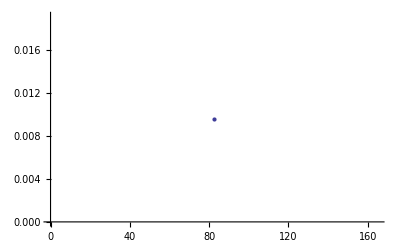

{a→0.00236815 (256.017+1.77424 {{1,{82.4551,1,2}},{2,Null},{3,Null},{4,Null},{5,Null},{6,Null},{7,Null},{8,Null},{9,Null},{10,Null},{11,Null},{12,Null},{13,Null},{14,Null},{15,Null},{16,{82.4456,0,1}},{17,Null},{18,Null},{19,Null},{20,Null},{21,Null},{22,Null},{23,Null},{24,Null},{25,Null},{26,Null},{27,Null},{28,Null},{29,Null},{30,Null}}⟦2,2,1⟧+0.648281 {{1,{82.4551,1,2}},{2,Null},{3,Null},{4,Null},{5,Null},{6,Null},{7,Null},{8,Null},{9,Null},{10,Null},{11,Null},{12,Null},{13,Null},{14,Null},{15,Null},{16,{82.4456,0,1}},{17,Null},{18,Null},{19,Null},{20,Null},{21,Null},{22,Null},{23,Null},{24,Null},{25,Null},{26,Null},{27,Null},{28,Null},{29,Null},{30,Null}}⟦3,2,1⟧-0.272961 {{1,{82.4551,1,2}},{2,Null},{3,Null},{4,Null},{5,Null},{6,Null},{7,Null},{8,Null},{9,Null},{10,Null},{11,Null},{12,Null},{13,Null},{14,Null},{15,Null},{16,{82.4456,0,1}},{17,Null},{18,Null},{19,Null},{20,Null},{21,Null},{22,Null},{23,Null},{24,Null},{25,Null},{26,Null},{27,Null},{28,Null},{29,Null},{30,Null}}⟦4,2,1⟧-0.989482 {{1,{82.4551,1,2}},{2,Null},{3,Null},{4,Null},{5,Null},{6,Null},{7,Null},{8,Null},{9,Null},{10,Null},{11,Null},{12,Null},{13,Null},{14,Null},{15,Null},{16,{82.4456,0,1}},{17,Null},{18,Null},{19,Null},{20,Null},{21,Null},{22,Null},{23,Null},{24,Null},{25,Null},{26,Null},{27,Null},{28,Null},{29,Null},{30,Null}}⟦5,2,1⟧-1.50128 {{1,{82.4551,1,2}},{2,Null},{3,Null},{4,Null},{5,Null},{6,Null},{7,Null},{8,Null},{9,Null},{10,Null},{11,Null},{12,Null},{13,Null},{14,Null},{15,Null},{16,{82.4456,0,1}},{17,Null},{18,Null},{19,Null},{20,Null},{21,Null},{22,Null},{23,Null},{24,Null},{25,Null},{26,Null},{27,Null},{28,Null},{29,Null},{30,Null}}⟦6,2,1⟧-1.80836 {{1,{82.4551,1,2}},{2,Null},{3,Null},{4,Null},{5,Null},{6,Null},{7,Null},{8,Null},{9,Null},{10,Null},{11,Null},{12,Null},{13,Null},{14,Null},{15,Null},{16,{82.4456,0,1}},{17,Null},{18,Null},{19,Null},{20,Null},{21,Null},{22,Null},{23,Null},{24,Null},{25,Null},{26,Null},{27,Null},{28,Null},{29,Null},{30,Null}}⟦7,2,1⟧-1.91072 {{1,{82.4551,1,2}},{2,Null},{3,Null},{4,Null},{5,Null},{6,Null},{7,Null},{8,Null},{9,Null},{10,Null},{11,Null},{12,Null},{13,Null},{14,Null},{15,Null},{16,{82.4456,0,1}},{17,Null},{18,Null},{19,Null},{20,Null},{21,Null},{22,Null},{23,Null},{24,Null},{25,Null},{26,Null},{27,Null},{28,Null},{29,Null},{30,Null}}⟦8,2,1⟧-1.80836 {{1,{82.4551,1,2}},{2,Null},{3,Null},{4,Null},{5,Null},{6,Null},{7,Null},{8,Null},{9,Null},{10,Null},{11,Null},{12,Null},{13,Null},{14,Null},{15,Null},{16,{82.4456,0,1}},{17,Null},{18,Null},{19,Null},{20,Null},{21,Null},{22,Null},{23,Null},{24,Null},{25,Null},{26,Null},{27,Null},{28,Null},{29,Null},{30,Null}}⟦9,2,1⟧-1.50128 {{1,{82.4551,1,2}},{2,Null},{3,Null},{4,Null},{5,Null},{6,Null},{7,Null},{8,Null},{9,Null},{10,Null},{11,Null},{12,Null},{13,Null},{14,Null},{15,Null},{16,{82.4456,0,1}},{17,Null},{18,Null},{19,Null},{20,Null},{21,Null},{22,Null},{23,Null},{24,Null},{25,Null},{26,Null},{27,Null},{28,Null},{29,Null},{30,Null}}⟦10,2,1⟧-0.989482 {{1,{82.4551,1,2}},{2,Null},{3,Null},{4,Null},{5,Null},{6,Null},{7,Null},{8,Null},{9,Null},{10,Null},{11,Null},{12,Null},{13,Null},{14,Null},{15,Null},{16,{82.4456,0,1}},{17,Null},{18,Null},{19,Null},{20,Null},{21,Null},{22,Null},{23,Null},{24,Null},{25,Null},{26,Null},{27,Null},{28,Null},{29,Null},{30,Null}}⟦11,2,1⟧-0.272961 {{1,{82.4551,1,2}},{2,Null},{3,Null},{4,Null},{5,Null},{6,Null},{7,Null},{8,Null},{9,Null},{10,Null},{11,Null},{12,Null},{13,Null},{14,Null},{15,Null},{16,{82.4456,0,1}},{17,Null},{18,Null},{19,Null},{20,Null},{21,Null},{22,Null},{23,Null},{24,Null},{25,Null},{26,Null},{27,Null},{28,Null},{29,Null},{30,Null}}⟦12,2,1⟧+0.648281 {{1,{82.4551,1,2}},{2,Null},{3,Null},{4,Null},{5,Null},{6,Null},{7,Null},{8,Null},{9,Null},{10,Null},{11,Null},{12,Null},{13,Null},{14,Null},{15,Null},{16,{82.4456,0,1}},{17,Null},{18,Null},{19,Null},{20,Null},{21,Null},{22,Null},{23,Null},{24,Null},{25,Null},{26,Null},{27,Null},{28,Null},{29,Null},{30,Null}}⟦13,2,1⟧+1.77424 {{1,{82.4551,1,2}},{2,Null},{3,Null},{4,Null},{5,Null},{6,Null},{7,Null},{8,Null},{9,Null},{10,Null},{11,Null},{12,Null},{13,Null},{14,Null},{15,Null},{16,{82.4456,0,1}},{17,Null},{18,Null},{19,Null},{20,Null},{21,Null},{22,Null},{23,Null},{24,Null},{25,Null},{26,Null},{27,Null},{28,Null},{29,Null},{30,Null}}⟦14,2,1⟧+3.10493 {{1,{82.4551,1,2}},{2,Null},{3,Null},{4,Null},{5,Null},{6,Null},{7,Null},{8,Null},{9,Null},{10,Null},{11,Null},{12,Null},{13,Null},{14,Null},{15,Null},{16,{82.4456,0,1}},{17,Null},{18,Null},{19,Null},{20,Null},{21,Null},{22,Null},{23,Null},{24,Null},{25,Null},{26,Null},{27,Null},{28,Null},{29,Null},{30,Null}}⟦15,2,1⟧),b→0.0283981 (-414.182-3.12188 {{1,{82.4551,1,2}},{2,Null},{3,Null},{4,Null},{5,Null},{6,Null},{7,Null},{8,Null},{9,Null},{10,Null},{11,Null},{12,Null},{13,Null},{14,Null},{15,Null},{16,{82.4456,0,1}},{17,Null},{18,Null},{19,Null},{20,Null},{21,Null},{22,Null},{23,Null},{24,Null},{25,Null},{26,Null},{27,Null},{28,Null},{29,Null},{30,Null}}⟦2,2,1⟧-1.49379 {{1,{82.4551,1,2}},{2,Null},{3,Null},{4,Null},{5,Null},{6,Null},{7,Null},{8,Null},{9,Null},{10,Null},{11,Null},{12,Null},{13,Null},{14,Null},{15,Null},{16,{82.4456,0,1}},{17,Null},{18,Null},{19,Null},{20,Null},{21,Null},{22,Null},{23,Null},{24,Null},{25,Null},{26,Null},{27,Null},{28,Null},{29,Null},{30,Null}}⟦3,2,1⟧-0.138851 {{1,{82.4551,1,2}},{2,Null},{3,Null},{4,Null},{5,Null},{6,Null},{7,Null},{8,Null},{9,Null},{10,Null},{11,Null},{12,Null},{13,Null},{14,Null},{15,Null},{16,{82.4456,0,1}},{17,Null},{18,Null},{19,Null},{20,Null},{21,Null},{22,Null},{23,Null},{24,Null},{25,Null},{26,Null},{27,Null},{28,Null},{29,Null},{30,Null}}⟦4,2,1⟧+0.942938 {{1,{82.4551,1,2}},{2,Null},{3,Null},{4,Null},{5,Null},{6,Null},{7,Null},{8,Null},{9,Null},{10,Null},{11,Null},{12,Null},{13,Null},{14,Null},{15,Null},{16,{82.4456,0,1}},{17,Null},{18,Null},{19,Null},{20,Null},{21,Null},{22,Null},{23,Null},{24,Null},{25,Null},{26,Null},{27,Null},{28,Null},{29,Null},{30,Null}}⟦5,2,1⟧+1.75158 {{1,{82.4551,1,2}},{2,Null},{3,Null},{4,Null},{5,Null},{6,Null},{7,Null},{8,Null},{9,Null},{10,Null},{11,Null},{12,Null},{13,Null},{14,Null},{15,Null},{16,{82.4456,0,1}},{17,Null},{18,Null},{19,Null},{20,Null},{21,Null},{22,Null},{23,Null},{24,Null},{25,Null},{26,Null},{27,Null},{28,Null},{29,Null},{30,Null}}⟦6,2,1⟧+2.28707 {{1,{82.4551,1,2}},{2,Null},{3,Null},{4,Null},{5,Null},{6,Null},{7,Null},{8,Null},{9,Null},{10,Null},{11,Null},{12,Null},{13,Null},{14,Null},{15,Null},{16,{82.4456,0,1}},{17,Null},{18,Null},{19,Null},{20,Null},{21,Null},{22,Null},{23,Null},{24,Null},{25,Null},{26,Null},{27,Null},{28,Null},{29,Null},{30,Null}}⟦7,2,1⟧+2.5494 {{1,{82.4551,1,2}},{2,Null},{3,Null},{4,Null},{5,Null},{6,Null},{7,Null},{8,Null},{9,Null},{10,Null},{11,Null},{12,Null},{13,Null},{14,Null},{15,Null},{16,{82.4456,0,1}},{17,Null},{18,Null},{19,Null},{20,Null},{21,Null},{22,Null},{23,Null},{24,Null},{25,Null},{26,Null},{27,Null},{28,Null},{29,Null},{30,Null}}⟦8,2,1⟧+2.53859 {{1,{82.4551,1,2}},{2,Null},{3,Null},{4,Null},{5,Null},{6,Null},{7,Null},{8,Null},{9,Null},{10,Null},{11,Null},{12,Null},{13,Null},{14,Null},{15,Null},{16,{82.4456,0,1}},{17,Null},{18,Null},{19,Null},{20,Null},{21,Null},{22,Null},{23,Null},{24,Null},{25,Null},{26,Null},{27,Null},{28,Null},{29,Null},{30,Null}}⟦9,2,1⟧+2.25463 {{1,{82.4551,1,2}},{2,Null},{3,Null},{4,Null},{5,Null},{6,Null},{7,Null},{8,Null},{9,Null},{10,Null},{11,Null},{12,Null},{13,Null},{14,Null},{15,Null},{16,{82.4456,0,1}},{17,Null},{18,Null},{19,Null},{20,Null},{21,Null},{22,Null},{23,Null},{24,Null},{25,Null},{26,Null},{27,Null},{28,Null},{29,Null},{30,Null}}⟦10,2,1⟧+1.69752 {{1,{82.4551,1,2}},{2,Null},{3,Null},{4,Null},{5,Null},{6,Null},{7,Null},{8,Null},{9,Null},{10,Null},{11,Null},{12,Null},{13,Null},{14,Null},{15,Null},{16,{82.4456,0,1}},{17,Null},{18,Null},{19,Null},{20,Null},{21,Null},{22,Null},{23,Null},{24,Null},{25,Null},{26,Null},{27,Null},{28,Null},{29,Null},{30,Null}}⟦11,2,1⟧+0.867252 {{1,{82.4551,1,2}},{2,Null},{3,Null},{4,Null},{5,Null},{6,Null},{7,Null},{8,Null},{9,Null},{10,Null},{11,Null},{12,Null},{13,Null},{14,Null},{15,Null},{16,{82.4456,0,1}},{17,Null},{18,Null},{19,Null},{20,Null},{21,Null},{22,Null},{23,Null},{24,Null},{25,Null},{26,Null},{27,Null},{28,Null},{29,Null},{30,Null}}⟦12,2,1⟧-0.236161 {{1,{82.4551,1,2}},{2,Null},{3,Null},{4,Null},{5,Null},{6,Null},{7,Null},{8,Null},{9,Null},{10,Null},{11,Null},{12,Null},{13,Null},{14,Null},{15,Null},{16,{82.4456,0,1}},{17,Null},{18,Null},{19,Null},{20,Null},{21,Null},{22,Null},{23,Null},{24,Null},{25,Null},{26,Null},{27,Null},{28,Null},{29,Null},{30,Null}}⟦13,2,1⟧-1.61273 {{1,{82.4551,1,2}},{2,Null},{3,Null},{4,Null},{5,Null},{6,Null},{7,Null},{8,Null},{9,Null},{10,Null},{11,Null},{12,Null},{13,Null},{14,Null},{15,Null},{16,{82.4456,0,1}},{17,Null},{18,Null},{19,Null},{20,Null},{21,Null},{22,Null},{23,Null},{24,Null},{25,Null},{26,Null},{27,Null},{28,Null},{29,Null},{30,Null}}⟦14,2,1⟧-3.26244 {{1,{82.4551,1,2}},{2,Null},{3,Null},{4,Null},{5,Null},{6,Null},{7,Null},{8,Null},{9,Null},{10,Null},{11,Null},{12,Null},{13,Null},{14,Null},{15,Null},{16,{82.4456,0,1}},{17,Null},{18,Null},{19,Null},{20,Null},{21,Null},{22,Null},{23,Null},{24,Null},{25,Null},{26,Null},{27,Null},{28,Null},{29,Null},{30,Null}}⟦15,2,1⟧),c→0.258199 (191.608+1.65985 {{1,{82.4551,1,2}},{2,Null},{3,Null},{4,Null},{5,Null},{6,Null},{7,Null},{8,Null},{9,Null},{10,Null},{11,Null},{12,Null},{13,Null},{14,Null},{15,Null},{16,{82.4456,0,1}},{17,Null},{18,Null},{19,Null},{20,Null},{21,Null},{22,Null},{23,Null},{24,Null},{25,Null},{26,Null},{27,Null},{28,Null},{29,Null},{30,Null}}⟦2,2,1⟧+1.08103 {{1,{82.4551,1,2}},{2,Null},{3,Null},{4,Null},{5,Null},{6,Null},{7,Null},{8,Null},{9,Null},{10,Null},{11,Null},{12,Null},{13,Null},{14,Null},{15,Null},{16,{82.4456,0,1}},{17,Null},{18,Null},{19,Null},{20,Null},{21,Null},{22,Null},{23,Null},{24,Null},{25,Null},{26,Null},{27,Null},{28,Null},{29,Null},{30,Null}}⟦3,2,1⟧+0.587332 {{1,{82.4551,1,2}},{2,Null},{3,Null},{4,Null},{5,Null},{6,Null},{7,Null},{8,Null},{9,Null},{10,Null},{11,Null},{12,Null},{13,Null},{14,Null},{15,Null},{16,{82.4456,0,1}},{17,Null},{18,Null},{19,Null},{20,Null},{21,Null},{22,Null},{23,Null},{24,Null},{25,Null},{26,Null},{27,Null},{28,Null},{29,Null},{30,Null}}⟦4,2,1⟧+0.178753 {{1,{82.4551,1,2}},{2,Null},{3,Null},{4,Null},{5,Null},{6,Null},{7,Null},{8,Null},{9,Null},{10,Null},{11,Null},{12,Null},{13,Null},{14,Null},{15,Null},{16,{82.4456,0,1}},{17,Null},{18,Null},{19,Null},{20,Null},{21,Null},{22,Null},{23,Null},{24,Null},{25,Null},{26,Null},{27,Null},{28,Null},{29,Null},{30,Null}}⟦5,2,1⟧-0.144705 {{1,{82.4551,1,2}},{2,Null},{3,Null},{4,Null},{5,Null},{6,Null},{7,Null},{8,Null},{9,Null},{10,Null},{11,Null},{12,Null},{13,Null},{14,Null},{15,Null},{16,{82.4456,0,1}},{17,Null},{18,Null},{19,Null},{20,Null},{21,Null},{22,Null},{23,Null},{24,Null},{25,Null},{26,Null},{27,Null},{28,Null},{29,Null},{30,Null}}⟦6,2,1⟧-0.383042 {{1,{82.4551,1,2}},{2,Null},{3,Null},{4,Null},{5,Null},{6,Null},{7,Null},{8,Null},{9,Null},{10,Null},{11,Null},{12,Null},{13,Null},{14,Null},{15,Null},{16,{82.4456,0,1}},{17,Null},{18,Null},{19,Null},{20,Null},{21,Null},{22,Null},{23,Null},{24,Null},{25,Null},{26,Null},{27,Null},{28,Null},{29,Null},{30,Null}}⟦7,2,1⟧-0.536259 {{1,{82.4551,1,2}},{2,Null},{3,Null},{4,Null},{5,Null},{6,Null},{7,Null},{8,Null},{9,Null},{10,Null},{11,Null},{12,Null},{13,Null},{14,Null},{15,Null},{16,{82.4456,0,1}},{17,Null},{18,Null},{19,Null},{20,Null},{21,Null},{22,Null},{23,Null},{24,Null},{25,Null},{26,Null},{27,Null},{28,Null},{29,Null},{30,Null}}⟦8,2,1⟧-0.604356 {{1,{82.4551,1,2}},{2,Null},{3,Null},{4,Null},{5,Null},{6,Null},{7,Null},{8,Null},{9,Null},{10,Null},{11,Null},{12,Null},{13,Null},{14,Null},{15,Null},{16,{82.4456,0,1}},{17,Null},{18,Null},{19,Null},{20,Null},{21,Null},{22,Null},{23,Null},{24,Null},{25,Null},{26,Null},{27,Null},{28,Null},{29,Null},{30,Null}}⟦9,2,1⟧-0.587332 {{1,{82.4551,1,2}},{2,Null},{3,Null},{4,Null},{5,Null},{6,Null},{7,Null},{8,Null},{9,Null},{10,Null},{11,Null},{12,Null},{13,Null},{14,Null},{15,Null},{16,{82.4456,0,1}},{17,Null},{18,Null},{19,Null},{20,Null},{21,Null},{22,Null},{23,Null},{24,Null},{25,Null},{26,Null},{27,Null},{28,Null},{29,Null},{30,Null}}⟦10,2,1⟧-0.485187 {{1,{82.4551,1,2}},{2,Null},{3,Null},{4,Null},{5,Null},{6,Null},{7,Null},{8,Null},{9,Null},{10,Null},{11,Null},{12,Null},{13,Null},{14,Null},{15,Null},{16,{82.4456,0,1}},{17,Null},{18,Null},{19,Null},{20,Null},{21,Null},{22,Null},{23,Null},{24,Null},{25,Null},{26,Null},{27,Null},{28,Null},{29,Null},{30,Null}}⟦11,2,1⟧-0.297922 {{1,{82.4551,1,2}},{2,Null},{3,Null},{4,Null},{5,Null},{6,Null},{7,Null},{8,Null},{9,Null},{10,Null},{11,Null},{12,Null},{13,Null},{14,Null},{15,Null},{16,{82.4456,0,1}},{17,Null},{18,Null},{19,Null},{20,Null},{21,Null},{22,Null},{23,Null},{24,Null},{25,Null},{26,Null},{27,Null},{28,Null},{29,Null},{30,Null}}⟦12,2,1⟧-0.0255362 {{1,{82.4551,1,2}},{2,Null},{3,Null},{4,Null},{5,Null},{6,Null},{7,Null},{8,Null},{9,Null},{10,Null},{11,Null},{12,Null},{13,Null},{14,Null},{15,Null},{16,{82.4456,0,1}},{17,Null},{18,Null},{19,Null},{20,Null},{21,Null},{22,Null},{23,Null},{24,Null},{25,Null},{26,Null},{27,Null},{28,Null},{29,Null},{30,Null}}⟦13,2,1⟧+0.33197 {{1,{82.4551,1,2}},{2,Null},{3,Null},{4,Null},{5,Null},{6,Null},{7,Null},{8,Null},{9,Null},{10,Null},{11,Null},{12,Null},{13,Null},{14,Null},{15,Null},{16,{82.4456,0,1}},{17,Null},{18,Null},{19,Null},{20,Null},{21,Null},{22,Null},{23,Null},{24,Null},{25,Null},{26,Null},{27,Null},{28,Null},{29,Null},{30,Null}}⟦14,2,1⟧+0.774597 {{1,{82.4551,1,2}},{2,Null},{3,Null},{4,Null},{5,Null},{6,Null},{7,Null},{8,Null},{9,Null},{10,Null},{11,Null},{12,Null},{13,Null},{14,Null},{15,Null},{16,{82.4456,0,1}},{17,Null},{18,Null},{19,Null},{20,Null},{21,Null},{22,Null},{23,Null},{24,Null},{25,Null},{26,Null},{27,Null},{28,Null},{29,Null},{30,Null}}⟦15,2,1⟧)}

-Graphics-

Starting range calculation for l = 8

Found one!

Found one!

Found one!

«12 more identical outputs»

{{105.957,106.808},{235.166,235.872},{320.528,321.07},{384.36,385.274},{454.949,455.754},{493.044,493.772},{572.666,573.335},{614.722,615.345},{658.527,659.08},{703.749,704.275},{750.901,751.403},{798.862,799.79},{848.619,849.485},{900.551,901.366},{953.506,954.279}}

Starting first refinement for l = 8

***Beginning to calculate the 1th lambda, part 13

***Beginning to calculate the 2th lambda, part 5

***Beginning to calculate the 3th lambda, part 7

***Beginning to calculate the 4th lambda, part 12

***Beginning to calculate the 5th lambda, part 8

***Beginning to calculate the 6th lambda, part 14

***Beginning to calculate the 7th lambda, part 3

***Beginning to calculate the 8th lambda, part 1

***Beginning to calculate the 9th lambda, part 15

***Beginning to calculate the 10th lambda, part 10

***Beginning to calculate the 11th lambda, part 9

***Beginning to calculate the 12th lambda, part 11

***Beginning to calculate the 13th lambda, part 6

***Beginning to calculate the 14th lambda, part 2

***Beginning to calculate the 15th lambda, part 4

Fail!

Pass!

Bisecting. Midpoint is 320.799

Fail!

Fail!

Fail!

«1 more identical outputs»

Bisecting. Midpoint is 319.663

Pass!

Bisecting. Midpoint is 384.817

Fail!

Fail!

Fail!

«1 more identical outputs»

Bisecting. Midpoint is 320.231

Bisecting. Midpoint is 320.515

Bisecting. Midpoint is 386.045

Fail!

Fail!

Fail!

Bisecting. Midpoint is 320.373

Bisecting. Midpoint is 386.659

Fail!

Bisecting. Midpoint is 320.444

Bisecting. Midpoint is 386.967

Bisecting. Midpoint is 386.813

Bisecting. Midpoint is 386.736

Starting second refinement for l = 8

Part::partd: Part specification {{1, Null}, {2, Null}, {3, {320.444, 1, 2}}, {4, {386.736, 1, 2}}, {5, Null}, {6, Null}, {7, Null}, {8, Null}, {9, Null}, {10, Null}, {11, Null}, {12, Null}, {13, Null}, {14, Null}, {15, Null}} ⟦ 9, 2, 1 ⟧ is longer than depth of object.

General::stop: Further output of Part :: "partd" will be suppressed during this calculation.

***Beginning to calculate the 1th lambda, part 9

***Beginning to calculate the 2th lambda, part 3

***Beginning to calculate the 3th lambda, part 12

***Beginning to calculate the 4th lambda, part 14

***Beginning to calculate the 5th lambda, part 8

***Beginning to calculate the 6th lambda, part 10

***Beginning to calculate the 7th lambda, part 13

***Beginning to calculate the 8th lambda, part 15

***Beginning to calculate the 9th lambda, part 5

***Beginning to calculate the 10th lambda, part 7

***Beginning to calculate the 11th lambda, part 1

***Beginning to calculate the 12th lambda, part 2

***Beginning to calculate the 13th lambda, part 4

***Beginning to calculate the 14th lambda, part 6

***Beginning to calculate the 15th lambda, part 11

SparseArray::dims: The dimensions {Round[10.\ Round[40\ {{« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}} ⟦ 9, 2, 1 ⟧]], Round[10.\ Round[40\ {{« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}} ⟦ 9, 2, 1 ⟧]]} in SparseArray[{{n$_, n$_} → 199.99999999999997`  + 199.99999999999997`/n$^2 - 20.` ⅇ^-0.1` n$ Power[« 2 »]/n$, {n$_, m$_}/;Abs[n$ + Times[« 2 »]] == 1 → -99.99999999999999`}, {Round[10.` Round[40 {« 15 »} ⟦ 9, 2, 1 ⟧]], Round[10.` Round[40 {« 15 »} ⟦ 9, 2, 1 ⟧]]}, 0.`] are not given as a list of positive machine integers.

Pass!

SparseArray::dims: The dimensions {Round[10.\ Round[40\ {{« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}} ⟦ 12, 2, 1 ⟧]], Round[10.\ Round[40\ {{« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}} ⟦ 12, 2, 1 ⟧]]} in SparseArray[{{n$_, n$_} → 199.99999999999997`  + 199.99999999999997`/n$^2 - 20.` ⅇ^-0.1` n$ Power[« 2 »]/n$, {n$_, m$_}/;Abs[n$ + Times[« 2 »]] == 1 → -99.99999999999999`}, {Round[10.` Round[40 {« 15 »} ⟦ 12, 2, 1 ⟧]], Round[10.` Round[40 {« 15 »} ⟦ 12, 2, 1 ⟧]]}, 0.`] are not given as a list of positive machine integers.

SparseArray::dims: The dimensions {Round[10.\ Round[40\ {{« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}} ⟦ 14, 2, 1 ⟧]], Round[10.\ Round[40\ {{« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}} ⟦ 14, 2, 1 ⟧]]} in SparseArray[{{n$_, n$_} → 199.99999999999997`  + 199.99999999999997`/n$^2 - 20.` ⅇ^-0.1` n$ Power[« 2 »]/n$, {n$_, m$_}/;Abs[n$ + Times[« 2 »]] == 1 → -99.99999999999999`}, {Round[10.` Round[40 {« 15 »} ⟦ 14, 2, 1 ⟧]], Round[10.` Round[40 {« 15 »} ⟦ 14, 2, 1 ⟧]]}, 0.`] are not given as a list of positive machine integers.

SparseArray::dims: The dimensions {Round[10.\ Round[40\ {{« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}} ⟦ 8, 2, 1 ⟧]], Round[10.\ Round[40\ {{« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}} ⟦ 8, 2, 1 ⟧]]} in SparseArray[{{n$_, n$_} → 199.99999999999997`  + 199.99999999999997`/n$^2 - 20.` ⅇ^-0.1` n$ Power[« 2 »]/n$, {n$_, m$_}/;Abs[n$ + Times[« 2 »]] == 1 → -99.99999999999999`}, {Round[10.` Round[40 {« 15 »} ⟦ 8, 2, 1 ⟧]], Round[10.` Round[40 {« 15 »} ⟦ 8, 2, 1 ⟧]]}, 0.`] are not given as a list of positive machine integers.

SparseArray::dims: The dimensions {Round[10.\ Round[40\ {{« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}} ⟦ 10, 2, 1 ⟧]], Round[10.\ Round[40\ {{« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}} ⟦ 10, 2, 1 ⟧]]} in SparseArray[{{n$_, n$_} → 199.99999999999997`  + 199.99999999999997`/n$^2 - 20.` ⅇ^-0.1` n$ Power[« 2 »]/n$, {n$_, m$_}/;Abs[n$ + Times[« 2 »]] == 1 → -99.99999999999999`}, {Round[10.` Round[40 {« 15 »} ⟦ 10, 2, 1 ⟧]], Round[10.` Round[40 {« 15 »} ⟦ 10, 2, 1 ⟧]]}, 0.`] are not given as a list of positive machine integers.

SparseArray::dims: The dimensions {Round[10.\ Round[40\ {{« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}} ⟦ 13, 2, 1 ⟧]], Round[10.\ Round[40\ {{« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}} ⟦ 13, 2, 1 ⟧]]} in SparseArray[{{n$_, n$_} → 199.99999999999997`  + 199.99999999999997`/n$^2 - 20.` ⅇ^-0.1` n$ Power[« 2 »]/n$, {n$_, m$_}/;Abs[n$ + Times[« 2 »]] == 1 → -99.99999999999999`}, {Round[10.` Round[40 {« 15 »} ⟦ 13, 2, 1 ⟧]], Round[10.` Round[40 {« 15 »} ⟦ 13, 2, 1 ⟧]]}, 0.`] are not given as a list of positive machine integers.

SparseArray::dims: The dimensions {Round[10.\ Round[40\ {{« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}} ⟦ 15, 2, 1 ⟧]], Round[10.\ Round[40\ {{« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}} ⟦ 15, 2, 1 ⟧]]} in SparseArray[{{n$_, n$_} → 199.99999999999997`  + 199.99999999999997`/n$^2 - 20.` ⅇ^-0.1` n$ Power[« 2 »]/n$, {n$_, m$_}/;Abs[n$ + Times[« 2 »]] == 1 → -99.99999999999999`}, {Round[10.` Round[40 {« 15 »} ⟦ 15, 2, 1 ⟧]], Round[10.` Round[40 {« 15 »} ⟦ 15, 2, 1 ⟧]]}, 0.`] are not given as a list of positive machine integers.

SparseArray::dims: The dimensions {Round[10.\ Round[40\ {{« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}} ⟦ 5, 2, 1 ⟧]], Round[10.\ Round[40\ {{« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}} ⟦ 5, 2, 1 ⟧]]} in SparseArray[{{n$_, n$_} → 199.99999999999997`  + 199.99999999999997`/n$^2 - 20.` ⅇ^-0.1` n$ Power[« 2 »]/n$, {n$_, m$_}/;Abs[n$ + Times[« 2 »]] == 1 → -99.99999999999999`}, {Round[10.` Round[40 {« 15 »} ⟦ 5, 2, 1 ⟧]], Round[10.` Round[40 {« 15 »} ⟦ 5, 2, 1 ⟧]]}, 0.`] are not given as a list of positive machine integers.

SparseArray::dims: The dimensions {Round[10.\ Round[40\ {{« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}} ⟦ 7, 2, 1 ⟧]], Round[10.\ Round[40\ {{« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}} ⟦ 7, 2, 1 ⟧]]} in SparseArray[{{n$_, n$_} → 199.99999999999997`  + 199.99999999999997`/n$^2 - 20.` ⅇ^-0.1` n$ Power[« 2 »]/n$, {n$_, m$_}/;Abs[n$ + Times[« 2 »]] == 1 → -99.99999999999999`}, {Round[10.` Round[40 {« 15 »} ⟦ 7, 2, 1 ⟧]], Round[10.` Round[40 {« 15 »} ⟦ 7, 2, 1 ⟧]]}, 0.`] are not given as a list of positive machine integers.

SparseArray::dims: The dimensions {Round[10.\ Round[40\ {{« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}} ⟦ 1, 2, 1 ⟧]], Round[10.\ Round[40\ {{« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}} ⟦ 1, 2, 1 ⟧]]} in SparseArray[{{n$_, n$_} → 199.99999999999997`  + 199.99999999999997`/n$^2 - 20.` ⅇ^-0.1` n$ Power[« 2 »]/n$, {n$_, m$_}/;Abs[n$ + Times[« 2 »]] == 1 → -99.99999999999999`}, {Round[10.` Round[40 {« 15 »} ⟦ 1, 2, 1 ⟧]], Round[10.` Round[40 {« 15 »} ⟦ 1, 2, 1 ⟧]]}, 0.`] are not given as a list of positive machine integers.

SparseArray::dims: The dimensions {Round[10.\ Round[40\ {{« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}} ⟦ 2, 2, 1 ⟧]], Round[10.\ Round[40\ {{« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}} ⟦ 2, 2, 1 ⟧]]} in SparseArray[{{n$_, n$_} → 199.99999999999997`  + 199.99999999999997`/n$^2 - 20.` ⅇ^-0.1` n$ Power[« 2 »]/n$, {n$_, m$_}/;Abs[n$ + Times[« 2 »]] == 1 → -99.99999999999999`}, {Round[10.` Round[40 {« 15 »} ⟦ 2, 2, 1 ⟧]], Round[10.` Round[40 {« 15 »} ⟦ 2, 2, 1 ⟧]]}, 0.`] are not given as a list of positive machine integers.

SparseArray::dims: The dimensions {Round[10.\ Round[40\ {{« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}} ⟦ 6, 2, 1 ⟧]], Round[10.\ Round[40\ {{« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}} ⟦ 6, 2, 1 ⟧]]} in SparseArray[{{n$_, n$_} → 199.99999999999997`  + 199.99999999999997`/n$^2 - 20.` ⅇ^-0.1` n$ Power[« 2 »]/n$, {n$_, m$_}/;Abs[n$ + Times[« 2 »]] == 1 → -99.99999999999999`}, {Round[10.` Round[40 {« 15 »} ⟦ 6, 2, 1 ⟧]], Round[10.` Round[40 {« 15 »} ⟦ 6, 2, 1 ⟧]]}, 0.`] are not given as a list of positive machine integers.

SparseArray::dims: The dimensions {Round[10.\ Round[40\ {{« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}} ⟦ 11, 2, 1 ⟧]], Round[10.\ Round[40\ {{« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}} ⟦ 11, 2, 1 ⟧]]} in SparseArray[{{n$_, n$_} → 199.99999999999997`  + 199.99999999999997`/n$^2 - 20.` ⅇ^-0.1` n$ Power[« 2 »]/n$, {n$_, m$_}/;Abs[n$ + Times[« 2 »]] == 1 → -99.99999999999999`}, {Round[10.` Round[40 {« 15 »} ⟦ 11, 2, 1 ⟧]], Round[10.` Round[40 {« 15 »} ⟦ 11, 2, 1 ⟧]]}, 0.`] are not given as a list of positive machine integers.

Eigenvalues::matsq: Argument -25 at position 1 is not a non-empty square matrix.

Bisecting. Midpoint is 320.444

Eigenvalues::matsq: Argument -25 at position 1 is not a non-empty square matrix.

SparseArray::dims: The dimensions {Round[10.\ Round[40\ {{« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}} ⟦ 9, 2, 1 ⟧]], Round[10.\ Round[40\ {{« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}} ⟦ 9, 2, 1 ⟧]]} in SparseArray[{{n$_, n$_} → 199.99999999999997`  + 199.99999999999997`/n$^2 - 20.` ⅇ^-0.1` n$ Power[« 2 »]/n$, {n$_, m$_}/;Abs[n$ + Times[« 2 »]] == 1 → -99.99999999999999`}, {Round[10.` Round[40 {« 15 »} ⟦ 9, 2, 1 ⟧]], Round[10.` Round[40 {« 15 »} ⟦ 9, 2, 1 ⟧]]}, 0.`] are not given as a list of positive machine integers.

SparseArray::dims: The dimensions {Round[10.\ Round[40\ {{« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}} ⟦ 12, 2, 1 ⟧]], Round[10.\ Round[40\ {{« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}} ⟦ 12, 2, 1 ⟧]]} in SparseArray[{{n$_, n$_} → 199.99999999999997`  + 199.99999999999997`/n$^2 - 20.` ⅇ^-0.1` n$ Power[« 2 »]/n$, {n$_, m$_}/;Abs[n$ + Times[« 2 »]] == 1 → -99.99999999999999`}, {Round[10.` Round[40 {« 15 »} ⟦ 12, 2, 1 ⟧]], Round[10.` Round[40 {« 15 »} ⟦ 12, 2, 1 ⟧]]}, 0.`] are not given as a list of positive machine integers.

SparseArray::dims: The dimensions {Round[10.\ Round[40\ {{« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}} ⟦ 14, 2, 1 ⟧]], Round[10.\ Round[40\ {{« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}} ⟦ 14, 2, 1 ⟧]]} in SparseArray[{{n$_, n$_} → 199.99999999999997`  + 199.99999999999997`/n$^2 - 20.` ⅇ^-0.1` n$ Power[« 2 »]/n$, {n$_, m$_}/;Abs[n$ + Times[« 2 »]] == 1 → -99.99999999999999`}, {Round[10.` Round[40 {« 15 »} ⟦ 14, 2, 1 ⟧]], Round[10.` Round[40 {« 15 »} ⟦ 14, 2, 1 ⟧]]}, 0.`] are not given as a list of positive machine integers.

SparseArray::dims: The dimensions {Round[10.\ Round[40\ {{« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}} ⟦ 8, 2, 1 ⟧]], Round[10.\ Round[40\ {{« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}} ⟦ 8, 2, 1 ⟧]]} in SparseArray[{{n$_, n$_} → 199.99999999999997`  + 199.99999999999997`/n$^2 - 20.` ⅇ^-0.1` n$ Power[« 2 »]/n$, {n$_, m$_}/;Abs[n$ + Times[« 2 »]] == 1 → -99.99999999999999`}, {Round[10.` Round[40 {« 15 »} ⟦ 8, 2, 1 ⟧]], Round[10.` Round[40 {« 15 »} ⟦ 8, 2, 1 ⟧]]}, 0.`] are not given as a list of positive machine integers.

SparseArray::dims: The dimensions {Round[10.\ Round[40\ {{« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}} ⟦ 10, 2, 1 ⟧]], Round[10.\ Round[40\ {{« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}} ⟦ 10, 2, 1 ⟧]]} in SparseArray[{{n$_, n$_} → 199.99999999999997`  + 199.99999999999997`/n$^2 - 20.` ⅇ^-0.1` n$ Power[« 2 »]/n$, {n$_, m$_}/;Abs[n$ + Times[« 2 »]] == 1 → -99.99999999999999`}, {Round[10.` Round[40 {« 15 »} ⟦ 10, 2, 1 ⟧]], Round[10.` Round[40 {« 15 »} ⟦ 10, 2, 1 ⟧]]}, 0.`] are not given as a list of positive machine integers.

SparseArray::dims: The dimensions {Round[10.\ Round[40\ {{« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}} ⟦ 13, 2, 1 ⟧]], Round[10.\ Round[40\ {{« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}} ⟦ 13, 2, 1 ⟧]]} in SparseArray[{{n$_, n$_} → 199.99999999999997`  + 199.99999999999997`/n$^2 - 20.` ⅇ^-0.1` n$ Power[« 2 »]/n$, {n$_, m$_}/;Abs[n$ + Times[« 2 »]] == 1 → -99.99999999999999`}, {Round[10.` Round[40 {« 15 »} ⟦ 13, 2, 1 ⟧]], Round[10.` Round[40 {« 15 »} ⟦ 13, 2, 1 ⟧]]}, 0.`] are not given as a list of positive machine integers.

SparseArray::dims: The dimensions {Round[10.\ Round[40\ {{« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}} ⟦ 15, 2, 1 ⟧]], Round[10.\ Round[40\ {{« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}} ⟦ 15, 2, 1 ⟧]]} in SparseArray[{{n$_, n$_} → 199.99999999999997`  + 199.99999999999997`/n$^2 - 20.` ⅇ^-0.1` n$ Power[« 2 »]/n$, {n$_, m$_}/;Abs[n$ + Times[« 2 »]] == 1 → -99.99999999999999`}, {Round[10.` Round[40 {« 15 »} ⟦ 15, 2, 1 ⟧]], Round[10.` Round[40 {« 15 »} ⟦ 15, 2, 1 ⟧]]}, 0.`] are not given as a list of positive machine integers.

SparseArray::dims: The dimensions {Round[10.\ Round[40\ {{« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}} ⟦ 5, 2, 1 ⟧]], Round[10.\ Round[40\ {{« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}} ⟦ 5, 2, 1 ⟧]]} in SparseArray[{{n$_, n$_} → 199.99999999999997`  + 199.99999999999997`/n$^2 - 20.` ⅇ^-0.1` n$ Power[« 2 »]/n$, {n$_, m$_}/;Abs[n$ + Times[« 2 »]] == 1 → -99.99999999999999`}, {Round[10.` Round[40 {« 15 »} ⟦ 5, 2, 1 ⟧]], Round[10.` Round[40 {« 15 »} ⟦ 5, 2, 1 ⟧]]}, 0.`] are not given as a list of positive machine integers.

SparseArray::dims: The dimensions {Round[10.\ Round[40\ {{« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}} ⟦ 7, 2, 1 ⟧]], Round[10.\ Round[40\ {{« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}} ⟦ 7, 2, 1 ⟧]]} in SparseArray[{{n$_, n$_} → 199.99999999999997`  + 199.99999999999997`/n$^2 - 20.` ⅇ^-0.1` n$ Power[« 2 »]/n$, {n$_, m$_}/;Abs[n$ + Times[« 2 »]] == 1 → -99.99999999999999`}, {Round[10.` Round[40 {« 15 »} ⟦ 7, 2, 1 ⟧]], Round[10.` Round[40 {« 15 »} ⟦ 7, 2, 1 ⟧]]}, 0.`] are not given as a list of positive machine integers.

SparseArray::dims: The dimensions {Round[10.\ Round[40\ {{« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}} ⟦ 1, 2, 1 ⟧]], Round[10.\ Round[40\ {{« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}} ⟦ 1, 2, 1 ⟧]]} in SparseArray[{{n$_, n$_} → 199.99999999999997`  + 199.99999999999997`/n$^2 - 20.` ⅇ^-0.1` n$ Power[« 2 »]/n$, {n$_, m$_}/;Abs[n$ + Times[« 2 »]] == 1 → -99.99999999999999`}, {Round[10.` Round[40 {« 15 »} ⟦ 1, 2, 1 ⟧]], Round[10.` Round[40 {« 15 »} ⟦ 1, 2, 1 ⟧]]}, 0.`] are not given as a list of positive machine integers.

SparseArray::dims: The dimensions {Round[10.\ Round[40\ {{« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}} ⟦ 2, 2, 1 ⟧]], Round[10.\ Round[40\ {{« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}} ⟦ 2, 2, 1 ⟧]]} in SparseArray[{{n$_, n$_} → 199.99999999999997`  + 199.99999999999997`/n$^2 - 20.` ⅇ^-0.1` n$ Power[« 2 »]/n$, {n$_, m$_}/;Abs[n$ + Times[« 2 »]] == 1 → -99.99999999999999`}, {Round[10.` Round[40 {« 15 »} ⟦ 2, 2, 1 ⟧]], Round[10.` Round[40 {« 15 »} ⟦ 2, 2, 1 ⟧]]}, 0.`] are not given as a list of positive machine integers.

SparseArray::dims: The dimensions {Round[10.\ Round[40\ {{« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}} ⟦ 6, 2, 1 ⟧]], Round[10.\ Round[40\ {{« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}} ⟦ 6, 2, 1 ⟧]]} in SparseArray[{{n$_, n$_} → 199.99999999999997`  + 199.99999999999997`/n$^2 - 20.` ⅇ^-0.1` n$ Power[« 2 »]/n$, {n$_, m$_}/;Abs[n$ + Times[« 2 »]] == 1 → -99.99999999999999`}, {Round[10.` Round[40 {« 15 »} ⟦ 6, 2, 1 ⟧]], Round[10.` Round[40 {« 15 »} ⟦ 6, 2, 1 ⟧]]}, 0.`] are not given as a list of positive machine integers.

SparseArray::dims: The dimensions {Round[10.\ Round[40\ {{« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}} ⟦ 11, 2, 1 ⟧]], Round[10.\ Round[40\ {{« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}} ⟦ 11, 2, 1 ⟧]]} in SparseArray[{{n$_, n$_} → 199.99999999999997`  + 199.99999999999997`/n$^2 - 20.` ⅇ^-0.1` n$ Power[« 2 »]/n$, {n$_, m$_}/;Abs[n$ + Times[« 2 »]] == 1 → -99.99999999999999`}, {Round[10.` Round[40 {« 15 »} ⟦ 11, 2, 1 ⟧]], Round[10.` Round[40 {« 15 »} ⟦ 11, 2, 1 ⟧]]}, 0.`] are not given as a list of positive machine integers.

Eigenvalues::matsq: Argument -25 at position 1 is not a non-empty square matrix.

Fail!

Fail!

Fail!

«10 more identical outputs»

Pass!

Bisecting. Midpoint is 386.736

Bisecting. Midpoint is 320.069

Bisecting. Midpoint is 320.257

Bisecting. Midpoint is 387.111

Bisecting. Midpoint is 320.35

Bisecting. Midpoint is 320.397

Bisecting. Midpoint is 386.924

Bisecting. Midpoint is 320.421

Bisecting. Midpoint is 320.409

Bisecting. Midpoint is 386.83

Bisecting. Midpoint is 386.783

Bisecting. Midpoint is 386.807

Bisecting. Midpoint is 386.818

Starting main calculation for l = 8

Part::partd: Part specification {{1, Null}, {2, Null}, {3, {320.409, 1, 2}}, {4, {386.818, 1, 2}}, {5, Null}, {6, Null}, {7, Null}, {8, Null}, {9, Null}, {10, Null}, {11, Null}, {12, Null}, {13, Null}, {14, Null}, {15, Null}} ⟦ 9, 2, 1 ⟧ is longer than depth of object.

General::stop: Further output of Part :: "partd" will be suppressed during this calculation.

***Beginning to calculate the 1th lambda, part 24

***Beginning to calculate the 3th lambda, part 15

***Beginning to calculate the 5th lambda, part 14

***Beginning to calculate the 7th lambda, part 29

***Beginning to calculate the 9th lambda, part 17

***Beginning to calculate the 11th lambda, part 5

***Beginning to calculate the 13th lambda, part 12

***Beginning to calculate the 15th lambda, part 11

***Beginning to calculate the 17th lambda, part 6

***Beginning to calculate the 19th lambda, part 8

***Beginning to calculate the 20th lambda, part 20

***Beginning to calculate the 21th lambda, part 19

***Beginning to calculate the 22th lambda, part 10

***Beginning to calculate the 23th lambda, part 18

***Beginning to calculate the 24th lambda, part 21

***Beginning to calculate the 25th lambda, part 30

***Beginning to calculate the 26th lambda, part 3

***Beginning to calculate the 27th lambda, part 4

***Beginning to calculate the 28th lambda, part 2

***Beginning to calculate the 29th lambda, part 22

***Beginning to calculate the 30th lambda, part 28

SparseArray::dims: The dimensions {Round[10.\ Round[80\ {{« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}} ⟦ 9, 2, 1 ⟧]], Round[10.\ Round[80\ {{« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}} ⟦ 9, 2, 1 ⟧]]} in SparseArray[{{n$_, n$_} → 199.99999999999997`  + 199.99999999999997`/n$^2 - 20.` ⅇ^-0.1` n$ Power[« 2 »]/n$, {n$_, m$_}/;Abs[n$ + Times[« 2 »]] == 1 → -99.99999999999999`}, {Round[10.` Round[80 {« 15 »} ⟦ 9, 2, 1 ⟧]], Round[10.` Round[80 {« 15 »} ⟦ 9, 2, 1 ⟧]]}, 0.`] are not given as a list of positive machine integers.

SparseArray::dims: The dimensions {Round[10.\ Round[40\ {{« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}} ⟦ 15, 2, 1 ⟧]], Round[10.\ Round[40\ {{« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}} ⟦ 15, 2, 1 ⟧]]} in SparseArray[{{n$_, n$_} → 199.99999999999997`  + 199.99999999999997`/n$^2 - 20.` ⅇ^-0.1` n$ Power[« 2 »]/n$, {n$_, m$_}/;Abs[n$ + Times[« 2 »]] == 1 → -99.99999999999999`}, {Round[10.` Round[40 {« 15 »} ⟦ 15, 2, 1 ⟧]], Round[10.` Round[40 {« 15 »} ⟦ 15, 2, 1 ⟧]]}, 0.`] are not given as a list of positive machine integers.

SparseArray::dims: The dimensions {Round[10.\ Round[40\ {{« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}} ⟦ 14, 2, 1 ⟧]], Round[10.\ Round[40\ {{« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}} ⟦ 14, 2, 1 ⟧]]} in SparseArray[{{n$_, n$_} → 199.99999999999997`  + 199.99999999999997`/n$^2 - 20.` ⅇ^-0.1` n$ Power[« 2 »]/n$, {n$_, m$_}/;Abs[n$ + Times[« 2 »]] == 1 → -99.99999999999999`}, {Round[10.` Round[40 {« 15 »} ⟦ 14, 2, 1 ⟧]], Round[10.` Round[40 {« 15 »} ⟦ 14, 2, 1 ⟧]]}, 0.`] are not given as a list of positive machine integers.

SparseArray::dims: The dimensions {Round[10.\ Round[80\ {{« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}} ⟦ 14, 2, 1 ⟧]], Round[10.\ Round[80\ {{« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}} ⟦ 14, 2, 1 ⟧]]} in SparseArray[{{n$_, n$_} → 199.99999999999997`  + 199.99999999999997`/n$^2 - 20.` ⅇ^-0.1` n$ Power[« 2 »]/n$, {n$_, m$_}/;Abs[n$ + Times[« 2 »]] == 1 → -99.99999999999999`}, {Round[10.` Round[80 {« 15 »} ⟦ 14, 2, 1 ⟧]], Round[10.` Round[80 {« 15 »} ⟦ 14, 2, 1 ⟧]]}, 0.`] are not given as a list of positive machine integers.

SparseArray::dims: The dimensions {Round[10.\ Round[80\ {{« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}} ⟦ 2, 2, 1 ⟧]], Round[10.\ Round[80\ {{« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}} ⟦ 2, 2, 1 ⟧]]} in SparseArray[{{n$_, n$_} → 199.99999999999997`  + 199.99999999999997`/n$^2 - 20.` ⅇ^-0.1` n$ Power[« 2 »]/n$, {n$_, m$_}/;Abs[n$ + Times[« 2 »]] == 1 → -99.99999999999999`}, {Round[10.` Round[80 {« 15 »} ⟦ 2, 2, 1 ⟧]], Round[10.` Round[80 {« 15 »} ⟦ 2, 2, 1 ⟧]]}, 0.`] are not given as a list of positive machine integers.

SparseArray::dims: The dimensions {Round[10.\ Round[40\ {{« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}} ⟦ 5, 2, 1 ⟧]], Round[10.\ Round[40\ {{« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}} ⟦ 5, 2, 1 ⟧]]} in SparseArray[{{n$_, n$_} → 199.99999999999997`  + 199.99999999999997`/n$^2 - 20.` ⅇ^-0.1` n$ Power[« 2 »]/n$, {n$_, m$_}/;Abs[n$ + Times[« 2 »]] == 1 → -99.99999999999999`}, {Round[10.` Round[40 {« 15 »} ⟦ 5, 2, 1 ⟧]], Round[10.` Round[40 {« 15 »} ⟦ 5, 2, 1 ⟧]]}, 0.`] are not given as a list of positive machine integers.

SparseArray::dims: The dimensions {Round[10.\ Round[40\ {{« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}} ⟦ 12, 2, 1 ⟧]], Round[10.\ Round[40\ {{« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}} ⟦ 12, 2, 1 ⟧]]} in SparseArray[{{n$_, n$_} → 199.99999999999997`  + 199.99999999999997`/n$^2 - 20.` ⅇ^-0.1` n$ Power[« 2 »]/n$, {n$_, m$_}/;Abs[n$ + Times[« 2 »]] == 1 → -99.99999999999999`}, {Round[10.` Round[40 {« 15 »} ⟦ 12, 2, 1 ⟧]], Round[10.` Round[40 {« 15 »} ⟦ 12, 2, 1 ⟧]]}, 0.`] are not given as a list of positive machine integers.

SparseArray::dims: The dimensions {Round[10.\ Round[40\ {{« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}} ⟦ 11, 2, 1 ⟧]], Round[10.\ Round[40\ {{« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}} ⟦ 11, 2, 1 ⟧]]} in SparseArray[{{n$_, n$_} → 199.99999999999997`  + 199.99999999999997`/n$^2 - 20.` ⅇ^-0.1` n$ Power[« 2 »]/n$, {n$_, m$_}/;Abs[n$ + Times[« 2 »]] == 1 → -99.99999999999999`}, {Round[10.` Round[40 {« 15 »} ⟦ 11, 2, 1 ⟧]], Round[10.` Round[40 {« 15 »} ⟦ 11, 2, 1 ⟧]]}, 0.`] are not given as a list of positive machine integers.

SparseArray::dims: The dimensions {Round[10.\ Round[40\ {{« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}} ⟦ 6, 2, 1 ⟧]], Round[10.\ Round[40\ {{« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}} ⟦ 6, 2, 1 ⟧]]} in SparseArray[{{n$_, n$_} → 199.99999999999997`  + 199.99999999999997`/n$^2 - 20.` ⅇ^-0.1` n$ Power[« 2 »]/n$, {n$_, m$_}/;Abs[n$ + Times[« 2 »]] == 1 → -99.99999999999999`}, {Round[10.` Round[40 {« 15 »} ⟦ 6, 2, 1 ⟧]], Round[10.` Round[40 {« 15 »} ⟦ 6, 2, 1 ⟧]]}, 0.`] are not given as a list of positive machine integers.

SparseArray::dims: The dimensions {Round[10.\ Round[40\ {{« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}} ⟦ 8, 2, 1 ⟧]], Round[10.\ Round[40\ {{« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}} ⟦ 8, 2, 1 ⟧]]} in SparseArray[{{n$_, n$_} → 199.99999999999997`  + 199.99999999999997`/n$^2 - 20.` ⅇ^-0.1` n$ Power[« 2 »]/n$, {n$_, m$_}/;Abs[n$ + Times[« 2 »]] == 1 → -99.99999999999999`}, {Round[10.` Round[40 {« 15 »} ⟦ 8, 2, 1 ⟧]], Round[10.` Round[40 {« 15 »} ⟦ 8, 2, 1 ⟧]]}, 0.`] are not given as a list of positive machine integers.

SparseArray::dims: The dimensions {Round[10.\ Round[80\ {{« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}} ⟦ 5, 2, 1 ⟧]], Round[10.\ Round[80\ {{« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}} ⟦ 5, 2, 1 ⟧]]} in SparseArray[{{n$_, n$_} → 199.99999999999997`  + 199.99999999999997`/n$^2 - 20.` ⅇ^-0.1` n$ Power[« 2 »]/n$, {n$_, m$_}/;Abs[n$ + Times[« 2 »]] == 1 → -99.99999999999999`}, {Round[10.` Round[80 {« 15 »} ⟦ 5, 2, 1 ⟧]], Round[10.` Round[80 {« 15 »} ⟦ 5, 2, 1 ⟧]]}, 0.`] are not given as a list of positive machine integers.

SparseArray::dims: The dimensions {Round[10.\ Round[40\ {{« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}} ⟦ 10, 2, 1 ⟧]], Round[10.\ Round[40\ {{« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}} ⟦ 10, 2, 1 ⟧]]} in SparseArray[{{n$_, n$_} → 199.99999999999997`  + 199.99999999999997`/n$^2 - 20.` ⅇ^-0.1` n$ Power[« 2 »]/n$, {n$_, m$_}/;Abs[n$ + Times[« 2 »]] == 1 → -99.99999999999999`}, {Round[10.` Round[40 {« 15 »} ⟦ 10, 2, 1 ⟧]], Round[10.` Round[40 {« 15 »} ⟦ 10, 2, 1 ⟧]]}, 0.`] are not given as a list of positive machine integers.

SparseArray::dims: The dimensions {Round[10.\ Round[80\ {{« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}} ⟦ 6, 2, 1 ⟧]], Round[10.\ Round[80\ {{« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}} ⟦ 6, 2, 1 ⟧]]} in SparseArray[{{n$_, n$_} → 199.99999999999997`  + 199.99999999999997`/n$^2 - 20.` ⅇ^-0.1` n$ Power[« 2 »]/n$, {n$_, m$_}/;Abs[n$ + Times[« 2 »]] == 1 → -99.99999999999999`}, {Round[10.` Round[80 {« 15 »} ⟦ 6, 2, 1 ⟧]], Round[10.` Round[80 {« 15 »} ⟦ 6, 2, 1 ⟧]]}, 0.`] are not given as a list of positive machine integers.

SparseArray::dims: The dimensions {Round[10.\ Round[80\ {{« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}} ⟦ 15, 2, 1 ⟧]], Round[10.\ Round[80\ {{« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}} ⟦ 15, 2, 1 ⟧]]} in SparseArray[{{n$_, n$_} → 199.99999999999997`  + 199.99999999999997`/n$^2 - 20.` ⅇ^-0.1` n$ Power[« 2 »]/n$, {n$_, m$_}/;Abs[n$ + Times[« 2 »]] == 1 → -99.99999999999999`}, {Round[10.` Round[80 {« 15 »} ⟦ 15, 2, 1 ⟧]], Round[10.` Round[80 {« 15 »} ⟦ 15, 2, 1 ⟧]]}, 0.`] are not given as a list of positive machine integers.

SparseArray::dims: The dimensions {Round[10.\ Round[40\ {{« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}} ⟦ 2, 2, 1 ⟧]], Round[10.\ Round[40\ {{« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}} ⟦ 2, 2, 1 ⟧]]} in SparseArray[{{n$_, n$_} → 199.99999999999997`  + 199.99999999999997`/n$^2 - 20.` ⅇ^-0.1` n$ Power[« 2 »]/n$, {n$_, m$_}/;Abs[n$ + Times[« 2 »]] == 1 → -99.99999999999999`}, {Round[10.` Round[40 {« 15 »} ⟦ 2, 2, 1 ⟧]], Round[10.` Round[40 {« 15 »} ⟦ 2, 2, 1 ⟧]]}, 0.`] are not given as a list of positive machine integers.

SparseArray::dims: The dimensions {Round[10.\ Round[80\ {{« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}} ⟦ 7, 2, 1 ⟧]], Round[10.\ Round[80\ {{« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}} ⟦ 7, 2, 1 ⟧]]} in SparseArray[{{n$_, n$_} → 199.99999999999997`  + 199.99999999999997`/n$^2 - 20.` ⅇ^-0.1` n$ Power[« 2 »]/n$, {n$_, m$_}/;Abs[n$ + Times[« 2 »]] == 1 → -99.99999999999999`}, {Round[10.` Round[80 {« 15 »} ⟦ 7, 2, 1 ⟧]], Round[10.` Round[80 {« 15 »} ⟦ 7, 2, 1 ⟧]]}, 0.`] are not given as a list of positive machine integers.

SparseArray::dims: The dimensions {Round[10.\ Round[80\ {{« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}} ⟦ 13, 2, 1 ⟧]], Round[10.\ Round[80\ {{« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}} ⟦ 13, 2, 1 ⟧]]} in SparseArray[{{n$_, n$_} → 199.99999999999997`  + 199.99999999999997`/n$^2 - 20.` ⅇ^-0.1` n$ Power[« 2 »]/n$, {n$_, m$_}/;Abs[n$ + Times[« 2 »]] == 1 → -99.99999999999999`}, {Round[10.` Round[80 {« 15 »} ⟦ 13, 2, 1 ⟧]], Round[10.` Round[80 {« 15 »} ⟦ 13, 2, 1 ⟧]]}, 0.`] are not given as a list of positive machine integers.

Eigenvalues::matsq: Argument -25 at position 1 is not a non-empty square matrix.

SparseArray::dims: The dimensions {Round[10.\ Round[80\ {{« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}} ⟦ 9, 2, 1 ⟧]], Round[10.\ Round[80\ {{« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}} ⟦ 9, 2, 1 ⟧]]} in SparseArray[{{n$_, n$_} → 199.99999999999997`  + 199.99999999999997`/n$^2 - 20.` ⅇ^-0.1` n$ Power[« 2 »]/n$, {n$_, m$_}/;Abs[n$ + Times[« 2 »]] == 1 → -99.99999999999999`}, {Round[10.` Round[80 {« 15 »} ⟦ 9, 2, 1 ⟧]], Round[10.` Round[80 {« 15 »} ⟦ 9, 2, 1 ⟧]]}, 0.`] are not given as a list of positive machine integers.

SparseArray::dims: The dimensions {Round[10.\ Round[40\ {{« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}} ⟦ 15, 2, 1 ⟧]], Round[10.\ Round[40\ {{« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}} ⟦ 15, 2, 1 ⟧]]} in SparseArray[{{n$_, n$_} → 199.99999999999997`  + 199.99999999999997`/n$^2 - 20.` ⅇ^-0.1` n$ Power[« 2 »]/n$, {n$_, m$_}/;Abs[n$ + Times[« 2 »]] == 1 → -99.99999999999999`}, {Round[10.` Round[40 {« 15 »} ⟦ 15, 2, 1 ⟧]], Round[10.` Round[40 {« 15 »} ⟦ 15, 2, 1 ⟧]]}, 0.`] are not given as a list of positive machine integers.

SparseArray::dims: The dimensions {Round[10.\ Round[40\ {{« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}} ⟦ 14, 2, 1 ⟧]], Round[10.\ Round[40\ {{« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}} ⟦ 14, 2, 1 ⟧]]} in SparseArray[{{n$_, n$_} → 199.99999999999997`  + 199.99999999999997`/n$^2 - 20.` ⅇ^-0.1` n$ Power[« 2 »]/n$, {n$_, m$_}/;Abs[n$ + Times[« 2 »]] == 1 → -99.99999999999999`}, {Round[10.` Round[40 {« 15 »} ⟦ 14, 2, 1 ⟧]], Round[10.` Round[40 {« 15 »} ⟦ 14, 2, 1 ⟧]]}, 0.`] are not given as a list of positive machine integers.

SparseArray::dims: The dimensions {Round[10.\ Round[80\ {{« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}} ⟦ 14, 2, 1 ⟧]], Round[10.\ Round[80\ {{« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}} ⟦ 14, 2, 1 ⟧]]} in SparseArray[{{n$_, n$_} → 199.99999999999997`  + 199.99999999999997`/n$^2 - 20.` ⅇ^-0.1` n$ Power[« 2 »]/n$, {n$_, m$_}/;Abs[n$ + Times[« 2 »]] == 1 → -99.99999999999999`}, {Round[10.` Round[80 {« 15 »} ⟦ 14, 2, 1 ⟧]], Round[10.` Round[80 {« 15 »} ⟦ 14, 2, 1 ⟧]]}, 0.`] are not given as a list of positive machine integers.

SparseArray::dims: The dimensions {Round[10.\ Round[80\ {{« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}} ⟦ 2, 2, 1 ⟧]], Round[10.\ Round[80\ {{« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}} ⟦ 2, 2, 1 ⟧]]} in SparseArray[{{n$_, n$_} → 199.99999999999997`  + 199.99999999999997`/n$^2 - 20.` ⅇ^-0.1` n$ Power[« 2 »]/n$, {n$_, m$_}/;Abs[n$ + Times[« 2 »]] == 1 → -99.99999999999999`}, {Round[10.` Round[80 {« 15 »} ⟦ 2, 2, 1 ⟧]], Round[10.` Round[80 {« 15 »} ⟦ 2, 2, 1 ⟧]]}, 0.`] are not given as a list of positive machine integers.

SparseArray::dims: The dimensions {Round[10.\ Round[40\ {{« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}} ⟦ 5, 2, 1 ⟧]], Round[10.\ Round[40\ {{« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}} ⟦ 5, 2, 1 ⟧]]} in SparseArray[{{n$_, n$_} → 199.99999999999997`  + 199.99999999999997`/n$^2 - 20.` ⅇ^-0.1` n$ Power[« 2 »]/n$, {n$_, m$_}/;Abs[n$ + Times[« 2 »]] == 1 → -99.99999999999999`}, {Round[10.` Round[40 {« 15 »} ⟦ 5, 2, 1 ⟧]], Round[10.` Round[40 {« 15 »} ⟦ 5, 2, 1 ⟧]]}, 0.`] are not given as a list of positive machine integers.

SparseArray::dims: The dimensions {Round[10.\ Round[40\ {{« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}} ⟦ 12, 2, 1 ⟧]], Round[10.\ Round[40\ {{« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}} ⟦ 12, 2, 1 ⟧]]} in SparseArray[{{n$_, n$_} → 199.99999999999997`  + 199.99999999999997`/n$^2 - 20.` ⅇ^-0.1` n$ Power[« 2 »]/n$, {n$_, m$_}/;Abs[n$ + Times[« 2 »]] == 1 → -99.99999999999999`}, {Round[10.` Round[40 {« 15 »} ⟦ 12, 2, 1 ⟧]], Round[10.` Round[40 {« 15 »} ⟦ 12, 2, 1 ⟧]]}, 0.`] are not given as a list of positive machine integers.

SparseArray::dims: The dimensions {Round[10.\ Round[40\ {{« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}} ⟦ 11, 2, 1 ⟧]], Round[10.\ Round[40\ {{« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}} ⟦ 11, 2, 1 ⟧]]} in SparseArray[{{n$_, n$_} → 199.99999999999997`  + 199.99999999999997`/n$^2 - 20.` ⅇ^-0.1` n$ Power[« 2 »]/n$, {n$_, m$_}/;Abs[n$ + Times[« 2 »]] == 1 → -99.99999999999999`}, {Round[10.` Round[40 {« 15 »} ⟦ 11, 2, 1 ⟧]], Round[10.` Round[40 {« 15 »} ⟦ 11, 2, 1 ⟧]]}, 0.`] are not given as a list of positive machine integers.

SparseArray::dims: The dimensions {Round[10.\ Round[40\ {{« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}} ⟦ 6, 2, 1 ⟧]], Round[10.\ Round[40\ {{« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}} ⟦ 6, 2, 1 ⟧]]} in SparseArray[{{n$_, n$_} → 199.99999999999997`  + 199.99999999999997`/n$^2 - 20.` ⅇ^-0.1` n$ Power[« 2 »]/n$, {n$_, m$_}/;Abs[n$ + Times[« 2 »]] == 1 → -99.99999999999999`}, {Round[10.` Round[40 {« 15 »} ⟦ 6, 2, 1 ⟧]], Round[10.` Round[40 {« 15 »} ⟦ 6, 2, 1 ⟧]]}, 0.`] are not given as a list of positive machine integers.

SparseArray::dims: The dimensions {Round[10.\ Round[40\ {{« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}} ⟦ 8, 2, 1 ⟧]], Round[10.\ Round[40\ {{« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}} ⟦ 8, 2, 1 ⟧]]} in SparseArray[{{n$_, n$_} → 199.99999999999997`  + 199.99999999999997`/n$^2 - 20.` ⅇ^-0.1` n$ Power[« 2 »]/n$, {n$_, m$_}/;Abs[n$ + Times[« 2 »]] == 1 → -99.99999999999999`}, {Round[10.` Round[40 {« 15 »} ⟦ 8, 2, 1 ⟧]], Round[10.` Round[40 {« 15 »} ⟦ 8, 2, 1 ⟧]]}, 0.`] are not given as a list of positive machine integers.

SparseArray::dims: The dimensions {Round[10.\ Round[80\ {{« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}} ⟦ 5, 2, 1 ⟧]], Round[10.\ Round[80\ {{« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}} ⟦ 5, 2, 1 ⟧]]} in SparseArray[{{n$_, n$_} → 199.99999999999997`  + 199.99999999999997`/n$^2 - 20.` ⅇ^-0.1` n$ Power[« 2 »]/n$, {n$_, m$_}/;Abs[n$ + Times[« 2 »]] == 1 → -99.99999999999999`}, {Round[10.` Round[80 {« 15 »} ⟦ 5, 2, 1 ⟧]], Round[10.` Round[80 {« 15 »} ⟦ 5, 2, 1 ⟧]]}, 0.`] are not given as a list of positive machine integers.

SparseArray::dims: The dimensions {Round[10.\ Round[40\ {{« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}} ⟦ 10, 2, 1 ⟧]], Round[10.\ Round[40\ {{« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}} ⟦ 10, 2, 1 ⟧]]} in SparseArray[{{n$_, n$_} → 199.99999999999997`  + 199.99999999999997`/n$^2 - 20.` ⅇ^-0.1` n$ Power[« 2 »]/n$, {n$_, m$_}/;Abs[n$ + Times[« 2 »]] == 1 → -99.99999999999999`}, {Round[10.` Round[40 {« 15 »} ⟦ 10, 2, 1 ⟧]], Round[10.` Round[40 {« 15 »} ⟦ 10, 2, 1 ⟧]]}, 0.`] are not given as a list of positive machine integers.

SparseArray::dims: The dimensions {Round[10.\ Round[80\ {{« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}} ⟦ 6, 2, 1 ⟧]], Round[10.\ Round[80\ {{« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}} ⟦ 6, 2, 1 ⟧]]} in SparseArray[{{n$_, n$_} → 199.99999999999997`  + 199.99999999999997`/n$^2 - 20.` ⅇ^-0.1` n$ Power[« 2 »]/n$, {n$_, m$_}/;Abs[n$ + Times[« 2 »]] == 1 → -99.99999999999999`}, {Round[10.` Round[80 {« 15 »} ⟦ 6, 2, 1 ⟧]], Round[10.` Round[80 {« 15 »} ⟦ 6, 2, 1 ⟧]]}, 0.`] are not given as a list of positive machine integers.

SparseArray::dims: The dimensions {Round[10.\ Round[80\ {{« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}} ⟦ 15, 2, 1 ⟧]], Round[10.\ Round[80\ {{« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}} ⟦ 15, 2, 1 ⟧]]} in SparseArray[{{n$_, n$_} → 199.99999999999997`  + 199.99999999999997`/n$^2 - 20.` ⅇ^-0.1` n$ Power[« 2 »]/n$, {n$_, m$_}/;Abs[n$ + Times[« 2 »]] == 1 → -99.99999999999999`}, {Round[10.` Round[80 {« 15 »} ⟦ 15, 2, 1 ⟧]], Round[10.` Round[80 {« 15 »} ⟦ 15, 2, 1 ⟧]]}, 0.`] are not given as a list of positive machine integers.

SparseArray::dims: The dimensions {Round[10.\ Round[40\ {{« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}} ⟦ 2, 2, 1 ⟧]], Round[10.\ Round[40\ {{« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}} ⟦ 2, 2, 1 ⟧]]} in SparseArray[{{n$_, n$_} → 199.99999999999997`  + 199.99999999999997`/n$^2 - 20.` ⅇ^-0.1` n$ Power[« 2 »]/n$, {n$_, m$_}/;Abs[n$ + Times[« 2 »]] == 1 → -99.99999999999999`}, {Round[10.` Round[40 {« 15 »} ⟦ 2, 2, 1 ⟧]], Round[10.` Round[40 {« 15 »} ⟦ 2, 2, 1 ⟧]]}, 0.`] are not given as a list of positive machine integers.

SparseArray::dims: The dimensions {Round[10.\ Round[80\ {{« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}} ⟦ 7, 2, 1 ⟧]], Round[10.\ Round[80\ {{« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}} ⟦ 7, 2, 1 ⟧]]} in SparseArray[{{n$_, n$_} → 199.99999999999997`  + 199.99999999999997`/n$^2 - 20.` ⅇ^-0.1` n$ Power[« 2 »]/n$, {n$_, m$_}/;Abs[n$ + Times[« 2 »]] == 1 → -99.99999999999999`}, {Round[10.` Round[80 {« 15 »} ⟦ 7, 2, 1 ⟧]], Round[10.` Round[80 {« 15 »} ⟦ 7, 2, 1 ⟧]]}, 0.`] are not given as a list of positive machine integers.

SparseArray::dims: The dimensions {Round[10.\ Round[80\ {{« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}} ⟦ 13, 2, 1 ⟧]], Round[10.\ Round[80\ {{« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}} ⟦ 13, 2, 1 ⟧]]} in SparseArray[{{n$_, n$_} → 199.99999999999997`  + 199.99999999999997`/n$^2 - 20.` ⅇ^-0.1` n$ Power[« 2 »]/n$, {n$_, m$_}/;Abs[n$ + Times[« 2 »]] == 1 → -99.99999999999999`}, {Round[10.` Round[80 {« 15 »} ⟦ 13, 2, 1 ⟧]], Round[10.` Round[80 {« 15 »} ⟦ 13, 2, 1 ⟧]]}, 0.`] are not given as a list of positive machine integers.

Eigenvalues::matsq: Argument -25 at position 1 is not a non-empty square matrix.

Pass!

Eigenvalues::matsq: Argument -25 at position 1 is not a non-empty square matrix.

Fail!

Fail!

Fail!

«11 more identical outputs»

Bisecting. Midpoint is 320.444

Fail!

Fail!

Fail!

***Beginning to calculate the 2th lambda, part 26

***Beginning to calculate the 4th lambda, part 7

***Beginning to calculate the 6th lambda, part 1

***Beginning to calculate the 8th lambda, part 23

***Beginning to calculate the 10th lambda, part 16

***Beginning to calculate the 12th lambda, part 9

***Beginning to calculate the 14th lambda, part 27

***Beginning to calculate the 16th lambda, part 25

***Beginning to calculate the 18th lambda, part 13

SparseArray::dims: The dimensions {Round[10.\ Round[80\ {{« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}} ⟦ 11, 2, 1 ⟧]], Round[10.\ Round[80\ {{« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}} ⟦ 11, 2, 1 ⟧]]} in SparseArray[{{n$_, n$_} → 199.99999999999997`  + 199.99999999999997`/n$^2 - 20.` ⅇ^-0.1` n$ Power[« 2 »]/n$, {n$_, m$_}/;Abs[n$ + Times[« 2 »]] == 1 → -99.99999999999999`}, {Round[10.` Round[80 {« 15 »} ⟦ 11, 2, 1 ⟧]], Round[10.` Round[80 {« 15 »} ⟦ 11, 2, 1 ⟧]]}, 0.`] are not given as a list of positive machine integers.

SparseArray::dims: The dimensions {Round[10.\ Round[40\ {{« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}} ⟦ 7, 2, 1 ⟧]], Round[10.\ Round[40\ {{« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}} ⟦ 7, 2, 1 ⟧]]} in SparseArray[{{n$_, n$_} → 199.99999999999997`  + 199.99999999999997`/n$^2 - 20.` ⅇ^-0.1` n$ Power[« 2 »]/n$, {n$_, m$_}/;Abs[n$ + Times[« 2 »]] == 1 → -99.99999999999999`}, {Round[10.` Round[40 {« 15 »} ⟦ 7, 2, 1 ⟧]], Round[10.` Round[40 {« 15 »} ⟦ 7, 2, 1 ⟧]]}, 0.`] are not given as a list of positive machine integers.

SparseArray::dims: The dimensions {Round[10.\ Round[40\ {{« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}} ⟦ 1, 2, 1 ⟧]], Round[10.\ Round[40\ {{« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}} ⟦ 1, 2, 1 ⟧]]} in SparseArray[{{n$_, n$_} → 199.99999999999997`  + 199.99999999999997`/n$^2 - 20.` ⅇ^-0.1` n$ Power[« 2 »]/n$, {n$_, m$_}/;Abs[n$ + Times[« 2 »]] == 1 → -99.99999999999999`}, {Round[10.` Round[40 {« 15 »} ⟦ 1, 2, 1 ⟧]], Round[10.` Round[40 {« 15 »} ⟦ 1, 2, 1 ⟧]]}, 0.`] are not given as a list of positive machine integers.

SparseArray::dims: The dimensions {Round[10.\ Round[80\ {{« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}} ⟦ 8, 2, 1 ⟧]], Round[10.\ Round[80\ {{« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}} ⟦ 8, 2, 1 ⟧]]} in SparseArray[{{n$_, n$_} → 199.99999999999997`  + 199.99999999999997`/n$^2 - 20.` ⅇ^-0.1` n$ Power[« 2 »]/n$, {n$_, m$_}/;Abs[n$ + Times[« 2 »]] == 1 → -99.99999999999999`}, {Round[10.` Round[80 {« 15 »} ⟦ 8, 2, 1 ⟧]], Round[10.` Round[80 {« 15 »} ⟦ 8, 2, 1 ⟧]]}, 0.`] are not given as a list of positive machine integers.

SparseArray::dims: The dimensions {Round[10.\ Round[80\ {{« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}} ⟦ 1, 2, 1 ⟧]], Round[10.\ Round[80\ {{« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}} ⟦ 1, 2, 1 ⟧]]} in SparseArray[{{n$_, n$_} → 199.99999999999997`  + 199.99999999999997`/n$^2 - 20.` ⅇ^-0.1` n$ Power[« 2 »]/n$, {n$_, m$_}/;Abs[n$ + Times[« 2 »]] == 1 → -99.99999999999999`}, {Round[10.` Round[80 {« 15 »} ⟦ 1, 2, 1 ⟧]], Round[10.` Round[80 {« 15 »} ⟦ 1, 2, 1 ⟧]]}, 0.`] are not given as a list of positive machine integers.

SparseArray::dims: The dimensions {Round[10.\ Round[40\ {{« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}} ⟦ 9, 2, 1 ⟧]], Round[10.\ Round[40\ {{« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}} ⟦ 9, 2, 1 ⟧]]} in SparseArray[{{n$_, n$_} → 199.99999999999997`  + 199.99999999999997`/n$^2 - 20.` ⅇ^-0.1` n$ Power[« 2 »]/n$, {n$_, m$_}/;Abs[n$ + Times[« 2 »]] == 1 → -99.99999999999999`}, {Round[10.` Round[40 {« 15 »} ⟦ 9, 2, 1 ⟧]], Round[10.` Round[40 {« 15 »} ⟦ 9, 2, 1 ⟧]]}, 0.`] are not given as a list of positive machine integers.

SparseArray::dims: The dimensions {Round[10.\ Round[80\ {{« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}} ⟦ 12, 2, 1 ⟧]], Round[10.\ Round[80\ {{« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}} ⟦ 12, 2, 1 ⟧]]} in SparseArray[{{n$_, n$_} → 199.99999999999997`  + 199.99999999999997`/n$^2 - 20.` ⅇ^-0.1` n$ Power[« 2 »]/n$, {n$_, m$_}/;Abs[n$ + Times[« 2 »]] == 1 → -99.99999999999999`}, {Round[10.` Round[80 {« 15 »} ⟦ 12, 2, 1 ⟧]], Round[10.` Round[80 {« 15 »} ⟦ 12, 2, 1 ⟧]]}, 0.`] are not given as a list of positive machine integers.

SparseArray::dims: The dimensions {Round[10.\ Round[80\ {{« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}} ⟦ 10, 2, 1 ⟧]], Round[10.\ Round[80\ {{« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}} ⟦ 10, 2, 1 ⟧]]} in SparseArray[{{n$_, n$_} → 199.99999999999997`  + 199.99999999999997`/n$^2 - 20.` ⅇ^-0.1` n$ Power[« 2 »]/n$, {n$_, m$_}/;Abs[n$ + Times[« 2 »]] == 1 → -99.99999999999999`}, {Round[10.` Round[80 {« 15 »} ⟦ 10, 2, 1 ⟧]], Round[10.` Round[80 {« 15 »} ⟦ 10, 2, 1 ⟧]]}, 0.`] are not given as a list of positive machine integers.

SparseArray::dims: The dimensions {Round[10.\ Round[40\ {{« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}} ⟦ 13, 2, 1 ⟧]], Round[10.\ Round[40\ {{« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}} ⟦ 13, 2, 1 ⟧]]} in SparseArray[{{n$_, n$_} → 199.99999999999997`  + 199.99999999999997`/n$^2 - 20.` ⅇ^-0.1` n$ Power[« 2 »]/n$, {n$_, m$_}/;Abs[n$ + Times[« 2 »]] == 1 → -99.99999999999999`}, {Round[10.` Round[40 {« 15 »} ⟦ 13, 2, 1 ⟧]], Round[10.` Round[40 {« 15 »} ⟦ 13, 2, 1 ⟧]]}, 0.`] are not given as a list of positive machine integers.

General::stop: Further output of SparseArray :: "dims" will be suppressed during this calculation.

Eigenvalues::matsq: Argument -25 at position 1 is not a non-empty square matrix.

General::stop: Further output of Eigenvalues :: "matsq" will be suppressed during this calculation.

Pass!

Fail!

Fail!

Fail!

«6 more identical outputs»

Bisecting. Midpoint is 386.736

Fail!

Bisecting. Midpoint is 320.319

Fail!

Bisecting. Midpoint is 386.861

Bisecting. Midpoint is 320.382

Bisecting. Midpoint is 386.799

Bisecting. Midpoint is 320.413

Bisecting. Midpoint is 386.83

Bisecting. Midpoint is 320.397

Bisecting. Midpoint is 320.405

Bisecting. Midpoint is 386.814

Bisecting. Midpoint is 320.409

Bisecting. Midpoint is 386.807

Bisecting. Midpoint is 320.407

Bisecting. Midpoint is 386.81

Bisecting. Midpoint is 320.408

Bisecting. Midpoint is 386.809

Bisecting. Midpoint is 320.407

Bisecting. Midpoint is 386.808

Bisecting. Midpoint is 320.407

Bisecting. Midpoint is 320.407

Bisecting. Midpoint is 386.807

Bisecting. Midpoint is 320.407

Bisecting. Midpoint is 386.807

Bisecting. Midpoint is 320.407

Bisecting. Midpoint is 386.807

Bisecting. Midpoint is 320.407

Bisecting. Midpoint is 386.807

Bisecting. Midpoint is 320.407

Bisecting. Midpoint is 320.407

Bisecting. Midpoint is 386.807

Bisecting. Midpoint is 320.407

Bisecting. Midpoint is 386.807

Bisecting. Midpoint is 320.407

Bisecting. Midpoint is 386.807

Bisecting. Midpoint is 320.407

Bisecting. Midpoint is 386.807

Bisecting. Midpoint is 386.807

Bisecting. Midpoint is 386.807

«1 more identical outputs»

{{1,Null},{2,Null},{3,{320.407,1,2}},{4,{386.807,1,2}},{5,Null},{6,Null},{7,Null},{8,Null},{9,Null},{10,Null},{11,Null},{12,Null},{13,Null},{14,Null},{15,Null},{16,Null},{17,Null},{18,Null},{19,Null},{20,Null},{21,Null},{22,Null},{23,Null},{24,Null},{25,Null},{26,Null},{27,Null},{28,Null},{29,Null},{30,Null}}

-Graphics-

{a→0.00236815 (102.131+3.10493 {{1,Null},{2,Null},{3,{320.407,1,2}},{4,{386.807,1,2}},{5,Null},{6,Null},{7,Null},{8,Null},{9,Null},{10,Null},{11,Null},{12,Null},{13,Null},{14,Null},{15,Null},{16,Null},{17,Null},{18,Null},{19,Null},{20,Null},{21,Null},{22,Null},{23,Null},{24,Null},{25,Null},{26,Null},{27,Null},{28,Null},{29,Null},{30,Null}}⟦1,2,1⟧+1.77424 {{1,Null},{2,Null},{3,{320.407,1,2}},{4,{386.807,1,2}},{5,Null},{6,Null},{7,Null},{8,Null},{9,Null},{10,Null},{11,Null},{12,Null},{13,Null},{14,Null},{15,Null},{16,Null},{17,Null},{18,Null},{19,Null},{20,Null},{21,Null},{22,Null},{23,Null},{24,Null},{25,Null},{26,Null},{27,Null},{28,Null},{29,Null},{30,Null}}⟦2,2,1⟧-0.989482 {{1,Null},{2,Null},{3,{320.407,1,2}},{4,{386.807,1,2}},{5,Null},{6,Null},{7,Null},{8,Null},{9,Null},{10,Null},{11,Null},{12,Null},{13,Null},{14,Null},{15,Null},{16,Null},{17,Null},{18,Null},{19,Null},{20,Null},{21,Null},{22,Null},{23,Null},{24,Null},{25,Null},{26,Null},{27,Null},{28,Null},{29,Null},{30,Null}}⟦5,2,1⟧-1.50128 {{1,Null},{2,Null},{3,{320.407,1,2}},{4,{386.807,1,2}},{5,Null},{6,Null},{7,Null},{8,Null},{9,Null},{10,Null},{11,Null},{12,Null},{13,Null},{14,Null},{15,Null},{16,Null},{17,Null},{18,Null},{19,Null},{20,Null},{21,Null},{22,Null},{23,Null},{24,Null},{25,Null},{26,Null},{27,Null},{28,Null},{29,Null},{30,Null}}⟦6,2,1⟧-1.80836 {{1,Null},{2,Null},{3,{320.407,1,2}},{4,{386.807,1,2}},{5,Null},{6,Null},{7,Null},{8,Null},{9,Null},{10,Null},{11,Null},{12,Null},{13,Null},{14,Null},{15,Null},{16,Null},{17,Null},{18,Null},{19,Null},{20,Null},{21,Null},{22,Null},{23,Null},{24,Null},{25,Null},{26,Null},{27,Null},{28,Null},{29,Null},{30,Null}}⟦7,2,1⟧-1.91072 {{1,Null},{2,Null},{3,{320.407,1,2}},{4,{386.807,1,2}},{5,Null},{6,Null},{7,Null},{8,Null},{9,Null},{10,Null},{11,Null},{12,Null},{13,Null},{14,Null},{15,Null},{16,Null},{17,Null},{18,Null},{19,Null},{20,Null},{21,Null},{22,Null},{23,Null},{24,Null},{25,Null},{26,Null},{27,Null},{28,Null},{29,Null},{30,Null}}⟦8,2,1⟧-1.80836 {{1,Null},{2,Null},{3,{320.407,1,2}},{4,{386.807,1,2}},{5,Null},{6,Null},{7,Null},{8,Null},{9,Null},{10,Null},{11,Null},{12,Null},{13,Null},{14,Null},{15,Null},{16,Null},{17,Null},{18,Null},{19,Null},{20,Null},{21,Null},{22,Null},{23,Null},{24,Null},{25,Null},{26,Null},{27,Null},{28,Null},{29,Null},{30,Null}}⟦9,2,1⟧-1.50128 {{1,Null},{2,Null},{3,{320.407,1,2}},{4,{386.807,1,2}},{5,Null},{6,Null},{7,Null},{8,Null},{9,Null},{10,Null},{11,Null},{12,Null},{13,Null},{14,Null},{15,Null},{16,Null},{17,Null},{18,Null},{19,Null},{20,Null},{21,Null},{22,Null},{23,Null},{24,Null},{25,Null},{26,Null},{27,Null},{28,Null},{29,Null},{30,Null}}⟦10,2,1⟧-0.989482 {{1,Null},{2,Null},{3,{320.407,1,2}},{4,{386.807,1,2}},{5,Null},{6,Null},{7,Null},{8,Null},{9,Null},{10,Null},{11,Null},{12,Null},{13,Null},{14,Null},{15,Null},{16,Null},{17,Null},{18,Null},{19,Null},{20,Null},{21,Null},{22,Null},{23,Null},{24,Null},{25,Null},{26,Null},{27,Null},{28,Null},{29,Null},{30,Null}}⟦11,2,1⟧-0.272961 {{1,Null},{2,Null},{3,{320.407,1,2}},{4,{386.807,1,2}},{5,Null},{6,Null},{7,Null},{8,Null},{9,Null},{10,Null},{11,Null},{12,Null},{13,Null},{14,Null},{15,Null},{16,Null},{17,Null},{18,Null},{19,Null},{20,Null},{21,Null},{22,Null},{23,Null},{24,Null},{25,Null},{26,Null},{27,Null},{28,Null},{29,Null},{30,Null}}⟦12,2,1⟧+0.648281 {{1,Null},{2,Null},{3,{320.407,1,2}},{4,{386.807,1,2}},{5,Null},{6,Null},{7,Null},{8,Null},{9,Null},{10,Null},{11,Null},{12,Null},{13,Null},{14,Null},{15,Null},{16,Null},{17,Null},{18,Null},{19,Null},{20,Null},{21,Null},{22,Null},{23,Null},{24,Null},{25,Null},{26,Null},{27,Null},{28,Null},{29,Null},{30,Null}}⟦13,2,1⟧+1.77424 {{1,Null},{2,Null},{3,{320.407,1,2}},{4,{386.807,1,2}},{5,Null},{6,Null},{7,Null},{8,Null},{9,Null},{10,Null},{11,Null},{12,Null},{13,Null},{14,Null},{15,Null},{16,Null},{17,Null},{18,Null},{19,Null},{20,Null},{21,Null},{22,Null},{23,Null},{24,Null},{25,Null},{26,Null},{27,Null},{28,Null},{29,Null},{30,Null}}⟦14,2,1⟧+3.10493 {{1,Null},{2,Null},{3,{320.407,1,2}},{4,{386.807,1,2}},{5,Null},{6,Null},{7,Null},{8,Null},{9,Null},{10,Null},{11,Null},{12,Null},{13,Null},{14,Null},{15,Null},{16,Null},{17,Null},{18,Null},{19,Null},{20,Null},{21,Null},{22,Null},{23,Null},{24,Null},{25,Null},{26,Null},{27,Null},{28,Null},{29,Null},{30,Null}}⟦15,2,1⟧),b→0.0283981 (-532.33-5.02312 {{1,Null},{2,Null},{3,{320.407,1,2}},{4,{386.807,1,2}},{5,Null},{6,Null},{7,Null},{8,Null},{9,Null},{10,Null},{11,Null},{12,Null},{13,Null},{14,Null},{15,Null},{16,Null},{17,Null},{18,Null},{19,Null},{20,Null},{21,Null},{22,Null},{23,Null},{24,Null},{25,Null},{26,Null},{27,Null},{28,Null},{29,Null},{30,Null}}⟦1,2,1⟧-3.12188 {{1,Null},{2,Null},{3,{320.407,1,2}},{4,{386.807,1,2}},{5,Null},{6,Null},{7,Null},{8,Null},{9,Null},{10,Null},{11,Null},{12,Null},{13,Null},{14,Null},{15,Null},{16,Null},{17,Null},{18,Null},{19,Null},{20,Null},{21,Null},{22,Null},{23,Null},{24,Null},{25,Null},{26,Null},{27,Null},{28,Null},{29,Null},{30,Null}}⟦2,2,1⟧+0.942938 {{1,Null},{2,Null},{3,{320.407,1,2}},{4,{386.807,1,2}},{5,Null},{6,Null},{7,Null},{8,Null},{9,Null},{10,Null},{11,Null},{12,Null},{13,Null},{14,Null},{15,Null},{16,Null},{17,Null},{18,Null},{19,Null},{20,Null},{21,Null},{22,Null},{23,Null},{24,Null},{25,Null},{26,Null},{27,Null},{28,Null},{29,Null},{30,Null}}⟦5,2,1⟧+1.75158 {{1,Null},{2,Null},{3,{320.407,1,2}},{4,{386.807,1,2}},{5,Null},{6,Null},{7,Null},{8,Null},{9,Null},{10,Null},{11,Null},{12,Null},{13,Null},{14,Null},{15,Null},{16,Null},{17,Null},{18,Null},{19,Null},{20,Null},{21,Null},{22,Null},{23,Null},{24,Null},{25,Null},{26,Null},{27,Null},{28,Null},{29,Null},{30,Null}}⟦6,2,1⟧+2.28707 {{1,Null},{2,Null},{3,{320.407,1,2}},{4,{386.807,1,2}},{5,Null},{6,Null},{7,Null},{8,Null},{9,Null},{10,Null},{11,Null},{12,Null},{13,Null},{14,Null},{15,Null},{16,Null},{17,Null},{18,Null},{19,Null},{20,Null},{21,Null},{22,Null},{23,Null},{24,Null},{25,Null},{26,Null},{27,Null},{28,Null},{29,Null},{30,Null}}⟦7,2,1⟧+2.5494 {{1,Null},{2,Null},{3,{320.407,1,2}},{4,{386.807,1,2}},{5,Null},{6,Null},{7,Null},{8,Null},{9,Null},{10,Null},{11,Null},{12,Null},{13,Null},{14,Null},{15,Null},{16,Null},{17,Null},{18,Null},{19,Null},{20,Null},{21,Null},{22,Null},{23,Null},{24,Null},{25,Null},{26,Null},{27,Null},{28,Null},{29,Null},{30,Null}}⟦8,2,1⟧+2.53859 {{1,Null},{2,Null},{3,{320.407,1,2}},{4,{386.807,1,2}},{5,Null},{6,Null},{7,Null},{8,Null},{9,Null},{10,Null},{11,Null},{12,Null},{13,Null},{14,Null},{15,Null},{16,Null},{17,Null},{18,Null},{19,Null},{20,Null},{21,Null},{22,Null},{23,Null},{24,Null},{25,Null},{26,Null},{27,Null},{28,Null},{29,Null},{30,Null}}⟦9,2,1⟧+2.25463 {{1,Null},{2,Null},{3,{320.407,1,2}},{4,{386.807,1,2}},{5,Null},{6,Null},{7,Null},{8,Null},{9,Null},{10,Null},{11,Null},{12,Null},{13,Null},{14,Null},{15,Null},{16,Null},{17,Null},{18,Null},{19,Null},{20,Null},{21,Null},{22,Null},{23,Null},{24,Null},{25,Null},{26,Null},{27,Null},{28,Null},{29,Null},{30,Null}}⟦10,2,1⟧+1.69752 {{1,Null},{2,Null},{3,{320.407,1,2}},{4,{386.807,1,2}},{5,Null},{6,Null},{7,Null},{8,Null},{9,Null},{10,Null},{11,Null},{12,Null},{13,Null},{14,Null},{15,Null},{16,Null},{17,Null},{18,Null},{19,Null},{20,Null},{21,Null},{22,Null},{23,Null},{24,Null},{25,Null},{26,Null},{27,Null},{28,Null},{29,Null},{30,Null}}⟦11,2,1⟧+0.867252 {{1,Null},{2,Null},{3,{320.407,1,2}},{4,{386.807,1,2}},{5,Null},{6,Null},{7,Null},{8,Null},{9,Null},{10,Null},{11,Null},{12,Null},{13,Null},{14,Null},{15,Null},{16,Null},{17,Null},{18,Null},{19,Null},{20,Null},{21,Null},{22,Null},{23,Null},{24,Null},{25,Null},{26,Null},{27,Null},{28,Null},{29,Null},{30,Null}}⟦12,2,1⟧-0.236161 {{1,Null},{2,Null},{3,{320.407,1,2}},{4,{386.807,1,2}},{5,Null},{6,Null},{7,Null},{8,Null},{9,Null},{10,Null},{11,Null},{12,Null},{13,Null},{14,Null},{15,Null},{16,Null},{17,Null},{18,Null},{19,Null},{20,Null},{21,Null},{22,Null},{23,Null},{24,Null},{25,Null},{26,Null},{27,Null},{28,Null},{29,Null},{30,Null}}⟦13,2,1⟧-1.61273 {{1,Null},{2,Null},{3,{320.407,1,2}},{4,{386.807,1,2}},{5,Null},{6,Null},{7,Null},{8,Null},{9,Null},{10,Null},{11,Null},{12,Null},{13,Null},{14,Null},{15,Null},{16,Null},{17,Null},{18,Null},{19,Null},{20,Null},{21,Null},{22,Null},{23,Null},{24,Null},{25,Null},{26,Null},{27,Null},{28,Null},{29,Null},{30,Null}}⟦14,2,1⟧-3.26244 {{1,Null},{2,Null},{3,{320.407,1,2}},{4,{386.807,1,2}},{5,Null},{6,Null},{7,Null},{8,Null},{9,Null},{10,Null},{11,Null},{12,Null},{13,Null},{14,Null},{15,Null},{16,Null},{17,Null},{18,Null},{19,Null},{20,Null},{21,Null},{22,Null},{23,Null},{24,Null},{25,Null},{26,Null},{27,Null},{28,Null},{29,Null},{30,Null}}⟦15,2,1⟧),c→0.258199 (573.554+2.32379 {{1,Null},{2,Null},{3,{320.407,1,2}},{4,{386.807,1,2}},{5,Null},{6,Null},{7,Null},{8,Null},{9,Null},{10,Null},{11,Null},{12,Null},{13,Null},{14,Null},{15,Null},{16,Null},{17,Null},{18,Null},{19,Null},{20,Null},{21,Null},{22,Null},{23,Null},{24,Null},{25,Null},{26,Null},{27,Null},{28,Null},{29,Null},{30,Null}}⟦1,2,1⟧+1.65985 {{1,Null},{2,Null},{3,{320.407,1,2}},{4,{386.807,1,2}},{5,Null},{6,Null},{7,Null},{8,Null},{9,Null},{10,Null},{11,Null},{12,Null},{13,Null},{14,Null},{15,Null},{16,Null},{17,Null},{18,Null},{19,Null},{20,Null},{21,Null},{22,Null},{23,Null},{24,Null},{25,Null},{26,Null},{27,Null},{28,Null},{29,Null},{30,Null}}⟦2,2,1⟧+0.178753 {{1,Null},{2,Null},{3,{320.407,1,2}},{4,{386.807,1,2}},{5,Null},{6,Null},{7,Null},{8,Null},{9,Null},{10,Null},{11,Null},{12,Null},{13,Null},{14,Null},{15,Null},{16,Null},{17,Null},{18,Null},{19,Null},{20,Null},{21,Null},{22,Null},{23,Null},{24,Null},{25,Null},{26,Null},{27,Null},{28,Null},{29,Null},{30,Null}}⟦5,2,1⟧-0.144705 {{1,Null},{2,Null},{3,{320.407,1,2}},{4,{386.807,1,2}},{5,Null},{6,Null},{7,Null},{8,Null},{9,Null},{10,Null},{11,Null},{12,Null},{13,Null},{14,Null},{15,Null},{16,Null},{17,Null},{18,Null},{19,Null},{20,Null},{21,Null},{22,Null},{23,Null},{24,Null},{25,Null},{26,Null},{27,Null},{28,Null},{29,Null},{30,Null}}⟦6,2,1⟧-0.383042 {{1,Null},{2,Null},{3,{320.407,1,2}},{4,{386.807,1,2}},{5,Null},{6,Null},{7,Null},{8,Null},{9,Null},{10,Null},{11,Null},{12,Null},{13,Null},{14,Null},{15,Null},{16,Null},{17,Null},{18,Null},{19,Null},{20,Null},{21,Null},{22,Null},{23,Null},{24,Null},{25,Null},{26,Null},{27,Null},{28,Null},{29,Null},{30,Null}}⟦7,2,1⟧-0.536259 {{1,Null},{2,Null},{3,{320.407,1,2}},{4,{386.807,1,2}},{5,Null},{6,Null},{7,Null},{8,Null},{9,Null},{10,Null},{11,Null},{12,Null},{13,Null},{14,Null},{15,Null},{16,Null},{17,Null},{18,Null},{19,Null},{20,Null},{21,Null},{22,Null},{23,Null},{24,Null},{25,Null},{26,Null},{27,Null},{28,Null},{29,Null},{30,Null}}⟦8,2,1⟧-0.604356 {{1,Null},{2,Null},{3,{320.407,1,2}},{4,{386.807,1,2}},{5,Null},{6,Null},{7,Null},{8,Null},{9,Null},{10,Null},{11,Null},{12,Null},{13,Null},{14,Null},{15,Null},{16,Null},{17,Null},{18,Null},{19,Null},{20,Null},{21,Null},{22,Null},{23,Null},{24,Null},{25,Null},{26,Null},{27,Null},{28,Null},{29,Null},{30,Null}}⟦9,2,1⟧-0.587332 {{1,Null},{2,Null},{3,{320.407,1,2}},{4,{386.807,1,2}},{5,Null},{6,Null},{7,Null},{8,Null},{9,Null},{10,Null},{11,Null},{12,Null},{13,Null},{14,Null},{15,Null},{16,Null},{17,Null},{18,Null},{19,Null},{20,Null},{21,Null},{22,Null},{23,Null},{24,Null},{25,Null},{26,Null},{27,Null},{28,Null},{29,Null},{30,Null}}⟦10,2,1⟧-0.485187 {{1,Null},{2,Null},{3,{320.407,1,2}},{4,{386.807,1,2}},{5,Null},{6,Null},{7,Null},{8,Null},{9,Null},{10,Null},{11,Null},{12,Null},{13,Null},{14,Null},{15,Null},{16,Null},{17,Null},{18,Null},{19,Null},{20,Null},{21,Null},{22,Null},{23,Null},{24,Null},{25,Null},{26,Null},{27,Null},{28,Null},{29,Null},{30,Null}}⟦11,2,1⟧-0.297922 {{1,Null},{2,Null},{3,{320.407,1,2}},{4,{386.807,1,2}},{5,Null},{6,Null},{7,Null},{8,Null},{9,Null},{10,Null},{11,Null},{12,Null},{13,Null},{14,Null},{15,Null},{16,Null},{17,Null},{18,Null},{19,Null},{20,Null},{21,Null},{22,Null},{23,Null},{24,Null},{25,Null},{26,Null},{27,Null},{28,Null},{29,Null},{30,Null}}⟦12,2,1⟧-0.0255362 {{1,Null},{2,Null},{3,{320.407,1,2}},{4,{386.807,1,2}},{5,Null},{6,Null},{7,Null},{8,Null},{9,Null},{10,Null},{11,Null},{12,Null},{13,Null},{14,Null},{15,Null},{16,Null},{17,Null},{18,Null},{19,Null},{20,Null},{21,Null},{22,Null},{23,Null},{24,Null},{25,Null},{26,Null},{27,Null},{28,Null},{29,Null},{30,Null}}⟦13,2,1⟧+0.33197 {{1,Null},{2,Null},{3,{320.407,1,2}},{4,{386.807,1,2}},{5,Null},{6,Null},{7,Null},{8,Null},{9,Null},{10,Null},{11,Null},{12,Null},{13,Null},{14,Null},{15,Null},{16,Null},{17,Null},{18,Null},{19,Null},{20,Null},{21,Null},{22,Null},{23,Null},{24,Null},{25,Null},{26,Null},{27,Null},{28,Null},{29,Null},{30,Null}}⟦14,2,1⟧+0.774597 {{1,Null},{2,Null},{3,{320.407,1,2}},{4,{386.807,1,2}},{5,Null},{6,Null},{7,Null},{8,Null},{9,Null},{10,Null},{11,Null},{12,Null},{13,Null},{14,Null},{15,Null},{16,Null},{17,Null},{18,Null},{19,Null},{20,Null},{21,Null},{22,Null},{23,Null},{24,Null},{25,Null},{26,Null},{27,Null},{28,Null},{29,Null},{30,Null}}⟦15,2,1⟧)}

-Graphics-

Starting range calculation for l = 9

Found one!

Found one!

Found one!

«13 more identical outputs»

{{131.471,132.322},{219.631,220.337},{331.365,331.907},{396.237,397.151},{467.827,468.632},{505.415,506.143},{545.23,545.899},{586.07,586.693},{628.329,628.914},{672.36,672.913},{717.958,718.484},{765.575,766.539},{813.712,814.64},{864.21,865.076},{916.038,916.854},{968.95,969.722}}

Starting first refinement for l = 9

***Beginning to calculate the 1th lambda, part 2

***Beginning to calculate the 2th lambda, part 13

***Beginning to calculate the 3th lambda, part 1

***Beginning to calculate the 4th lambda, part 14

***Beginning to calculate the 5th lambda, part 5

***Beginning to calculate the 6th lambda, part 10

***Beginning to calculate the 7th lambda, part 9

***Beginning to calculate the 8th lambda, part 6

***Beginning to calculate the 9th lambda, part 12

***Beginning to calculate the 10th lambda, part 8

***Beginning to calculate the 11th lambda, part 11

***Beginning to calculate the 12th lambda, part 4

***Beginning to calculate the 13th lambda, part 15

***Beginning to calculate the 14th lambda, part 3

***Beginning to calculate the 15th lambda, part 7

***Beginning to calculate the 16th lambda, part 16

Fail!

Fail!

Fail!

«5 more identical outputs»

Pass!

Bisecting. Midpoint is 814.176

Pass!

Bisecting. Midpoint is 864.643

Fail!

Fail!

Fail!

«1 more identical outputs»

Pass!

Bisecting. Midpoint is 916.446

Pass!

Bisecting. Midpoint is 969.336

Bisecting. Midpoint is 812.944

Bisecting. Midpoint is 863.426

Bisecting. Midpoint is 812.328

Bisecting. Midpoint is 864.035

Bisecting. Midpoint is 917.65

Bisecting. Midpoint is 970.529

Bisecting. Midpoint is 812.636

Bisecting. Midpoint is 864.339

Bisecting. Midpoint is 812.79

Bisecting. Midpoint is 917.048

Bisecting. Midpoint is 864.187

Bisecting. Midpoint is 971.126

Bisecting. Midpoint is 812.867

Bisecting. Midpoint is 864.111

Bisecting. Midpoint is 916.747

Bisecting. Midpoint is 971.424

Bisecting. Midpoint is 916.897

Bisecting. Midpoint is 971.275

Bisecting. Midpoint is 916.973

Bisecting. Midpoint is 971.35

Starting second refinement for l = 9

Part::partd: Part specification {{1, Null}, {2, Null}, {3, Null}, {4, Null}, {5, Null}, {6, Null}, {7, Null}, {8, Null}, {9, Null}, {10, Null}, {11, Null}, {12, Null}, {13, {812.867, 1, 2}}, {14, {864.111, 1, 2}}, {15, {916.973, 1, 2}}, {16, {971.35, 1, 2}}} ⟦ 2, 2, 1 ⟧ is longer than depth of object.

General::stop: Further output of Part :: "partd" will be suppressed during this calculation.

***Beginning to calculate the 1th lambda, part 16

***Beginning to calculate the 2th lambda, part 14

***Beginning to calculate the 3th lambda, part 2

***Beginning to calculate the 4th lambda, part 11

***Beginning to calculate the 5th lambda, part 12

***Beginning to calculate the 6th lambda, part 5

***Beginning to calculate the 7th lambda, part 3

***Beginning to calculate the 8th lambda, part 9

***Beginning to calculate the 9th lambda, part 6

***Beginning to calculate the 10th lambda, part 10

***Beginning to calculate the 11th lambda, part 4

***Beginning to calculate the 12th lambda, part 13

***Beginning to calculate the 13th lambda, part 8

***Beginning to calculate the 14th lambda, part 1

***Beginning to calculate the 15th lambda, part 15

***Beginning to calculate the 16th lambda, part 7

SparseArray::dims: The dimensions {Round[10.\ Round[40\ {{« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}} ⟦ 2, 2, 1 ⟧]], Round[10.\ Round[40\ {{« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}} ⟦ 2, 2, 1 ⟧]]} in SparseArray[{{n$_, n$_} → 199.99999999999997`  + 199.99999999999997`/n$^2 - 20.` ⅇ^-0.1` n$ Power[« 2 »]/n$, {n$_, m$_}/;Abs[n$ + Times[« 2 »]] == 1 → -99.99999999999999`}, {Round[10.` Round[40 {« 16 »} ⟦ 2, 2, 1 ⟧]], Round[10.` Round[40 {« 16 »} ⟦ 2, 2, 1 ⟧]]}, 0.`] are not given as a list of positive machine integers.

SparseArray::dims: The dimensions {Round[10.\ Round[40\ {{« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}} ⟦ 11, 2, 1 ⟧]], Round[10.\ Round[40\ {{« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}} ⟦ 11, 2, 1 ⟧]]} in SparseArray[{{n$_, n$_} → 199.99999999999997`  + 199.99999999999997`/n$^2 - 20.` ⅇ^-0.1` n$ Power[« 2 »]/n$, {n$_, m$_}/;Abs[n$ + Times[« 2 »]] == 1 → -99.99999999999999`}, {Round[10.` Round[40 {« 16 »} ⟦ 11, 2, 1 ⟧]], Round[10.` Round[40 {« 16 »} ⟦ 11, 2, 1 ⟧]]}, 0.`] are not given as a list of positive machine integers.

SparseArray::dims: The dimensions {Round[10.\ Round[40\ {{« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}} ⟦ 12, 2, 1 ⟧]], Round[10.\ Round[40\ {{« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}} ⟦ 12, 2, 1 ⟧]]} in SparseArray[{{n$_, n$_} → 199.99999999999997`  + 199.99999999999997`/n$^2 - 20.` ⅇ^-0.1` n$ Power[« 2 »]/n$, {n$_, m$_}/;Abs[n$ + Times[« 2 »]] == 1 → -99.99999999999999`}, {Round[10.` Round[40 {« 16 »} ⟦ 12, 2, 1 ⟧]], Round[10.` Round[40 {« 16 »} ⟦ 12, 2, 1 ⟧]]}, 0.`] are not given as a list of positive machine integers.

SparseArray::dims: The dimensions {Round[10.\ Round[40\ {{« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}} ⟦ 5, 2, 1 ⟧]], Round[10.\ Round[40\ {{« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}} ⟦ 5, 2, 1 ⟧]]} in SparseArray[{{n$_, n$_} → 199.99999999999997`  + 199.99999999999997`/n$^2 - 20.` ⅇ^-0.1` n$ Power[« 2 »]/n$, {n$_, m$_}/;Abs[n$ + Times[« 2 »]] == 1 → -99.99999999999999`}, {Round[10.` Round[40 {« 16 »} ⟦ 5, 2, 1 ⟧]], Round[10.` Round[40 {« 16 »} ⟦ 5, 2, 1 ⟧]]}, 0.`] are not given as a list of positive machine integers.

SparseArray::dims: The dimensions {Round[10.\ Round[40\ {{« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}} ⟦ 3, 2, 1 ⟧]], Round[10.\ Round[40\ {{« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}} ⟦ 3, 2, 1 ⟧]]} in SparseArray[{{n$_, n$_} → 199.99999999999997`  + 199.99999999999997`/n$^2 - 20.` ⅇ^-0.1` n$ Power[« 2 »]/n$, {n$_, m$_}/;Abs[n$ + Times[« 2 »]] == 1 → -99.99999999999999`}, {Round[10.` Round[40 {« 16 »} ⟦ 3, 2, 1 ⟧]], Round[10.` Round[40 {« 16 »} ⟦ 3, 2, 1 ⟧]]}, 0.`] are not given as a list of positive machine integers.

SparseArray::dims: The dimensions {Round[10.\ Round[40\ {{« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}} ⟦ 9, 2, 1 ⟧]], Round[10.\ Round[40\ {{« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}} ⟦ 9, 2, 1 ⟧]]} in SparseArray[{{n$_, n$_} → 199.99999999999997`  + 199.99999999999997`/n$^2 - 20.` ⅇ^-0.1` n$ Power[« 2 »]/n$, {n$_, m$_}/;Abs[n$ + Times[« 2 »]] == 1 → -99.99999999999999`}, {Round[10.` Round[40 {« 16 »} ⟦ 9, 2, 1 ⟧]], Round[10.` Round[40 {« 16 »} ⟦ 9, 2, 1 ⟧]]}, 0.`] are not given as a list of positive machine integers.

SparseArray::dims: The dimensions {Round[10.\ Round[40\ {{« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}} ⟦ 6, 2, 1 ⟧]], Round[10.\ Round[40\ {{« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}} ⟦ 6, 2, 1 ⟧]]} in SparseArray[{{n$_, n$_} → 199.99999999999997`  + 199.99999999999997`/n$^2 - 20.` ⅇ^-0.1` n$ Power[« 2 »]/n$, {n$_, m$_}/;Abs[n$ + Times[« 2 »]] == 1 → -99.99999999999999`}, {Round[10.` Round[40 {« 16 »} ⟦ 6, 2, 1 ⟧]], Round[10.` Round[40 {« 16 »} ⟦ 6, 2, 1 ⟧]]}, 0.`] are not given as a list of positive machine integers.

SparseArray::dims: The dimensions {Round[10.\ Round[40\ {{« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}} ⟦ 10, 2, 1 ⟧]], Round[10.\ Round[40\ {{« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}} ⟦ 10, 2, 1 ⟧]]} in SparseArray[{{n$_, n$_} → 199.99999999999997`  + 199.99999999999997`/n$^2 - 20.` ⅇ^-0.1` n$ Power[« 2 »]/n$, {n$_, m$_}/;Abs[n$ + Times[« 2 »]] == 1 → -99.99999999999999`}, {Round[10.` Round[40 {« 16 »} ⟦ 10, 2, 1 ⟧]], Round[10.` Round[40 {« 16 »} ⟦ 10, 2, 1 ⟧]]}, 0.`] are not given as a list of positive machine integers.

SparseArray::dims: The dimensions {Round[10.\ Round[40\ {{« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}} ⟦ 4, 2, 1 ⟧]], Round[10.\ Round[40\ {{« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}} ⟦ 4, 2, 1 ⟧]]} in SparseArray[{{n$_, n$_} → 199.99999999999997`  + 199.99999999999997`/n$^2 - 20.` ⅇ^-0.1` n$ Power[« 2 »]/n$, {n$_, m$_}/;Abs[n$ + Times[« 2 »]] == 1 → -99.99999999999999`}, {Round[10.` Round[40 {« 16 »} ⟦ 4, 2, 1 ⟧]], Round[10.` Round[40 {« 16 »} ⟦ 4, 2, 1 ⟧]]}, 0.`] are not given as a list of positive machine integers.

SparseArray::dims: The dimensions {Round[10.\ Round[40\ {{« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}} ⟦ 8, 2, 1 ⟧]], Round[10.\ Round[40\ {{« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}} ⟦ 8, 2, 1 ⟧]]} in SparseArray[{{n$_, n$_} → 199.99999999999997`  + 199.99999999999997`/n$^2 - 20.` ⅇ^-0.1` n$ Power[« 2 »]/n$, {n$_, m$_}/;Abs[n$ + Times[« 2 »]] == 1 → -99.99999999999999`}, {Round[10.` Round[40 {« 16 »} ⟦ 8, 2, 1 ⟧]], Round[10.` Round[40 {« 16 »} ⟦ 8, 2, 1 ⟧]]}, 0.`] are not given as a list of positive machine integers.

SparseArray::dims: The dimensions {Round[10.\ Round[40\ {{« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}} ⟦ 1, 2, 1 ⟧]], Round[10.\ Round[40\ {{« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}} ⟦ 1, 2, 1 ⟧]]} in SparseArray[{{n$_, n$_} → 199.99999999999997`  + 199.99999999999997`/n$^2 - 20.` ⅇ^-0.1` n$ Power[« 2 »]/n$, {n$_, m$_}/;Abs[n$ + Times[« 2 »]] == 1 → -99.99999999999999`}, {Round[10.` Round[40 {« 16 »} ⟦ 1, 2, 1 ⟧]], Round[10.` Round[40 {« 16 »} ⟦ 1, 2, 1 ⟧]]}, 0.`] are not given as a list of positive machine integers.

SparseArray::dims: The dimensions {Round[10.\ Round[40\ {{« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}} ⟦ 7, 2, 1 ⟧]], Round[10.\ Round[40\ {{« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}} ⟦ 7, 2, 1 ⟧]]} in SparseArray[{{n$_, n$_} → 199.99999999999997`  + 199.99999999999997`/n$^2 - 20.` ⅇ^-0.1` n$ Power[« 2 »]/n$, {n$_, m$_}/;Abs[n$ + Times[« 2 »]] == 1 → -99.99999999999999`}, {Round[10.` Round[40 {« 16 »} ⟦ 7, 2, 1 ⟧]], Round[10.` Round[40 {« 16 »} ⟦ 7, 2, 1 ⟧]]}, 0.`] are not given as a list of positive machine integers.

Eigenvalues::matsq: Argument -25 at position 1 is not a non-empty square matrix.

SparseArray::dims: The dimensions {Round[10.\ Round[40\ {{« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}} ⟦ 2, 2, 1 ⟧]], Round[10.\ Round[40\ {{« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}} ⟦ 2, 2, 1 ⟧]]} in SparseArray[{{n$_, n$_} → 199.99999999999997`  + 199.99999999999997`/n$^2 - 20.` ⅇ^-0.1` n$ Power[« 2 »]/n$, {n$_, m$_}/;Abs[n$ + Times[« 2 »]] == 1 → -99.99999999999999`}, {Round[10.` Round[40 {« 16 »} ⟦ 2, 2, 1 ⟧]], Round[10.` Round[40 {« 16 »} ⟦ 2, 2, 1 ⟧]]}, 0.`] are not given as a list of positive machine integers.

SparseArray::dims: The dimensions {Round[10.\ Round[40\ {{« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}} ⟦ 11, 2, 1 ⟧]], Round[10.\ Round[40\ {{« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}} ⟦ 11, 2, 1 ⟧]]} in SparseArray[{{n$_, n$_} → 199.99999999999997`  + 199.99999999999997`/n$^2 - 20.` ⅇ^-0.1` n$ Power[« 2 »]/n$, {n$_, m$_}/;Abs[n$ + Times[« 2 »]] == 1 → -99.99999999999999`}, {Round[10.` Round[40 {« 16 »} ⟦ 11, 2, 1 ⟧]], Round[10.` Round[40 {« 16 »} ⟦ 11, 2, 1 ⟧]]}, 0.`] are not given as a list of positive machine integers.

SparseArray::dims: The dimensions {Round[10.\ Round[40\ {{« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}} ⟦ 12, 2, 1 ⟧]], Round[10.\ Round[40\ {{« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}} ⟦ 12, 2, 1 ⟧]]} in SparseArray[{{n$_, n$_} → 199.99999999999997`  + 199.99999999999997`/n$^2 - 20.` ⅇ^-0.1` n$ Power[« 2 »]/n$, {n$_, m$_}/;Abs[n$ + Times[« 2 »]] == 1 → -99.99999999999999`}, {Round[10.` Round[40 {« 16 »} ⟦ 12, 2, 1 ⟧]], Round[10.` Round[40 {« 16 »} ⟦ 12, 2, 1 ⟧]]}, 0.`] are not given as a list of positive machine integers.

SparseArray::dims: The dimensions {Round[10.\ Round[40\ {{« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}} ⟦ 5, 2, 1 ⟧]], Round[10.\ Round[40\ {{« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}} ⟦ 5, 2, 1 ⟧]]} in SparseArray[{{n$_, n$_} → 199.99999999999997`  + 199.99999999999997`/n$^2 - 20.` ⅇ^-0.1` n$ Power[« 2 »]/n$, {n$_, m$_}/;Abs[n$ + Times[« 2 »]] == 1 → -99.99999999999999`}, {Round[10.` Round[40 {« 16 »} ⟦ 5, 2, 1 ⟧]], Round[10.` Round[40 {« 16 »} ⟦ 5, 2, 1 ⟧]]}, 0.`] are not given as a list of positive machine integers.

SparseArray::dims: The dimensions {Round[10.\ Round[40\ {{« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}} ⟦ 3, 2, 1 ⟧]], Round[10.\ Round[40\ {{« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}} ⟦ 3, 2, 1 ⟧]]} in SparseArray[{{n$_, n$_} → 199.99999999999997`  + 199.99999999999997`/n$^2 - 20.` ⅇ^-0.1` n$ Power[« 2 »]/n$, {n$_, m$_}/;Abs[n$ + Times[« 2 »]] == 1 → -99.99999999999999`}, {Round[10.` Round[40 {« 16 »} ⟦ 3, 2, 1 ⟧]], Round[10.` Round[40 {« 16 »} ⟦ 3, 2, 1 ⟧]]}, 0.`] are not given as a list of positive machine integers.

SparseArray::dims: The dimensions {Round[10.\ Round[40\ {{« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}} ⟦ 9, 2, 1 ⟧]], Round[10.\ Round[40\ {{« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}} ⟦ 9, 2, 1 ⟧]]} in SparseArray[{{n$_, n$_} → 199.99999999999997`  + 199.99999999999997`/n$^2 - 20.` ⅇ^-0.1` n$ Power[« 2 »]/n$, {n$_, m$_}/;Abs[n$ + Times[« 2 »]] == 1 → -99.99999999999999`}, {Round[10.` Round[40 {« 16 »} ⟦ 9, 2, 1 ⟧]], Round[10.` Round[40 {« 16 »} ⟦ 9, 2, 1 ⟧]]}, 0.`] are not given as a list of positive machine integers.

SparseArray::dims: The dimensions {Round[10.\ Round[40\ {{« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}} ⟦ 6, 2, 1 ⟧]], Round[10.\ Round[40\ {{« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}} ⟦ 6, 2, 1 ⟧]]} in SparseArray[{{n$_, n$_} → 199.99999999999997`  + 199.99999999999997`/n$^2 - 20.` ⅇ^-0.1` n$ Power[« 2 »]/n$, {n$_, m$_}/;Abs[n$ + Times[« 2 »]] == 1 → -99.99999999999999`}, {Round[10.` Round[40 {« 16 »} ⟦ 6, 2, 1 ⟧]], Round[10.` Round[40 {« 16 »} ⟦ 6, 2, 1 ⟧]]}, 0.`] are not given as a list of positive machine integers.

SparseArray::dims: The dimensions {Round[10.\ Round[40\ {{« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}} ⟦ 10, 2, 1 ⟧]], Round[10.\ Round[40\ {{« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}} ⟦ 10, 2, 1 ⟧]]} in SparseArray[{{n$_, n$_} → 199.99999999999997`  + 199.99999999999997`/n$^2 - 20.` ⅇ^-0.1` n$ Power[« 2 »]/n$, {n$_, m$_}/;Abs[n$ + Times[« 2 »]] == 1 → -99.99999999999999`}, {Round[10.` Round[40 {« 16 »} ⟦ 10, 2, 1 ⟧]], Round[10.` Round[40 {« 16 »} ⟦ 10, 2, 1 ⟧]]}, 0.`] are not given as a list of positive machine integers.

SparseArray::dims: The dimensions {Round[10.\ Round[40\ {{« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}} ⟦ 4, 2, 1 ⟧]], Round[10.\ Round[40\ {{« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}} ⟦ 4, 2, 1 ⟧]]} in SparseArray[{{n$_, n$_} → 199.99999999999997`  + 199.99999999999997`/n$^2 - 20.` ⅇ^-0.1` n$ Power[« 2 »]/n$, {n$_, m$_}/;Abs[n$ + Times[« 2 »]] == 1 → -99.99999999999999`}, {Round[10.` Round[40 {« 16 »} ⟦ 4, 2, 1 ⟧]], Round[10.` Round[40 {« 16 »} ⟦ 4, 2, 1 ⟧]]}, 0.`] are not given as a list of positive machine integers.

SparseArray::dims: The dimensions {Round[10.\ Round[40\ {{« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}} ⟦ 8, 2, 1 ⟧]], Round[10.\ Round[40\ {{« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}} ⟦ 8, 2, 1 ⟧]]} in SparseArray[{{n$_, n$_} → 199.99999999999997`  + 199.99999999999997`/n$^2 - 20.` ⅇ^-0.1` n$ Power[« 2 »]/n$, {n$_, m$_}/;Abs[n$ + Times[« 2 »]] == 1 → -99.99999999999999`}, {Round[10.` Round[40 {« 16 »} ⟦ 8, 2, 1 ⟧]], Round[10.` Round[40 {« 16 »} ⟦ 8, 2, 1 ⟧]]}, 0.`] are not given as a list of positive machine integers.

SparseArray::dims: The dimensions {Round[10.\ Round[40\ {{« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}} ⟦ 1, 2, 1 ⟧]], Round[10.\ Round[40\ {{« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}} ⟦ 1, 2, 1 ⟧]]} in SparseArray[{{n$_, n$_} → 199.99999999999997`  + 199.99999999999997`/n$^2 - 20.` ⅇ^-0.1` n$ Power[« 2 »]/n$, {n$_, m$_}/;Abs[n$ + Times[« 2 »]] == 1 → -99.99999999999999`}, {Round[10.` Round[40 {« 16 »} ⟦ 1, 2, 1 ⟧]], Round[10.` Round[40 {« 16 »} ⟦ 1, 2, 1 ⟧]]}, 0.`] are not given as a list of positive machine integers.

SparseArray::dims: The dimensions {Round[10.\ Round[40\ {{« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}} ⟦ 7, 2, 1 ⟧]], Round[10.\ Round[40\ {{« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}} ⟦ 7, 2, 1 ⟧]]} in SparseArray[{{n$_, n$_} → 199.99999999999997`  + 199.99999999999997`/n$^2 - 20.` ⅇ^-0.1` n$ Power[« 2 »]/n$, {n$_, m$_}/;Abs[n$ + Times[« 2 »]] == 1 → -99.99999999999999`}, {Round[10.` Round[40 {« 16 »} ⟦ 7, 2, 1 ⟧]], Round[10.` Round[40 {« 16 »} ⟦ 7, 2, 1 ⟧]]}, 0.`] are not given as a list of positive machine integers.

Eigenvalues::matsq: Argument -25 at position 1 is not a non-empty square matrix.

Fail!

Fail!

Fail!

«9 more identical outputs»

Pass!

Bisecting. Midpoint is 864.111

Pass!

Bisecting. Midpoint is 971.35

Pass!

Bisecting. Midpoint is 812.867

Pass!

Bisecting. Midpoint is 916.973

Bisecting. Midpoint is 864.486

Bisecting. Midpoint is 971.725

Bisecting. Midpoint is 813.242

Bisecting. Midpoint is 864.298

Bisecting. Midpoint is 917.348

Bisecting. Midpoint is 971.537

Bisecting. Midpoint is 864.205

Bisecting. Midpoint is 813.055

Bisecting. Midpoint is 971.443

Bisecting. Midpoint is 917.16

Bisecting. Midpoint is 864.158

Bisecting. Midpoint is 971.397

Bisecting. Midpoint is 812.961

Bisecting. Midpoint is 864.181

Bisecting. Midpoint is 917.066

Bisecting. Midpoint is 971.373

Bisecting. Midpoint is 864.169

Bisecting. Midpoint is 812.914

Bisecting. Midpoint is 971.385

$Aborted

```mathematica
For[l=6,l≤10,l++,
DistributeDefinitions[l];
Print["Starting range calculation for l = "<>ToString[l]];
rangesrough=ParallelTable[RangeChunk[chunks[[i,1]],chunks[[i,2]]],{i,1,Length[chunks]}];
ranges={};
For[i=1,i<Length[rangesrough],i++,
ranges=Join[ranges,rangesrough[[i]]];
];
Print[ranges];
inputslow=Table[{i,rhoinfs[[1]]*ranges[[i,1]],ranges[[i,1]]-2,ranges[[i,2]]+2},{i,1,Length[ranges]}];
inputslow=ListRandomize[inputslow];
DistributeDefinitions[inputslow];
Print["Starting first refinement for l = "<>ToString[l]];
refinement=ParallelTable[Findlc[inputslow[[i]],i,0.25],{i,1,Length[inputslow]}];
refinement=Sort[refinement];
inputshigh=Table[{i,rhoinfs[[1]]*refinement[[i,2,1]],refinement[[i,2,1]]-0.75,refinement[[i,2,1]]+0.75},{i,1,Length[refinement]}];
inputshigh=ListRandomize[inputshigh];
DistributeDefinitions[inputshigh];
Print["Starting second refinement for l = "<>ToString[l]];
refinement2=ParallelTable[Findlc[inputshigh[[i]],i,1/32.],{i,1,Length[inputshigh]}];
refinement2=Sort[refinement2];
ref1ins= Table[{i,rhoinfs[[1]]*refinement[[i,2,1]],refinement[[i,2,1]]-1/4.,refinement[[i,2,1]]+1/4.},{i,1,Length[refinement]}];
ref2ins=Table[{i+Length[ref1ins],rhoinfs[[2]]*refinement2[[i,2,1]],refinement2[[i,2,1]]-1/64.,refinement2[[i,2,1]]+1/64.},{i,1,Length[refinement2]}];
newins=Join[Sort[ref1ins],Sort[ref2ins]];
newins=ListRandomize[newins];
DistributeDefinitions[newins];
Print["Starting main calculation for l = "<>ToString[l]];
lcs=ParallelTable[Findlc[newins[[i]],i,10^-6],{i,1,Length[newins]}];
lcs=Sort[lcs];
Print[lcs];
data=Table[{lcs[[i,2,1]],lcs[[i,2,1]]-lcs[[i+Length[lcs]/2,2,1]]},{i,1,Length[lcs]/2}];
Export["l"<>ToString[l]<>".csv",data]
Needs["ErrorBarPlots`"];
dataplot = ErrorBarPlots`ErrorListPlot[data];
Print[dataplot];
fit=FindFit[Table[data[[i,1]],{i,1,Length[data]}],a x^2+b x+c,{a,b,c},x];
Print[fit];
fitplot=Plot[F[x]/.fit,{x,0,35}];
Print[fitplot];
Show[dataplot,fitplot]
]
```